# Initial

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX`

rasterTrick[plot_]:=
Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

frametrick[plt_]:=Show[plt,GridLines->Automatic,(*GridLinesStyle->{{Dashed,Thin,Gray},{Dashed,Thin,Gray}},*)Frame->True,FrameStyle->
{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},LabelStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"](*{FontSize->12,Black}*)]

frametricknogrid[plt_]:=Show[plt,Frame->True,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},LabelStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"]]
```

```mathematica
cval=3 10^8;
gstoday=2.7;
Teq=10^-9(*GeV*);
T0=2.72 8.62 10^-14;
Mpl=2.394 10^18 √(8π)(*Mpl*)(*1.2 10^19*)(*This is what Kolb&Turner and Gorbunov all use.*)(*GeV*);
Gconstant=1/Mpl^2;

S0OVREρ0=2890/(1.05 10^-5)(*GeV^-1*);

mu=4 10^-3;
md=8 10^-3;
mt=172;
mτ=1.77682;
me=0.511 10^-3;
mμ=0.105658;
mb=4.18;
mc=1.275;
ms=0.1;
mlepton={me,mμ,mτ};
mqup={mu,mc,mt};
mqdown={md,ms,mb};

αs=0.118;

(*mDstar=2.010268;*)Vcb=0.0405;Vts=0.0404;Vcd=0.22;Vcs=0.987;Vub=0.004;Vud=0.9737;Vus=0.2245;Vtd=0.008;Vtb=1.013;
mZ=91.1876;
sw=√0.23;
αem=7.2973525664*10^(-3);
αw=αem/sw^2;
hvev=246;
clight=3 10^8(*m/sec*);
GevJ=1.6 10^-10;

hbar=6.58211928 10^-25(*GeV*) (*sec*);
mjpsi=3.097;

GF=1.1663787 10^-5(*GeV^-2*);



mB=5.27926;
mBs=5.367;
mBc=6.275;
mD=1.86959;
mDs=1.968;
mπ=0.140;
mK=0.494;
(*charged fP*)
fBc = 0.434 (*GeV*);
fD=0.049/Vcd(*GeV*);
fDs=0.252/Vcs(*GeV*);
fK=0.156;
fπ=0.130;
fB=0.190;

(*neutral*)
fBs=0.227;

(*τ charged in GeV^-1*)
τB=1.638 10^-12 1/hbar;
τDs=504 10^-15 1/hbar;
τD=1033 10^-15 1/hbar;
τπ=2.60 10^-8 1/hbar;
τK=1.238 10^-8 1/hbar;
τBc = 0.510 10^-12 1/hbar;

τBs=1.52 10^-12 1/hbar;
mw=80.385;

NDC=3;
NF=0;
αiterative[m_,ΛDC_]:=Module[{},
alpha[0]=(6Pi)/((11 *NDC-2NF)*Log[m/ΛDC]);
alpha[1]=(6Pi)/((11 *NDC-2NF)*Log[(alpha[0] m)/ΛDC]);
counter=1;
While[Abs[alpha[counter]-alpha[counter-1]]/Abs[alpha[counter-1]]>0.00001,
alpha[counter+1]=(6Pi)/((11 *NDC-2NF)*Log[(alpha[counter] m)/ΛDC]);
counter++;

];
alpha[counter]
]
```

# Modular

## Modules

```mathematica
(*name: is the address and the name of the file from the notebook directory. label: is the label for that lhe file*. finalindices: {1,2,3,...} particles from the event to keep. *)
importmodule[name_,label_,finalindices_]:=Module[{},
SetDirectory[NotebookDirectory[]];
lhefile[label]=Import[name,"Table"];
allplist[label]=ReadME[lhefile[label]];

(*Print["0"];*)

outlist[label]=SetOut[allplist[label]];

(*Print["1"];*)

etalist[label]=(#//eta)&/@outlist[label][[1;;-2]];
(*entries 3;;-1 are irrelevant - not particles*)
etalist[label]=Table[etalist[label][[i,finalindices]],{i,1,Length[etalist[label]]}];

(*Print["2"];*)

pTlist[label]=(#//pT)&/@outlist[label][[1;;-2]];
pTlist[label]=Table[pTlist[label][[i,finalindices]],{i,1,Length[pTlist[label]]}];

(*Print["3"];*)

(*functions I added*)
pTveclist[label]=(#//pTvec)&/@outlist[label][[1;;-2]];
pTveclist[label]=Table[pTveclist[label][[i,finalindices]],{i,1,Length[pTveclist[label]]}];

(*Print["4"];*)

fourvecslist[label]=(#//fourvecs)&/@outlist[label][[1;;-2]];
fourvecslist[label]=Table[fourvecslist[label][[i,finalindices]],{i,1,Length[fourvecslist[label]]}];

(*Print["5"];*)

ETlist[label]=(#//ET)&/@outlist[label][[1;;-2]];
ETlist[label]=Table[ETlist[label][[i,finalindices]],{i,1,Length[ETlist[label]]}];

(*Print["6"];*)

betalist[label]=(#//beta)&/@outlist[label][[1;;-2]];
betalist[label]=Table[betalist[label][[i,finalindices]],{i,1,Length[betalist[label]]}];
gammalist[label]=(#//gamma)&/@outlist[label][[1;;-2]];
gammalist[label]=Table[gammalist[label][[i,finalindices]],{i,1,Length[gammalist[label]]}];

]
```

```mathematica
mTsquarecalc[fourvec1_,{PMx_,PMy_}]:=FourLength[fourvec1]^2+0(*invisible mass*)+2(√(fourvec1[[1]]^2-fourvec1[[4]]^2)√(PMx^2+PMy^2)-(PMx fourvec1[[2]]+PMy fourvec1[[3]] ))
MT2calc[fourvec1_,fourvec2_,{PMx_,PMy_},{pmx_,pmy_}]:=√Max[mTsquarecalc[fourvec1,{pmx,pmy}],mTsquarecalc[fourvec2,{PMx-pmx,PMy-pmy}]]
(*particleindices: e.g. {1,2}: visible final state particles that we wanna use to calculate the met with.*)
MT2listcalculator[label_,particleindices_]:=Table[If[Mod[i,500]==0,Print[ToString[i]]];NMinimize[MT2calc[fourvecslist[label][[i,1]],fourvecslist[label][[i,2]],-Total[pTveclist[label][[i,particleindices]]][[{2,3}]],{px,py}],{px,py},Method->(*{"SimulatedAnnealing","PerturbationScale"->7,"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]}*){"DifferentialEvolution","ScalingFactor"->1,"CrossProbability"->0.2,"SearchPoints"->15,"PostProcess"->False}(*{"RandomSearch","SearchPoints"->2,Method->"QuasiNewton","PostProcess"->False}*)(*,AccuracyGoal->10,PrecisionGoal->10*)][[1]],{i,1,(*100*)Length[fourvecslist[label]]}];
mjjcalculator[fourvec1_,fourvec2_]:=FourLength[fourvec1+fourvec2]
mjjlistcalc[label_,particleindices_]:=Table[(*If[Mod[i,1000]==0,Print[ToString[i]]];*)mjjcalculator[fourvecslist[label][[i,particleindices[[1]]]],fourvecslist[label][[i,particleindices[[2]]]]],{i,1,Length[fourvecslist[label]]}]
Lcalc[label_,τ_]:=cval τ(betalist[label]gammalist[label])/Cosh[etalist[label]](*τ in s, then L in meter*)
```

```mathematica
AbsoluteTiming[tstMT2=MT2listcalculator["bkg_L",{1,2}]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

{0.493819,{11.3293,71.737,51.3656,132.076,558.025,211.903,113.733,47.0057,12.0294,58.2047}}

{0.500225,{11.3293,71.7369,51.3656,132.069,558.008,211.901,113.733,47.006,12.0292,58.2011}}

{6.81328,{11.3303,71.7378,51.3675,132.029,558.007,211.901,113.735,47.0051,12.029,58.2127}}

```mathematica
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;
```

```mathematica
AbsoluteTiming[tstMT2=MT2listcalculator["L_mphi_500.0_switch_0_0",{1,2}]]
{"Aria 500",ariamt2[[1;;13]]}
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

500

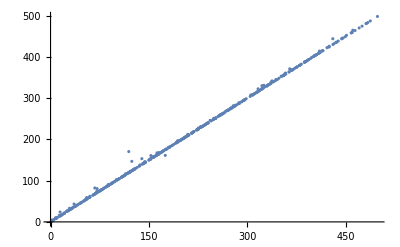

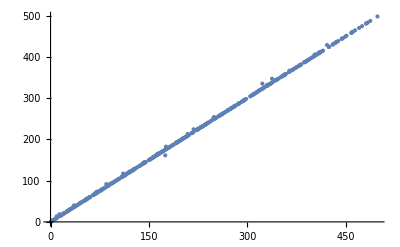

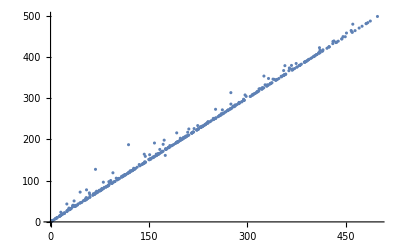

```mathematica
ListPlot[Partition[Riffle[ariamt2[[1;;500]],tstMT2],2],PlotRange->All]
```

## List of names, labels, final indices, and xsections

### Input LHEs bkgs

```mathematica
listinputs[[100]]
```

Part::partw: Part 100 of {{../../../flavorDM2_lhe/Events/run_14/unweighted_events.lhe,L_mphi_500.0_switch_0_0,{1,2},5.49901×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events/run_59/unweighted_events.lhe,L_mphi_500.0_switch_0_1,{1,2},3.70851×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events/run_149/unweighted_events.lhe,L_mphi_500.0_switch_1_1,{1,2},5.9747×10^-6,{True,{1,2}},{True,{1,2}}}} does not exist.

{{../../../flavorDM2_lhe/Events/run_14/unweighted_events.lhe,L_mphi_500.0_switch_0_0,{1,2},5.49901×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events/run_59/unweighted_events.lhe,L_mphi_500.0_switch_0_1,{1,2},3.70851×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events/run_149/unweighted_events.lhe,L_mphi_500.0_switch_1_1,{1,2},5.9747×10^-6,{True,{1,2}},{True,{1,2}}}}⟦100⟧

```mathematica
listinputs=listinputs[[40;;42]];
```

```mathematica
(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
label=listinputs[[ii,2]];
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[[ii,1]];
{finindices[label],xsec[label],mjjdata[label],MT2data[label]}=listinputs[[ii,{3,4,5,6}]];

importmodule[filename[label],label,finindices[label]];

If[mjjdata[label][[1]],Print["Calculating mjj"];mjjlist[label]=mjjlistcalc[label,mjjdata[label][[2]]]];
If[MT2data[label][[1]],Print["Calculating MT2"];MT2list[label]=MT2listcalculator[label,MT2data[label][[2]]]];
Print["=============== Done with label: "<>label<>"==============="];

,{ii,1,Length[listinputs]}]
```

```mathematica
MT2list[label]
```

### L -Model data on the mass plane

```mathematica
SetDirectory[NotebookDirectory[]];
mphisvals=Import["../../LL_model/mphis_grid.csv","CSV"]//Flatten;
mchisvals=Import["../../LL_model/mchis_grid.csv","CSV"]//Flatten;
deltamvals=Import["../../LL_model/LL_deltaM_GeV.csv","CSV"]//Flatten;

lambdavals=Import["../../LL_model/LL_lambdas_grid.csv","Table"];
widthvals=Import["../../LL_model/LL_phim_totwidth_GeV.csv","Table"];
BRlchivals=Import["../../LL_model/LL_phim_BR_lchi.csv","Table"];
BRphievvals=Import["../../LL_model/LL_phim_BR_phi0ev.csv","Table"];
BRphimuvvals=Import["../../LL_model/LL_phim_BR_phi0muv.csv","Table"];
```

```mathematica
alldataLLplane=Flatten[Table[{mchisvals[[χindx]],mphisvals[[ϕindx]],{"δmϕ",deltamvals[[ϕindx]]},{"λ",lambdavals[[ϕindx,χindx]]},{"τ_(ϕ+)",widthvals[[ϕindx,χindx]]^-1 hbar},{"BR_lχ",BRlchivals[[ϕindx,χindx]]},{"BR_ϕeν",BRphievvals[[ϕindx,χindx]]},{"BR_ϕμν",BRphimuvvals[[ϕindx,χindx]]}},{ϕindx,1,Length[mphisvals]},{χindx,1,Length[mchisvals]}],1];
```

```mathematica
alldataLLplane[[1]]
```

{0.00001,100.,{δmϕ,0.165719},{λ,5.98932×10^-9},{τ_(ϕ+),2.63837×10^-9},{BR_lχ,0.286059},{BR_ϕeν,0.126912},{BR_ϕμν,0.0149125}}

λ plot

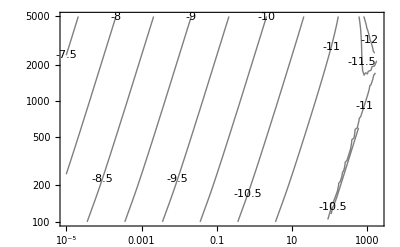

```mathematica
ListContourPlot[{#[[1]],#[[2]],Log10[#[[4,2]]]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,ContourLabels->All]
```

lifetimes ϕ+ plot in ns

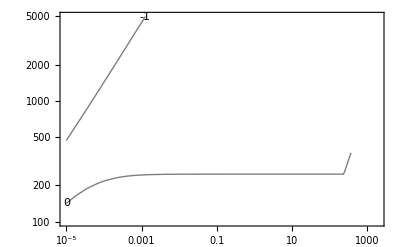

```mathematica
ListContourPlot[{#[[1]],#[[2]],Log10[#[[5,2]] 10^9 ]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,Contours->{-3,-2,-1,0,1},ContourLabels->All]
```

δm

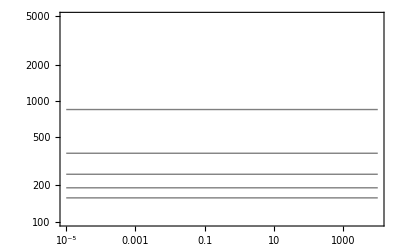

```mathematica
ListContourPlot[{#[[1]],#[[2]],#[[3,2]]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio]
```

BRs

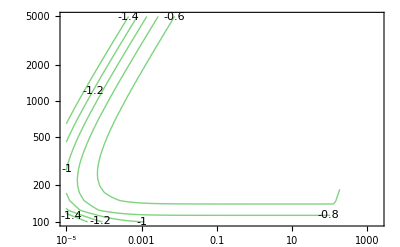

```mathematica
ListContourPlot[{#[[1]],#[[2]],Log10[#[[8,2]] ]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,ContourLabels->All,ContourStyle->Darker[Green]]
```

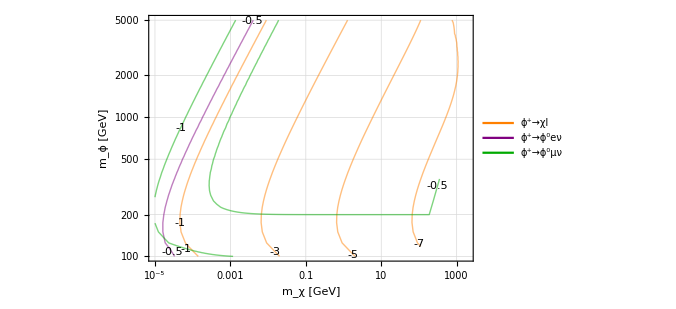

```mathematica
tst=Legended[Show[
ListContourPlot[{#[[1]],#[[2]],Log10[#[[6,2]] ]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,ContourLabels->All,ContourStyle->Orange,Contours->Range[-9,0,2],FrameLabel->{"m_χ [GeV]","m_ϕ [GeV]"}],

ListContourPlot[{#[[1]],#[[2]],Log10[#[[7,2]] ]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,ContourLabels->All,ContourStyle->Purple,Contours->Range[-10,0,0.5]],

ListContourPlot[{#[[1]],#[[2]],Log10[#[[8,2]] ]}&/@alldataLLplane,ContourShading->None,ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio,ContourLabels->All,ContourStyle->Darker[Green],Contours->Range[-10,0,0.5]],

ImageSize->500

]//frametrick
,Placed[LineLegend[{Orange,Purple,Darker[Green]},{"ϕ^+→χl","ϕ^+→ϕ^0eν","ϕ^+→ϕ^0μν"}],{0.1,0.8}]]
```

```mathematica
Export["BR_L.pdf",tst]
```

BR_L.pdf

```mathematica
lambdavals//Length
mphisvals//Length
lambdavals[[1]]//Length
mchisvals//Length
```

45

45

100

100

## Making Weighted Histograms

```mathematica
weightedmixmaker[listdata_,listxsec_]:=Module[{},
If[Length[listdata]!=Length[listxsec],Print["WRONG DATA AND WEIGHT COMBO"];Return[0]];
totx=Tr[listxsec];
weightssingle=#/totx&/@listxsec;
weights=Table[Table[weightssingle[[ch]],{i,1,Length[listdata[[ch]]]}],{ch,1,Length[listdata]}];
Table[WeightedData[listdata[[i]],weights[[i]] 10^4/Length[listdata[[i]]] ],{i,1,Length[listdata]}]
(*Ratio 10^4/Length[listdata[[i]]] : so that all individual histograms would be with 10^4 events before reweighting.*)
]
```

```mathematica
data1=RandomReal[{250,2500},10^4];
data2=RandomVariate[NormalDistribution[1000,150],10^4];
```

```mathematica
xsec1=3;
xsec2=1.5;
tst=weightedmixmaker[{data1,data2,data1,data2},{3/4 xsec2,1/3 xsec1,2/3 xsec1, 1/4xsec2}(*{1/2w1,1/3w2,2/3w2,1/2 w1}*)]
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

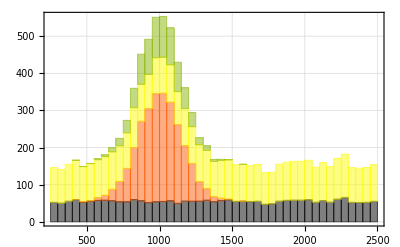

```mathematica
Histogram[tst,{50},ChartLayout->"Stacked",ChartStyle->3]//frametrick
```

## Merging Lists of Observables: To Select from After Cuts: OBSOLETE

Something that takes the lhefile labels and their cross sections (for both signal and bkg), the cuts of some observables, and the luminosity, and then gives us the event count for the signal and the bkg.
Xsec in pb.

Repeat the module below for any other set of observables

```mathematica
eventselectorMT2mjj[siglistlabels_,sigxseclist_,bkglistlabels_,bkgxseclist_,cutMT2_,cutmjj_,cutpT_,pTparticleindex_]:=Module[{},


Do[
(*putting the MT2 and mjj of each event together.*)
mergeddata[siglistlabels[[channindx]]]=Flatten[#]&/@Partition[Riffle[Partition[Riffle[MT2list[siglistlabels[[channindx]]],mjjlist[siglistlabels[[channindx]]]],2],pTlist[siglistlabels[[channindx]]][[pTparticleindex]]],2];
aftercutweight[siglistlabels[[channindx]]]=Length[Select[mergeddata[siglistlabels[[channindx]]],cutMT2[[1]]<=#[[1]]<=cutMT2[[2]]&&#[[2]]>=cutmjj&&#[[3]]>=cutpT&]]/Length[mergeddata[siglistlabels[[channindx]]]];

(*Print[ToString[aftercutweight[siglistlabels[[channindx]]]//N]];
Print[ToString[sigxseclist[[channindx]]]];*)

aftercutxsec[siglistlabels[[channindx]]]=aftercutweight[siglistlabels[[channindx]]] sigxseclist[[channindx]];

evencount[siglistlabels[[channindx]]]=aftercutxsec[siglistlabels[[channindx]]] 10^7(*Luminosity at a 10 TeV MuC in pb^-1*);

,{channindx,Range[1,Length[siglistlabels]]}];

Do[
(*putting the MT2 and mjj of each event together.*)
mergeddata[bkglistlabels[[channindx]]]=Flatten[#]&/@Partition[Riffle[Partition[Riffle[MT2list[bkglistlabels[[channindx]]],mjjlist[bkglistlabels[[channindx]]]],2],(#[[pTparticleindex]]&/@pTlist[bkglistlabels[[channindx]]])],2];
aftercutweight[bkglistlabels[[channindx]]]=Length[Select[mergeddata[bkglistlabels[[channindx]]],cutMT2[[1]]<=#[[1]]<=cutMT2[[2]]&&#[[2]]>=cutmjj&&#[[3]]>=cutpT&]]/Length[mergeddata[bkglistlabels[[channindx]]]];
aftercutxsec[bkglistlabels[[channindx]]]=aftercutweight[bkglistlabels[[channindx]]] bkgxseclist[[channindx]];

evencount[bkglistlabels[[channindx]]]=aftercutxsec[bkglistlabels[[channindx]]] 10^7(*Luminosity at a 10 TeV MuC*);

,{channindx,Range[1,Length[bkglistlabels]]}];

{{"Signal Count",Sum[evencount[siglistlabels[[channindx]]],{channindx,Range[1,Length[siglistlabels]]}]},{"Bkg Count",Sum[evencount[bkglistlabels[[channindx]]],{channindx,Range[1,Length[bkglistlabels]]}]}}

]
```

```mathematica
eventselectorMT2mjj[{"S"},{0.1},{"bkg_L"},{xsec[label]},4000,2000,0,1]
```

{{Signal Count,evencount[S]},{Bkg Count,10.1078}}

```mathematica
Riffle[Partition[Riffle[{1,2,3},{a,b,c}],2],{P,PP,PPP}]
```

{{1,a},P,{2,b},PP,{3,c},PPP}

```mathematica
Flatten[#]&/@Partition[Riffle[Partition[Riffle[{1,2,3},{a,b,c}],2],{P,PP,PPP}],2]
```

{{1,a,P},{2,b,PP},{3,c,PPP}}

# PROMPT L Model

## Generating all lhe file names and reading xsections

```mathematica
(*allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union*)
allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union
masslist=allmasses;
```

{100,150,200,250,300,350,400,450,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[cLfunc,cRfunc]
cstable=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em4.csv","CSV"]];
cfunc["L"]=Interpolation[#[[{1,2}]]&/@cstable]
cfunc["R"]=Interpolation[#[[{1,3}]]&/@cstable]
(*cstable8=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em8.csv","CSV"]];
cLfunc8=Interpolation[#[[{1,2}]]&/@cstable8]
cRfunc8=Interpolation[#[[{1,3}]]&/@cstable8]*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

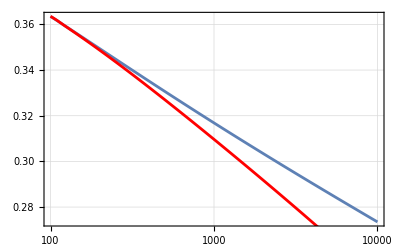

```mathematica
Show[
LogLinearPlot[cfunc["L"][m],{m,100,10000}],
LogLinearPlot[cfunc["R"][m],{m,100,10000},PlotStyle->Red]
]//frametrick
(*Show[
LogLinearPlot[cLfunc8[m],{m,100,10000}],
LogLinearPlot[cRfunc8[m],{m,100,10000},PlotStyle->Red]
]//frametrick*)
```

μμ initial preparing for lhe imports:

```mathematica
Clear[guide]
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["L"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4_fact_dyn.txt","Table"];
guide["R"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muRmuL_to_phipphim_chichimumu_resc1e-4_fact_dyn.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
noPDFxsec["L"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["L"][[2;;46]]
noPDFxsec["R"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["R"][[2;;46]]
```

{{100.,0.0000231043},{125.,0.0000230358},{150.,0.0000229984},{175.,0.0000229396},{200.,0.0000229216},{225.,0.0000228708},{250.,0.0000228751},{275.,0.0000228404},{300.,0.0000228262},{325.,0.0000228049},{350.,0.0000227964},{400.,0.0000227543},{450.,0.0000227271},{500.,0.0000226857},{550.,0.0000226408},{600.,0.0000225171},{650.,0.0000224672},{700.,0.0000223839},{750.,0.0000222528},{800.,0.0000221707},{900.,0.0000219083},{1000.,0.0000216563},{1100.,0.0000213596},{1200.,0.0000210502},{1300.,0.0000207143},{1400.,0.0000203392},{1500.,0.0000199494},{1600.,0.0000195243},{1800.,0.0000186081},{2000.,0.0000176247},{2200.,0.0000165313},{2400.,0.0000153968},{2600.,0.0000141629},{2800.,0.0000129184},{3000.,0.0000116017},{3200.,0.0000102441},{3400.,8.89269×10^-6},{3600.,7.51735×10^-6},{3800.,6.16923×10^-6},{4000.,4.82328×10^-6},{4200.,3.56254×10^-6},{4400.,2.38412×10^-6},{4600.,1.33587×10^-6},{4800.,4.84642×10^-7},{5000.,1.74146×10^-14}}

{{100.,0.000105436},{125.,0.000105086},{150.,0.000104913},{175.,0.000104686},{200.,0.000104575},{225.,0.000104397},{250.,0.000104345},{275.,0.000104215},{300.,0.000104186},{325.,0.00010406},{350.,0.000103955},{400.,0.000103841},{450.,0.000103692},{500.,0.000103518},{550.,0.00010326},{600.,0.00010272},{650.,0.000102456},{700.,0.000102071},{750.,0.000101527},{800.,0.000101149},{900.,0.000099973},{1000.,0.000098825},{1100.,0.000097478},{1200.,0.000096034},{1300.,0.000094467},{1400.,0.000092765},{1500.,0.000091027},{1600.,0.000089087},{1800.,0.000084915},{2000.,0.0000803843},{2200.,0.0000754251},{2400.,0.0000701874},{2600.,0.000064595},{2800.,0.0000589605},{3000.,0.0000529317},{3200.,0.0000467617},{3400.,0.0000405713},{3600.,0.0000342848},{3800.,0.000028146},{4000.,0.0000220089},{4200.,0.0000162582},{4400.,0.0000108773},{4600.,6.09483×10^-6},{4800.,2.2107×10^-6},{5000.,7.9592×10^-14}}

```mathematica
Clear[coeff]
coeff["_switch_0_0"]["L"][m_]:=  cfunc["L"][m] cfunc["R"][m];
coeff["_switch_0_0"]["R"][m_]:=  cfunc["L"][m] cfunc["R"][m];
(*coeff["_switch_0_1"]["L"][m_]:=  cfunc["L"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];*)
coeff["_switch_0_1"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_1"]["L"][m_]:=1;
coeff["_switch_1_1"]["R"][m_]:=1;
(*coeff["_VBF"]=1;*)
```

```mathematica
guide["R"][[{26,71,116,161}]]
```

{{run_25,mphi_1300.0_switch_0_0,0.000094467,6.90026×10^-8,10000},{run_70,mphi_1300.0_switch_0_1,0.0000208154,3.7341×10^-8,10000},{run_115,mphi_1300.0_switch_1_0,0.0000207886,3.45012×10^-8,10000},{run_160,mphi_1300.0_switch_1_1,4.50378×10^-6,1.1592×10^-8,10000}}

```mathematica
Clear[listinputs]
listinputs["L"]={};
listinputs["R"]={};
Do[
Do[
Do[
tst=Select[guide[LRRL],#[[2]]=="mphi_"<>ToString[masses]<>".0"<>labelappend&];
tstdirectory=tst[[1,1]];
tstlabel="L_"<>tst[[1,2]];
(*xsec[tstlabel]=coeff[labelappend]tst[[1,3]];*)
xsec[tstlabel]=coeff[labelappend][LRRL][masses]tst[[1,3]];
AppendTo[listinputs[LRRL],{"../../../flavorDM2_lhe/Events_L_"<>LRRL<>"/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"}}]

,{masses,allmasses}]

,{LRRL,{"L","R"}}]
listinputs["L"];
listinputs["R"];
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

```mathematica
iii=0;
listinputs["R"][[57+iii]]
listinputs["R"][[61+iii]]

coeff["_switch_0_0"]["L"][1300]
coeff["_switch_0_1"]["L"][1300]
coeff["_switch_1_0"]["L"][1300]

listinputs["L"][[57+iii]]
listinputs["L"][[61+iii]]
```

{../../../flavorDM2_lhe/Events_L_R/run_24/unweighted_events.lhe,L_mphi_1200.0_switch_0_0,{1,2},9.17614×10^-6,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/Events_L_R/run_26/unweighted_events.lhe,L_mphi_1400.0_switch_0_0,{1,2},8.66499×10^-6,{True,{1,2}},{True,{1,2}}}

0.0944381

0.302948

0.302948

{../../../flavorDM2_lhe/Events_L_L/run_24/unweighted_events.lhe,L_mphi_1200.0_switch_0_0,{1,2},2.01137×10^-6,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/Events_L_L/run_26/unweighted_events.lhe,L_mphi_1400.0_switch_0_0,{1,2},1.89984×10^-6,{True,{1,2}},{True,{1,2}}}

```mathematica
(*dynamic 10^-4*)
Clear[xsecall4dyn,massxsecall4dyn]
Do[
xsecall4dyn[LRRL]=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs[LRRL],4];
massxsecall4dyn[LRRL]=Partition[Riffle[allmasses,xsecall4dyn[LRRL]],2]
,{LRRL,{"L","R"}}]
(*10^-4*)
(*xsecall4=#[[1]]+#[[2]]+#[[3]]&/@Partition[#[[4]]&/@listinputs,3]
massxsecall4=Partition[Riffle[allmasses,xsecall4],2]*)
(*10^-8*)
(*xsecall8=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs,4]
massxsecall8=Partition[Riffle[allmasses,xsecall8],2]*)
```

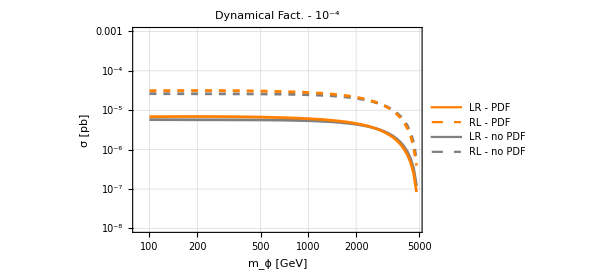

```mathematica
Legended[Show[
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["L"][[1;;-2]],Joined->True,PlotStyle->Gray,PlotRange->{10^-3,10^-8},FrameLabel->{"m_ϕ [GeV]","σ [pb]"},PlotLabel->"Dynamical Fact. - 10^-4"],
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["R"][[1;;-2]],Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[massxsecall4dyn["L"],Joined->True,PlotStyle->Orange],
ListLogLogPlot[massxsecall4dyn["R"],Joined->True,PlotStyle->{Orange,Dashed}]

],Placed[LineLegend[{Orange,{Dashed,Orange},Gray,{Dashed,Gray}},{"LR - PDF","RL - PDF","LR - no PDF","RL - no PDF"}],{0.2,0.25}]]//frametrick
```

VBF initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
guide["VBF"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_vv_to_phipphim_chichimumu.txt","Table"][[2;;-1]]
```

{{run_01,mphi_100.0,0.000831282,2.75697×10^-6,10000},{run_02,mphi_125.0,0.000553254,1.75824×10^-6,10000},{run_03,mphi_150.0,0.000390265,1.46122×10^-6,10000},{run_04,mphi_175.0,0.000289206,9.50791×10^-7,10000},{run_05,mphi_200.0,0.000220649,7.5856×10^-7,10000},{run_06,mphi_225.0,0.000173323,4.82447×10^-7,10000},{run_07,mphi_250.0,0.000140001,4.28887×10^-7,10000},{run_08,mphi_275.0,0.000114893,3.90826×10^-7,10000},{run_09,mphi_300.0,0.000095026,2.60928×10^-7,10000},{run_10,mphi_325.0,0.000080091,2.22739×10^-7,10000},{run_11,mphi_350.0,0.0000675913,1.79633×10^-7,10000},{run_12,mphi_400.0,0.0000499285,1.40702×10^-7,10000},{run_13,mphi_450.0,0.0000379843,1.06941×10^-7,10000},{run_14,mphi_500.0,0.0000293802,8.68805×10^-8,10000},{run_15,mphi_550.0,0.0000234468,6.9419×10^-8,10000},{run_16,mphi_600.0,0.0000187797,4.53134×10^-8,10000},{run_17,mphi_650.0,0.0000153013,3.40029×10^-8,10000},{run_18,mphi_700.0,0.0000125182,3.81228×10^-8,10000},{run_19,mphi_750.0,0.0000104477,2.62153×10^-8,10000},{run_20,mphi_800.0,8.74773×10^-6,1.99999×10^-8,10000},{run_21,mphi_900.0,6.27027×10^-6,1.5535×10^-8,10000},{run_22,mphi_1000.0,4.59914×10^-6,1.07876×10^-8,10000},{run_23,mphi_1100.0,3.4241×10^-6,7.96577×10^-9,10000},{run_24,mphi_1200.0,2.59275×10^-6,5.76445×10^-9,10000},{run_25,mphi_1300.0,1.99811×10^-6,4.34143×10^-9,10000},{run_26,mphi_1400.0,1.55432×10^-6,3.25104×10^-9,10000},{run_27,mphi_1500.0,1.22045×10^-6,3.58769×10^-9,10000},{run_28,mphi_1600.0,9.66741×10^-7,1.90395×10^-9,10000},{run_29,mphi_1800.0,6.16319×10^-7,1.41283×10^-9,10000},{run_30,mphi_2000.0,3.99816×10^-7,8.56997×10^-10,10000},{run_31,mphi_2200.0,2.62218×10^-7,4.89051×10^-10,10000},{run_32,mphi_2400.0,1.73453×10^-7,2.65615×10^-10,10000},{run_33,mphi_2600.0,1.15681×10^-7,1.85047×10^-10,10000},{run_34,mphi_2800.0,7.70712×10^-8,1.40462×10^-10,10000},{run_35,mphi_3000.0,5.08373×10^-8,7.6312×10^-11,10000},{run_36,mphi_3200.0,3.33894×10^-8,5.15192×10^-11,10000},{run_37,mphi_3400.0,2.15501×10^-8,2.56002×10^-11,10000},{run_38,mphi_3600.0,1.3539×10^-8,1.20929×10^-11,10000},{run_39,mphi_3800.0,8.19234×10^-9,7.83862×10^-12,10000},{run_40,mphi_4000.0,4.69272×10^-9,5.02477×10^-12,10000},{run_41,mphi_4200.0,2.45334×10^-9,1.98294×10^-12,10000},{run_42,mphi_4400.0,1.10739×10^-9,1.26594×10^-12,10000},{run_43,mphi_4600.0,3.76873×10^-10,3.29619×10^-13,10000},{run_44,mphi_4800.0,6.38946×10^-11,6.07665×10^-14,10000},{run_45,mphi_5000.0,8.54657×10^-22,2.8245×10^-24,10000}}

```mathematica
listinputs["VBF"]={};
Do[
tst=Select[guide["VBF"],#[[2]]=="mphi_"<>ToString[masses]<>".0"&];
tstdirectory=tst[[1,1]];
tstlabel="L_"<>tst[[1,2]]<>"_VBF";
xsec[tstlabel]=tst[[1,3]];
AppendTo[listinputs["VBF"],{"../../../flavorDM2_lhe/Events_L_VBF/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs["VBF"]
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

{{../../../flavorDM2_lhe/Events_L_VBF/run_01/unweighted_events.lhe,L_mphi_100.0_VBF,{1,2},0.000831282,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_03/unweighted_events.lhe,L_mphi_150.0_VBF,{1,2},0.000390265,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_05/unweighted_events.lhe,L_mphi_200.0_VBF,{1,2},0.000220649,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_07/unweighted_events.lhe,L_mphi_250.0_VBF,{1,2},0.000140001,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_09/unweighted_events.lhe,L_mphi_300.0_VBF,{1,2},0.000095026,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_11/unweighted_events.lhe,L_mphi_350.0_VBF,{1,2},0.0000675913,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_12/unweighted_events.lhe,L_mphi_400.0_VBF,{1,2},0.0000499285,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_13/unweighted_events.lhe,L_mphi_450.0_VBF,{1,2},0.0000379843,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_14/unweighted_events.lhe,L_mphi_500.0_VBF,{1,2},0.0000293802,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_16/unweighted_events.lhe,L_mphi_600.0_VBF,{1,2},0.0000187797,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_18/unweighted_events.lhe,L_mphi_700.0_VBF,{1,2},0.0000125182,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_20/unweighted_events.lhe,L_mphi_800.0_VBF,{1,2},8.74773×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_21/unweighted_events.lhe,L_mphi_900.0_VBF,{1,2},6.27027×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_22/unweighted_events.lhe,L_mphi_1000.0_VBF,{1,2},4.59914×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_24/unweighted_events.lhe,L_mphi_1200.0_VBF,{1,2},2.59275×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_26/unweighted_events.lhe,L_mphi_1400.0_VBF,{1,2},1.55432×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_28/unweighted_events.lhe,L_mphi_1600.0_VBF,{1,2},9.66741×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_29/unweighted_events.lhe,L_mphi_1800.0_VBF,{1,2},6.16319×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_30/unweighted_events.lhe,L_mphi_2000.0_VBF,{1,2},3.99816×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_31/unweighted_events.lhe,L_mphi_2200.0_VBF,{1,2},2.62218×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_32/unweighted_events.lhe,L_mphi_2400.0_VBF,{1,2},1.73453×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_33/unweighted_events.lhe,L_mphi_2600.0_VBF,{1,2},1.15681×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_34/unweighted_events.lhe,L_mphi_2800.0_VBF,{1,2},7.70712×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_35/unweighted_events.lhe,L_mphi_3000.0_VBF,{1,2},5.08373×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_36/unweighted_events.lhe,L_mphi_3200.0_VBF,{1,2},3.33894×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_37/unweighted_events.lhe,L_mphi_3400.0_VBF,{1,2},2.15501×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_38/unweighted_events.lhe,L_mphi_3600.0_VBF,{1,2},1.3539×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_39/unweighted_events.lhe,L_mphi_3800.0_VBF,{1,2},8.19234×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_40/unweighted_events.lhe,L_mphi_4000.0_VBF,{1,2},4.69272×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_41/unweighted_events.lhe,L_mphi_4200.0_VBF,{1,2},2.45334×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_42/unweighted_events.lhe,L_mphi_4400.0_VBF,{1,2},1.10739×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_43/unweighted_events.lhe,L_mphi_4600.0_VBF,{1,2},3.76873×10^-10,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/Events_L_VBF/run_44/unweighted_events.lhe,L_mphi_4800.0_VBF,{1,2},6.38946×10^-11,{True,{1,2}},{True,{1,2}}}}

## Reading lhe files from the names defined above - and calculating all observables. Takes a while. SKIP NOW: already saved data

```mathematica
listinputs["R"][[1;;1]]
```

{{../../../flavorDM2_lhe/Events_L_R/run_01/unweighted_events.lhe,L_mphi_100.0_switch_0_0,{1,2},6.96603×10^-6,{True,{1,2}},{True,{1,2}}}}

Reading LHE files and calculating everything - MT2 included. 
Works for both VBF or μμ: just run different blocks in the section above.
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
(*(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[LRRL][[ii,1]];
{finindices[label],xsec[label],mjjdata[label],MT2data[label]}=listinputs[LRRL][[ii,{3,4,5,6}]];

importmodule[filename[label],label,finindices[label]];

If[mjjdata[label][[1]],Print["Calculating mjj"];mjjlist[label]=mjjlistcalc[label,mjjdata[label][[2]]]];
If[MT2data[label][[1]],Print["Calculating MT2"];MT2list[label]=MT2listcalculator[label,MT2data[label][[2]]]];
Print["=============== Done with label: "<>label<>"==============="];


evententry[label]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

Export["../../../flavorDM2_lhe/saved_data_L/"<>label<>".dat",evententry[label]];

Print["=============== Event Entry Exported: "<>label<>"==============="];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{(*"L","R",*)"VBF"}}]*)
```

Bkg lhe import:
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
(*bkg_L: DONE WITH MT2 IMPROVED*)
(*importmodule["../../lhe_files/eL_model_bkg/ellR_bkg_mumuvv.lhe","bkg_L",{1,2}]
mjjlist["bkg_L"]=mjjlistcalc["bkg_L",{1,2}];
MT2list["bkg_L"]=MT2listcalculator["bkg_L",{1,2}];*)

(*bkg_L_old*)
(*importmodule["../../../flavorDM2_lhe/mumu_to_llvv/Events/run_02/unweighted_events.lhe","bkg_L_old",{1,2}];
mjjlist["bkg_L_old"]=mjjlistcalc["bkg_L_old",{1,2}];
MT2list["bkg_L_old"]=MT2listcalculator["bkg_L_old",{1,2}];*)

(*bkg_L_cut200*)
(*importmodule["../../../flavorDM2_lhe/mumu_to_mumuvv_cuts/Events/run_01/unweighted_events.lhe","bkg_L_cut200",{1,2}];
mjjlist["bkg_L_cut200"]=mjjlistcalc["bkg_L_cut200",{1,2}];
MT2list["bkg_L_cut200"]=MT2listcalculator["bkg_L_cut200",{1,2}];*)

(**)
(*SetDirectory[NotebookDirectory[]];
(*importmodule["../../../flavorDM2_lhe/mumu_to_llvv/Events/run_02/unweighted_events.lhe","bkg_L_ll",{1,2}];*)
importmodule["../../../flavorDM2_lhe/mumu_to_llvv/Events/Events/run_01/unweighted_events.lhe","bkg_L_ll",{1,2}];
mjjlist["bkg_L_ll"]=mjjlistcalc["bkg_L_ll",{1,2}];
MT2list["bkg_L_ll"]=MT2listcalculator["bkg_L_ll",{1,2}];*)
```

```mathematica
(*evententry["L","bkg_L_ll"]=Table[{{"η",etalist["bkg_L_ll"][[ii]]},{"pT",pTlist["bkg_L_ll"][[ii]]},{"pTvec",pTveclist["bkg_L_ll"][[ii]]},{"fourvec",fourvecslist["bkg_L_ll"][[ii]]},{"ET",ETlist["bkg_L_ll"][[ii]]},{"beta",betalist["bkg_L_ll"][[ii]]},{"gamma",gammalist["bkg_L_ll"][[ii]]},{"MT2",MT2list["bkg_L_ll"][[ii]]},{"mjj",mjjlist["bkg_L_ll"][[ii]]}},{ii,1,Length[etalist["bkg_L_ll"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_ll"<>".dat",evententry["L","bkg_L_ll"]];*)
```

### MT2 comparison to aria

```mathematica
pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;
```

```mathematica
(*pouyamt2=MT2list[label];*)
pouyamt2new=MT2list[label];
```

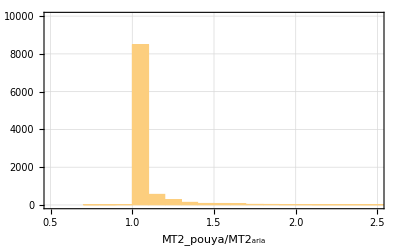

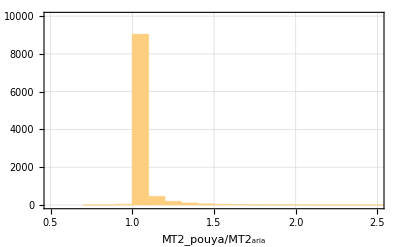

```mathematica
Histogram[pouyamt2new/ariamt2,{0.1},PlotRange->{{0.5,2.5},{1,10^4}},FrameLabel->{"MT2_pouya/MT2_aria"}]//frametrick
```

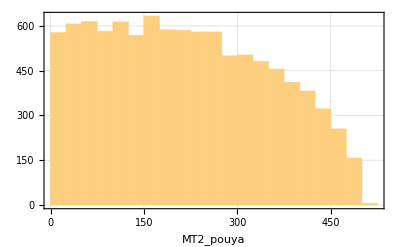

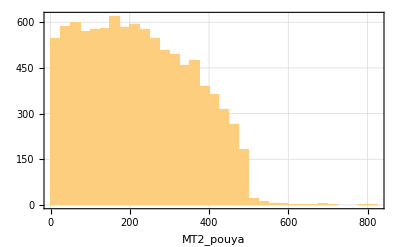

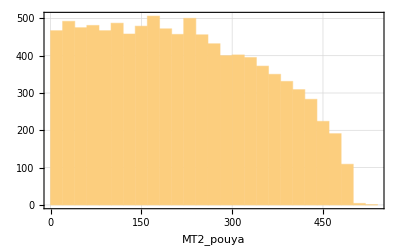

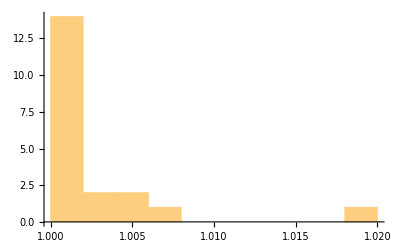

```mathematica
Histogram[pouyamt2,{25},FrameLabel->{"MT2_pouya"}]//frametrick
Histogram[pouyamt2new,{25},FrameLabel->{"MT2_pouya"}]//frametrick
```

```mathematica
Select[evententry["L",500,"_switch_0_0"],#[[-2,2]]>=500&]//Length
```

398

```mathematica
(*pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;*)
```

```mathematica
pouyamt2[[1;;22]]
ariamt2[[1;;22]]
```

{232.011,207.216,167.936,96.7128,201.31,163.765,444.962,128.659,87.4183,489.129,4.51487,143.431,97.9494,393.805,83.9932,136.572,21.8336,368.398,95.4135,121.853,53.2748,112.125}

{231.972,201.592,101.669,96.334,196.927,155.84,430.136,93.5088,87.328,286.936,2.98635,143.431,97.919,393.804,78.2696,136.435,20.8355,367.193,93.4874,94.2818,45.1187,88.7516}

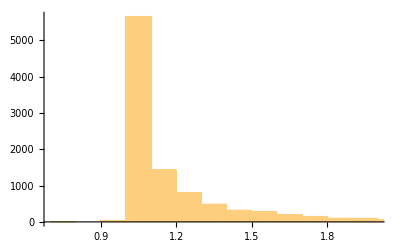

```mathematica
Histogram[pouyamt2/ariamt2]
```

## ***Now it’s done above with the importmodule code. SKIP*** Unifying all the data for an event in the “evententry” variable - Exports data to the saved_data folder The xsection is not saved and will be read from above

```mathematica
(*(*Clear[evententry]*)
SetDirectory[NotebookDirectory[]];
Do[
Print["============= m_ϕ = "<>ToString[mphi]<>"============"];
Do[
label="L_mphi_"<>ToString[mphi]<>".0"<>labelappend;
(*Print[label];*)
evententry["L",mphi,labelappend]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

(*Print[ToString[evententry["L",mphi,labelappend][[1,-1]]]];*)

Export["../../../flavorDM2_lhe/saved_data/"<>label<>".dat",evententry["L",mphi,labelappend]];

,{labelappend,{(*"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1",*)"_VBF"}}]
,{mphi,masslist}]*)
```

```mathematica
(*
evententry["L","bkg_L"]=Table[{{"η",etalist["bkg_L"][[ii]]},{"pT",pTlist["bkg_L"][[ii]]},{"pTvec",pTveclist["bkg_L"][[ii]]},{"fourvec",fourvecslist["bkg_L"][[ii]]},{"ET",ETlist["bkg_L"][[ii]]},{"beta",betalist["bkg_L"][[ii]]},{"gamma",gammalist["bkg_L"][[ii]]},{"MT2",MT2list["bkg_L"][[ii]]},{"mjj",mjjlist["bkg_L"][[ii]]}},{ii,1,Length[etalist["bkg_L"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L"<>".dat",evententry["L","bkg_L"]];*)
```

```mathematica
(*
evententry["L","bkg_L_old"]=Table[{{"η",etalist["bkg_L_old"][[ii]]},{"pT",pTlist["bkg_L_old"][[ii]]},{"pTvec",pTveclist["bkg_L_old"][[ii]]},{"fourvec",fourvecslist["bkg_L_old"][[ii]]},{"ET",ETlist["bkg_L_old"][[ii]]},{"beta",betalist["bkg_L_old"][[ii]]},{"gamma",gammalist["bkg_L_old"][[ii]]},{"MT2",MT2list["bkg_L_old"][[ii]]},{"mjj",mjjlist["bkg_L_old"][[ii]]}},{ii,1,Length[etalist["bkg_L_old"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_old"<>".dat",evententry["L","bkg_L_old"]];*)
```

```mathematica
(*
evententry["L","bkg_L_cut200"]=Table[{{"η",etalist["bkg_L_cut200"][[ii]]},{"pT",pTlist["bkg_L_cut200"][[ii]]},{"pTvec",pTveclist["bkg_L_cut200"][[ii]]},{"fourvec",fourvecslist["bkg_L_cut200"][[ii]]},{"ET",ETlist["bkg_L_cut200"][[ii]]},{"beta",betalist["bkg_L_cut200"][[ii]]},{"gamma",gammalist["bkg_L_cut200"][[ii]]},{"MT2",MT2list["bkg_L_cut200"][[ii]]},{"mjj",mjjlist["bkg_L_cut200"][[ii]]}},{ii,1,Length[etalist["bkg_L_cut200"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_cut200"<>".dat",evententry["L","bkg_L_cut200"]];*)
```

```mathematica
(*Clear[evententry]*)
```

```mathematica
(*evententry["L","bkg_L_ll"]=Table[{{"η",etalist["bkg_L_ll"][[ii]]},{"pT",pTlist["bkg_L_ll"][[ii]]},{"pTvec",pTveclist["bkg_L_ll"][[ii]]},{"fourvec",fourvecslist["bkg_L_ll"][[ii]]},{"ET",ETlist["bkg_L_ll"][[ii]]},{"beta",betalist["bkg_L_ll"][[ii]]},{"gamma",gammalist["bkg_L_ll"][[ii]]},{"MT2",MT2list["bkg_L_ll"][[ii]]},{"mjj",mjjlist["bkg_L_ll"][[ii]]}},{ii,1,Length[etalist["bkg_L_ll"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_ll"<>".dat",evententry["L","bkg_L_ll"]];*)
```

## Importing the “evententry” data of each event XSECTIONS MULTIPLIED BY 4 FOR 4 LEPTON CHANNELS: ee,eμ,μe,μμ

```mathematica
SetDirectory[NotebookDirectory[]];
Do[
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
xsec[label]=4(*ll HS 4 FINAL STATE CHANNELS BUT XSECTIONS FROM LHE FILES HAS ONLY μμ*)listinputs[LRRL][[ii,4]];
,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]
```

```mathematica
Do[
Do[
(*label="L_mphi_"<>ToString[mphi]<>".0"<>labelappend<>"_"<>LRRL;*)
label=If[LRRL=="VBF",listinputs[LRRL][[ii,2]],listinputs[LRRL][[ii,2]]<>"_"<>LRRL];
evententry[label]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>label<>".dat","TSV"]];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}];
Print["Label Done: "<>label];
,{LRRL,{"L","R","VBF"}}]
```

Label Done: L_mphi_4800.0_switch_1_1_L

Label Done: L_mphi_4800.0_switch_1_1_R

Label Done: L_mphi_4800.0_VBF

```mathematica
evententry["L_mphi_100.0_switch_0_0_L"][[1]]
evententry["L_mphi_100.0_VBF"][[1]]
```

{{η,{0.0971648,-0.0835348}},{pT,{4381.73,3739.22}},{pTvec,{{0,4166.25,1357.17,0},{0,-3548.6,-1178.65,0}}},{fourvec,{{4402.43,4166.25,1357.17,426.421},{3752.27,-3548.6,-1178.65,-312.718}}},{ET,{4381.73,3739.22}},{beta,{1.,1.}},{gamma,{0.-206557. ⅈ,209865.}},{MT2,33.0897},{mjj,8128.53}}

{{η,{1.38898,-0.272493}},{pT,{186.319,317.552}},{pTvec,{{0,-98.1175,158.391,0},{0,117.398,-295.054,0}}},{fourvec,{{396.869,-98.1175,158.391,350.414},{329.414,117.398,-295.054,-87.6056}}},{ET,{186.319,317.552}},{beta,{1.,1.}},{gamma,{0.-313805. ⅈ,429649.}},{MT2,42.7393},{mjj,662.85}}

{{η,{0.0971648,-0.0835348}},{pT,{4381.73,3739.22}},{pTvec,{{0,4166.25,1357.17,0},{0,-3548.6,-1178.65,0}}},{fourvec,{{4402.43,4166.25,1357.17,426.421},{3752.27,-3548.6,-1178.65,-312.718}}},{ET,{4381.73,3739.22}},{beta,{1.,1.}},{gamma,{0.-206557. ⅈ,209865.}},{MT2,33.0897},{mjj,8128.53}}

{{η,{1.38898,-0.272493}},{pT,{186.319,317.552}},{pTvec,{{0,-98.1175,158.391,0},{0,117.398,-295.054,0}}},{fourvec,{{396.869,-98.1175,158.391,350.414},{329.414,117.398,-295.054,-87.6056}}},{ET,{186.319,317.552}},{beta,{1.,1.}},{gamma,{0.-313805. ⅈ,429649.}},{MT2,42.7393},{mjj,662.85}}

```mathematica
SetDirectory[NotebookDirectory[]];
(*evententry["L","bkg_L"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L"<>".dat","TSV"]];
evententry["L","bkg_L_old"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_old"<>".dat","TSV"]];*)
(*evententry["L","bkg_L_cut200"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_cut200"<>".dat","TSV"]];*)
evententry["L","bkg_L_ll"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_ll"<>".dat","TSV"]];
```

```mathematica
(*xsec["bkg_L_old"]=0.1;
xsec["bkg_L"]=0.1;*)
(*xsec["bkg_L_cut200"]=0.010886;*)
xsec["bkg_L_ll"]=0.0168;
```

## For a test mass, extracting an observables from all events to make hiastograms

{{η,{0.30146,-0.360538}},{pT,{3087.44,4322.67}},{pTvec,{{0,3083.94,146.887,0},{0,-4322.13,68.7921,0}}},{fourvec,{{3228.79,3083.94,146.887,944.899},{4606.68,-4322.13,68.7921,-1592.47}}},{ET,{3087.44,4322.67}},{beta,{1.,1.}},{gamma,{0.-356396. ⅈ,0.-1.28368×10^6 ⅈ}},{MT2,234.243},{mjj,7706.86}}

```mathematica
Clear[listlabels]
listlabels["L"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["R"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["VBF"]={"_VBF"};
```

```mathematica
(*Clear[dataxsecall]*)
Clear[histogramdata]
Do[

Do[
dataxsecall["L",mphi,LRRL]={};
allhistogramdata["MT2"]["L",mphi,LRRL]={};
allhistogramdata["mjj"]["L",mphi,LRRL]={};
allhistogramdata["pT"]["L",mphi,LRRL]={};
allhistogramdata["pTll"]["L",mphi,LRRL]={};
allhistogramdata["eta"]["L",mphi,LRRL]={};
allhistogramdata["cosθ"]["L",mphi,LRRL]={};

Do[
fulllabel=If[LRRL=="VBF","L_mphi_"<>ToString[mphi]<>".0"<>label,"L_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL];
AppendTo[dataxsecall["L",mphi,LRRL],xsec[fulllabel]];
histogramdata["MT2"]["L",mphi,label,LRRL]=#[[-2,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["MT2"]["L",mphi,LRRL],histogramdata["MT2"]["L",mphi,label,LRRL]];
histogramdata["mjj"]["L",mphi,label,LRRL]=#[[-1,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["mjj"]["L",mphi,LRRL],histogramdata["mjj"]["L",mphi,label,LRRL]];
histogramdata["pT"]["L",mphi,label,LRRL]=#[[2,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pT"]["L",mphi,LRRL],histogramdata["pT"]["L",mphi,label,LRRL]];
histogramdata["pTll"]["L",mphi,label,LRRL]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pTll"]["L",mphi,LRRL],histogramdata["pTll"]["L",mphi,label,LRRL]];
histogramdata["eta"]["L",mphi,label,LRRL]=#[[1,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["eta"]["L",mphi,LRRL],histogramdata["eta"]["L",mphi,label,LRRL]];
histogramdata["cosθ"]["L",mphi,label,LRRL]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[fulllabel];
AppendTo[allhistogramdata["cosθ"]["L",mphi,LRRL],histogramdata["cosθ"]["L",mphi,label,LRRL]];

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];

dataxsecall["L",mphi]={Riffle[dataxsecall["L",mphi,"L"],dataxsecall["L",mphi,"R"]]};
AppendTo[dataxsecall["L",mphi],dataxsecall["L",mphi,"VBF"]];



order={9,7,8,3,4,5,6,1,2}; (*ORDER FOR PRESENTATION IN THE HISTOGRAM*)

dataxsecall["L",mphi]=Flatten[dataxsecall["L",mphi],1][[order]];
Do[
allhistogramdata[obs]["L",mphi]={Riffle[allhistogramdata[obs]["L",mphi,"L"],allhistogramdata[obs]["L",mphi,"R"]]};
AppendTo[allhistogramdata[obs]["L",mphi],allhistogramdata[obs]["L",mphi,"VBF"]];
allhistogramdata[obs]["L",mphi]=Flatten[allhistogramdata[obs]["L",mphi],1][[order]];
,{obs,{"MT2","mjj","pT","pTll","eta","cosθ"}}]

,{mphi,masslist}]



(*BKG Data*)
Do[
histogramdata["MT2"]["L",bkglabel]=#[[-2,2]]&/@evententry["L",bkglabel];
histogramdata["mjj"]["L",bkglabel]=#[[-1,2]]&/@evententry["L",bkglabel];
histogramdata["pT"]["L",bkglabel]=#[[2,2,1]]&/@evententry["L",bkglabel];
histogramdata["pTll"]["L",bkglabel]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry["L",bkglabel];
histogramdata["eta"]["L",bkglabel]=#[[1,2,1]]&/@evententry["L",bkglabel];
histogramdata["cosθ"]["L",bkglabel]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry["L",bkglabel];


,{bkglabel,{"bkg_L_ll"(*"bkg_L","bkg_L_old","bkg_L_cut200"*)}}
]
```

```mathematica
histogramdata["MT2"]["L",1000,"_switch_1_0","L"][[1]]
histogramdata["MT2"]["L",1000,"_switch_1_0","R"][[1]]
histogramdata["MT2"]["L",1000,"_VBF","VBF"][[1]]
```

101.143

650.81

40.9056

101.143

650.81

40.9056

## Checking against Aria’s calculation: the signal file with 500 GeV mass mediator

```mathematica
ariattst=ToExpression[Import["../../../flavorDM2_lhe/dilepton_summary_test.csv","CSV"]]
mphitst=500;
label="_switch_0_0";
```

mll

```mathematica
label
```

histogramdatamjj[L,1000,L_mphi_4800.0_VBF]

```mathematica
ariadata=#[[1]]&/@ariattst[[2;;-1]];
Sort[(ariadata-histogramdatamjj["L",mphitst,label][[1;;-1]])/ariadata,#1>=#2&][[{1,2,3,-3,-2,-1}]]
```

{1.04692×10^-14,8.42513×10^-15,5.01799×10^-15,-6.55483×10^-15,-8.68075×10^-15,-5.42344×10^-14}

pTll

```mathematica
ariadata=#[[2]]&/@ariattst[[2;;-1]];
Sort[(ariadata-histogramdatapTll["L",mphitst,label][[1;;-1]])/ariadata,#1>=#2&][[{1,2,3,-3,-2,-1}]]
```

{3.4776×10^-16,3.30837×10^-16,2.99938×10^-16,-3.11621×10^-16,-3.12838×10^-16,-3.69596×10^-16}

MT2

```mathematica
ariadata=#[[-1]]&/@ariattst[[2;;-1]];
Sort[(ariadata-histogramdataMT2["L",mphitst,label][[1;;-1]])/ariadata,#1>=#2&][[{1,2,3,-3,-2,-1}]]
```

{0.243197,0.227538,0.190331,-0.709392,-0.932485,-0.95803}

```mathematica
tst=Partition[Riffle[ariadata,histogramdataMT2["L",mphitst,label]],2]
```

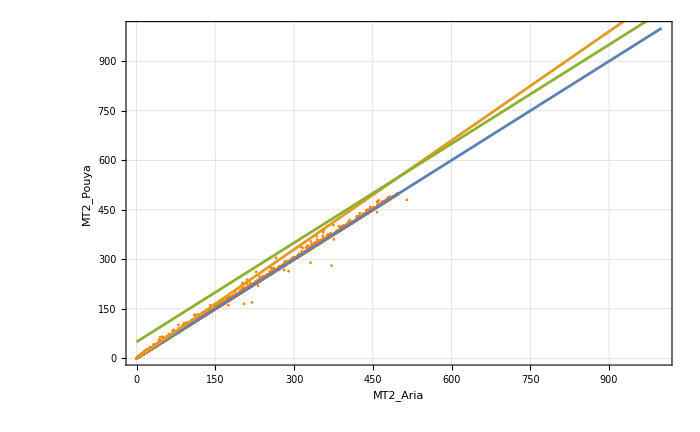

```mathematica
Show[
ListPlot[tst,FrameLabel->{"MT2_Aria","MT2_Pouya"},PlotRange->{{0,1000},{0,1000}},PlotStyle->Orange,ImageSize->700]//frametrick,
Plot[{x,1.1x,x+50},{x,0,1000}]
]
```

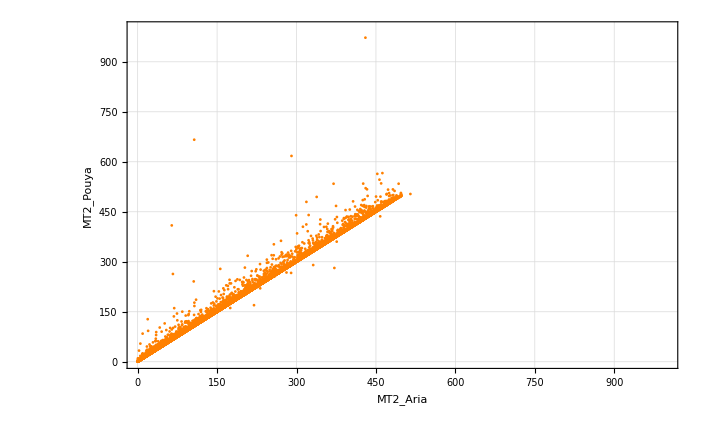

```mathematica
evententry
```

## Compare to older aria bkg file

```mathematica
ariaoldbkg=ToExpression[Import["../../../flavorDM2_lhe/mumu_to_llvv/Events/run_02/dilepton_summary.csv","CSV"]];
```

```mathematica
#[[-2,2]]&/@evententry["L","bkg_L_old"][[100;;110]]
ariaoldbkg[[1]]
#[[-1]]&/@ariaoldbkg[[101;;111]]
```

{29.3202,125.311,110.276,311.088,41.8636,211.278,73.703,7.70868,404.092,188.92,544.19}

{m_ll,pt_ll,_ll cos_theta,deltaR_ll,MT2}

{29.2588,125.258,110.239,310.937,41.8553,211.065,73.7028,7.70459,403.908,188.916,541.817}

## Histograms 1D: USE PDF FUNCTION BUT IT INTRODUCES SOME RANDOM NORMALIZATION THAT SHOULD BE FIXED BY HAND TO AGREE WITH THE PROPER DISCRETE CALC. I STILL KEPT IN THE PLOT PART.

```mathematica
mphitst=2800;
bkglabel="bkg_L_ll";
modellabel="L";
```

```mathematica
tst=weightedmixmaker[allhistogramdata["eta"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["eta"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=-2.4;maxx=2.4;stepx=0.2;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.2 10^4 PDF[helper,#]}&/@binsdata;
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

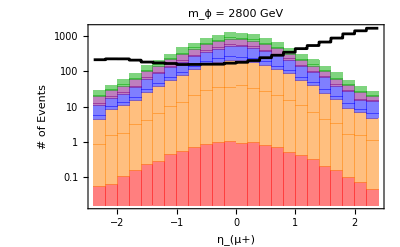

```mathematica
plt=Show[
Histogram[tst,{minx,maxx,0.2},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None]//frametricknogrid,


(*Histogram[bkgtst,{0.2},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

(*ListLinePlot[bkgtstss,InterpolationOrder->0,PlotStyle->Black,ScalingFunctions->"Log"],*)
Plot[2 10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

```mathematica
Export["L_histogrameta_"<>ToString[mphitst]<>".pdf",plt]
```

L_histogrameta_2800.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["cosθ"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["cosθ"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=-1;maxx=2;stepx=0.1;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.1 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdataeta["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataeta["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataeta["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

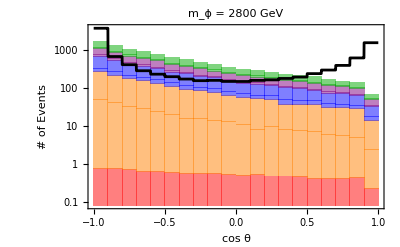

```mathematica
plt=Show[
Histogram[tst,{0.1},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None]//frametricknogrid,


(*Histogram[bkgtst,{0.1},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

```mathematica
Export["L_histogramcos_"<>ToString[mphitst]<>".pdf",plt]
```

L_histogramcos_2800.pdf

FOR BELOW, FOR 0.2 AND 2.8 TEV THE RANGE AND THE STEPSIZE AND THE NORMALIZATION FACTOR ADDED TO MAKE THE PDF FUNCTION WORK RIGHT ARE DIFFERENT. CHANGE FOR EACH

```mathematica
tst=weightedmixmaker[allhistogramdata["MT2"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["MT2"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=0;maxx=(*250*)2800;stepx=(*10*)100;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdataMT2["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataMT2["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataMT2["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

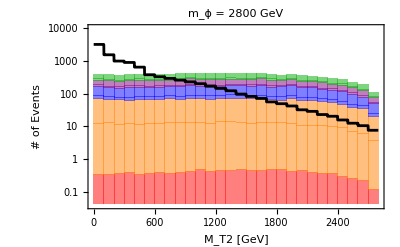

```mathematica
plt=Show[
Histogram[tst,{100(*100*)},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{3.9 10^-2,10000}]//frametricknogrid,

(*Histogram[bkgtst,{10},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,*)

Plot[ (*10^5*)10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]

]
```

```mathematica
Export["L_histogramMT2_"<>ToString[mphitst]<>".pdf",plt]
```

L_histogramMT2_2800.pdf

## Older histogs

```mathematica
tst=weightedmixmaker[allhistogramdata["pT"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["pT"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=0;maxx=10000;stepx=200;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.2 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdatapT["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdatapT["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdatapT["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

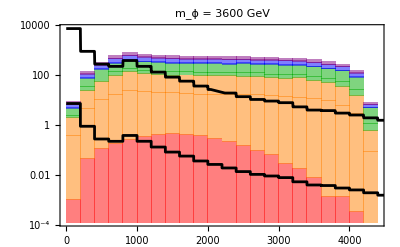

```mathematica
plt=Show[
Histogram[tst,{200},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Darker[Green],Darker[Green],Blue,Blue,Purple,Purple},ChartBaseStyle->EdgeForm[None],PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametricknogrid,

(*Histogram[bkgtst,{200},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[2 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log"]
]
```

```mathematica
tst=weightedmixmaker[allhistogramdata["pTll"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["pTll"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=0;maxx=10000;stepx=200;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdatapT["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdatapT["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdatapT["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

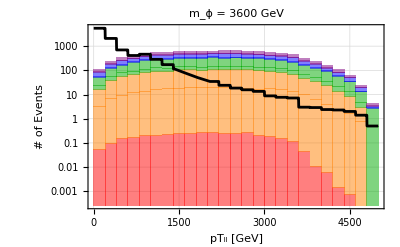

```mathematica
plt=Show[
Histogram[tst,{200},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Darker[Green],Darker[Green],Blue,Blue,Purple,Purple},ChartBaseStyle->EdgeForm[None],FrameLabel->{"pT_ll [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,

Histogram[bkgtst,{200},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"pT_ll [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,

Plot[2 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log"]
]
```

```mathematica
Export["histogrampTll_"<>ToString[mphitst]<>".pdf",plt]
```

histogrampTll_2000.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["mjj"]["L",mphitst],dataxsecall["L",mphitst]]
bkgtst=weightedmixmaker[{histogramdata["mjj"]["L","bkg_L_ll"]},{xsec["bkg_L_ll"]}]
minx=0;maxx=10000;stepx=300;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdatamjj["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdatamjj["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdatamjj["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

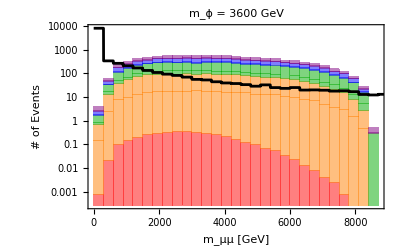

```mathematica
plt=Show[
Histogram[tst,{300},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Darker[Green],Darker[Green],Blue,Blue,Purple,Purple},ChartBaseStyle->EdgeForm[None],FrameLabel->{"m_μμ [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"(*,PlotRange->{1,10^4}*)]//frametricknogrid,

Histogram[bkgtst,{300},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"m_μμ [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,

Plot[3 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log"]
]
```

```mathematica
Export["histogrammll_"<>ToString[mphitst]<>".pdf",plt]
```

histogrammll_3600.pdf

## More checks with Aria: cuts

I compared the {mjj,pTll,MT2} for some random samples to what Aria had in her dilepton_summary.csv files: Complete agreement.
CHECK!

```mathematica
{#[[-1,2]],Norm[#[[3,2,1]]+#[[3,2,2]]],#[[-2,2]]}&/@evententry["L","bkg_L_cut200"][[{1,2,864,9865,49308,67000,-1}]]
```

{{3375.48,616.697,270.07},{1774.1,942.171,3.75554},{1559.23,1168.14,268.66},{6395.88,175.093,72.7133},{241.119,607.157,605.703},{374.57,583.64,574.631},{634.104,217.499,212.809}}

```mathematica
ariabkgevents=#[[{1,2,-1}]]&/@ToExpression[Import["../../../flavorDM2_lhe/mumu_to_mumuvv_cuts/Events/run_01/dilepton_summary.csv","CSV"]][[2;;-1]];
```

```mathematica
ariabkgevents[[{1,-1}]]
```

{{3375.48,616.697,270.067},{634.104,217.499,212.618}}

```mathematica
{#[[-1,2]],Norm[#[[3,2,1]]+#[[3,2,2]]],#[[-2,2]]}&/@evententry["L","bkg_L_ll"][[{1,2,864,9865,49308,67000,-1}]]
```

{{91.0028,217.921,134.597},{1458.21,1380.08,1120.21},{91.4251,136.908,119.705},{1874.67,1270.94,584.642},{89.6344,121.576,41.567},{90.4765,39.1705,33.2842},{3094.32,476.663,209.778}}

```mathematica
ariabkgllevents=#[[{1,2,-1}]]&/@ToExpression[Import["../../../flavorDM2_lhe/mumu_to_llvv/Events/run_02/dilepton_summary.csv","CSV"]][[2;;-1]];
```

```mathematica
ariabkgllevents[[{1,-1}]]
```

{{91.0028,217.921,134.597},{3094.32,476.663,209.759}}

# of events passing cuts: my different bkg files, and aria’s saved file for cut200 bkg.
Note that the other bkgs (bkg_L_old or bkg_L) are in the same ballpark. 
And they are a factor of 1/2 smaller than her table: cause of νl instead of νm? I think we should use νl since we dont detect neutrinos flavor?

```mathematica
tstcutmjj=1500;tstcutpTll=1300;tstcutMT2=3900;
```

```mathematica
Length[Select[evententry["L","bkg_L_ll"],tstcutmjj<=#[[-1,2]]&&tstcutpTll<=Norm[#[[3,2,1]]+#[[3,2,2]]]&&tstcutMT2<=#[[-2,2]]&]]/Length[evententry["L","bkg_L_ll"]] xsec["bkg_L_ll"] 10^7

Length[Select[ariabkgllevents,tstcutmjj<=#[[1]]&&tstcutpTll<=#[[2]]&&tstcutMT2<=#[[3]]&]]/Length[ariabkgllevents] xsec["bkg_L_ll"] 10^7
```

0.

0.

To better compare, removed the prefactors in the no-pdf case: first entry.
Factor of 6 smaller compared to arias table. why? Maybe cause She simulated l+l- vl vl~, which could have 6 combos compared to what Sam simulated?

```mathematica
(*If[#=="_switch_0_0",1/0.00606,1]*)4(*should multiply everything by this.*)Length[Select[evententry["L",1000,#],tstcutmjj<=#[[-1,2]]&&tstcutpTll<=Norm[#[[3,2,1]]+#[[3,2,2]]]&&tstcutMT2<=#[[-2,2]]&]]/Length[evententry["L",1000,#]] xsec["L_mphi_1000.0"<>#] 10^7&/@{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}
(*If[#=="_switch_0_0",1/0.00606,1] Length[Select[evententry["L",4400,#],tstcutmjj<=#[[-1,2]]&&tstcutpTll<=Norm[#[[3,2,1]]+#[[3,2,2]]]&&tstcutMT2<=#[[-2,2]]&]]/Length[evententry["L",4400,#]] xsec["L_mphi_4400.0"<>#] 10^7&/@{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}
If[#=="_switch_0_0",1/0.00606,1] Length[Select[evententry["L",4600,#],tstcutmjj<=#[[-1,2]]&&tstcutpTll<=Norm[#[[3,2,1]]+#[[3,2,2]]]&&tstcutMT2<=#[[-2,2]]&]]/Length[evententry["L",4600,#]] xsec["L_mphi_4600.0"<>#] 10^7&/@{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}*)
```

{4.1261,24.2343,35.0261,3.68227}

```mathematica
Tr[%]
```

67.0688

## New Cut Module and Reach Plots

```mathematica
gγ=-sw;gZL=1/(√(1-sw^2))(-1/2+sw^2);gZR=1/(√(1-sw^2))(sw^2);
```

```mathematica
(gγ^2+gZL^2)^2
(gγ^2+gZR^2)^2
(gγ^2+gZL gZR)^2
```

0.105414

0.0892225

0.0223056

```mathematica
alllabelslist
```

{L_mphi_4800.0_switch_0_0_L,L_mphi_4800.0_switch_0_1_L,L_mphi_4800.0_switch_1_0_L,L_mphi_4800.0_switch_1_1_L,L_mphi_4800.0_switch_0_0_R,L_mphi_4800.0_switch_0_1_R,L_mphi_4800.0_switch_1_0_R,L_mphi_4800.0_switch_1_1_R,L_mphi_4800.0_VBF}

```mathematica
evententry[fulllabel][[1]]
```

{{η,{-1.3335,-1.5179}},{pT,{626.356,284.377}},{pTvec,{{0,-215.88,-587.978,0},{0,123.396,256.21,0}}},{fourvec,{{1270.83,-215.88,-587.978,-1105.75},{679.915,123.396,256.21,-617.587}}},{ET,{626.356,284.377}},{beta,{1.,1.}},{gamma,{0.-102802. ⅈ,0.-546591. ⅈ}},{MT2,40.9056},{mjj,846.691}}

```mathematica
(*Clear[cutmodule]
cutmodule[modelLuQ_,mphi__,cutmjj_,cutpTll_,cutMT2_,etacut_,costhcut_][flagPDF_,minbkg_]:=Module[{},

alllabelslist={};
Do[Do[
fulllabel=If[LRRL=="VBF","L_mphi_"<>ToString[mphi]<>".0"<>label,"L_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL];
AppendTo[alllabelslist,fulllabel];

signalevents[fulllabel]=Select[evententry[fulllabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&-etacut<=#[[1,2,1]]<=etacut&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&];

(*Print["bkg passing cuts: "<>ToString[Length[signalevents[modelLuQ,mphi,channindx]]]];*)

aftercutweight[fulllabel]=Length[signalevents[fulllabel]]/Length[evententry[fulllabel]];

(*since 2 μ in the final state*)
evencount[fulllabel]=aftercutweight[fulllabel] xsec[fulllabel] 10^7 If[flagPDF==True,1,1/(coeff["_switch_0_0"]["L"][mphi])](*to get the noPDF case*);
(*Luminosity at a 10 TeV MuC in pb^-1*)

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];


bkgevents[modelLuQ]=Select[evententry[modelLuQ,"bkg_L_ll"],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&-etacut<=#[[1,2,1]]<=etacut&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&];

(*Print["bkg passing cuts: "<>ToString[Length[bkgevents[modelLuQ]]]];*)

aftercutweight["bkg_L_ll"]=Length[bkgevents[modelLuQ]]/Length[evententry[modelLuQ,"bkg_L_ll"]];

(*since 2 μ in the final state*)
evencount["bkg_L_ll"]=Max[minbkg,aftercutweight["bkg_L_ll"] xsec["bkg_L_ll"] 10^7];
(*Luminosity at a 10 TeV MuC in pb^-1*)


{{"Signal Count",Tr[Table[evencount[channindx],{channindx,If[flagPDF==True,alllabelslist,alllabelslist[[{1,5}]]]}]]},{"Bkg Count",evencount["bkg_L_ll"]}}

]*)
```

```mathematica
Clear[cutmodule]
cutmodule[modelLuQ_,mphi_,cutmjj_,cutpTll_,cutMT2_,etacut_,costhcut_,cuttotE_,cutMET_][flagPDF_,minbkg_]:=Module[{},

alllabelslist={};
Do[Do[
fulllabel=(*modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL*)If[LRRL=="VBF",modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label,modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL];
AppendTo[alllabelslist,fulllabel];

signalevents[fulllabel]=Select[evententry[fulllabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[signalevents[modelLuQ,mphi,channindx]]]];*)

aftercutweight[fulllabel]=Length[signalevents[fulllabel]]/Length[evententry[fulllabel]];

(*since 2 μ in the final state*)
evencount[fulllabel]=aftercutweight[fulllabel] xsec[fulllabel] 10^7 If[flagPDF==True,1,1/(coeff["_switch_0_0"]["L"][mphi])](*to get the noPDF case*);
(*Luminosity at a 10 TeV MuC in pb^-1*)

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];


bkgevents[modelLuQ]=Select[evententry[modelLuQ,bkglabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[bkgevents[modelLuQ]]]];*)

aftercutweight[bkglabel]=Length[bkgevents[modelLuQ]]/Length[evententry[modelLuQ,bkglabel]];

(*since 2 μ in the final state*)
evencount[bkglabel]=Max[minbkg,aftercutweight[bkglabel] xsec[bkglabel] 10^7];
(*Luminosity at a 10 TeV MuC in pb^-1*)


{{"Signal Count",Tr[Table[evencount[channindx],{channindx,If[flagPDF==True,alllabelslist,alllabelslist[[{1,5}]]]}]]},{"Bkg Count",evencount[bkglabel]}}

]
```

```mathematica
mphitst=700;
minbkgemodel=xsec["bkg_L_ll"] 10^7 10 10^-5;
cutmodule[modellabel,mphitst,{300,200000},{0,400000},{150,100000},0.3,Cos[π/180 160],{600,100000},{0,50000}][True,minbkgemodel][[{1,2},2]]
(%[[1]])/(√(%[[2]]))
```

{283.341,124.32}

25.412

{34.9343,36.96}

5.74628

Same SRs as the e model used (slightly less optimal but ok)

**Optimized for m=2.8 TeV: mjj > 300, pTll > 0, MT2> 800, |eta|<0.2, θ >130, El > 1800

{60.7887,36.96}

9.99901

**Optimized for m=0.2 TeV: mjj > 300, pTll > 0, MT2> 10, |eta|<0.5, θ >160, El > 500

{201.423,60.24}

25.9518

### PDF vs noPDF

New SRs

```mathematica
(*nopdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{10,100000},0.5,Cos[π/180 160],{500,100000},{0,50000}][False,40][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
nopdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{1000,100000},0.2,Cos[π/180 130],{800,100000},{0,50000}][False,40][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];*)
```

```mathematica
pdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{150,100000},0.3,Cos[π/180 160],{600,100000},{0,50000}][True,40][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
pdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{1000,100000},0.2,Cos[π/180 130],{800,100000},{0,50000}][True,40][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

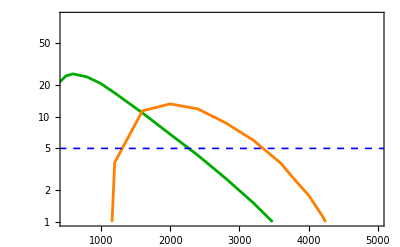

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1,Joined->True,PlotRange->{{500,5000},{1,90}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\sigma",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Significance} ~ (L~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,

LogPlot[5,{x,0,10^4},PlotStyle->{Dashed,Thickness[0.003],Blue}],

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^\\ell",FontSize->16],MaTeX["\\mathrm{SR}_2^\\ell",FontSize->16]}],{0.8,0.8}]]
```

```mathematica
Export["L_sig_reach.pdf",plt]
```

L_sig_reach.pdf

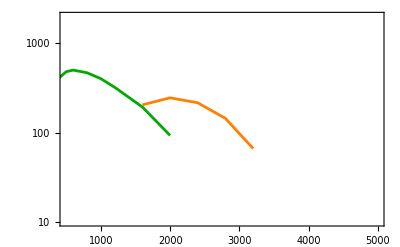

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR1,Joined->True,PlotRange->{{500,5000},{10,2000}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\mathrm{sys.}/\\mathrm{stat.}~[\\%]",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Tolerable~Systematics} ~ (L~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR2,Joined->True,PlotStyle->{{Orange}}]//frametricknogrid,

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^\\ell",FontSize->16],MaTeX["\\mathrm{SR}_2^\\ell",FontSize->16]}],{0.8,0.8}]]
```

```mathematica
Export["tolerated_L.pdf",plt]
```

tolerated_L.pdf

### SRs reach

SR200

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={100,100000};
etacutSR=0.3;
coscutSR=Cos[π/180 160];
```

```mathematica
dataSR200=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{1.53745,60.24}},{200,{201.423,60.24}},{300,{285.573,60.24}},{400,{311.584,60.24}},{500,{314.538,60.24}},{600,{298.593,60.24}},{800,{256.573,60.24}},{1000,{213.613,60.24}},{1200,{171.939,60.24}},{1600,{109.053,60.24}},{2000,{67.2295,60.24}},{2400,{42.2668,60.24}},{2800,{25.1495,60.24}},{3200,{15.3297,60.24}},{3600,{8.23689,60.24}},{4000,{3.53732,60.24}},{4400,{1.28243,60.24}},{4800,{0.17394,60.24}}}

```mathematica
sysfraction200={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR200
```

{{100,0.},{200,509.312},{300,729.051},{400,796.652},{500,804.322},{600,762.9},{800,653.542},{1000,541.287},{1200,431.626},{1600,262.618},{2000,141.464},{2400,43.1557},{2800,0.},{3200,0.},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

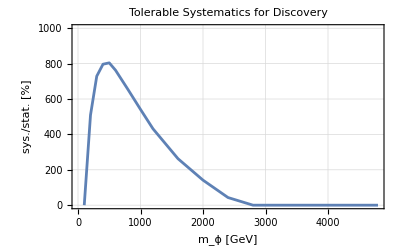

```mathematica
ListPlot[sysfraction200,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

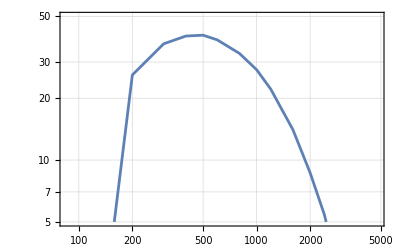

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR200,Joined->True,PlotRange->{5,50}]//frametrick
```

SR2800

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={700,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 120];
```

```mathematica
dataSR2800=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40.16}},{200,{0.,40.16}},{300,{0.,40.16}},{400,{0.,40.16}},{500,{0.,40.16}},{600,{0.,40.16}},{800,{19.1563,40.16}},{1000,{66.8356,40.16}},{1200,{92.5872,40.16}},{1600,{115.406,40.16}},{2000,{107.497,40.16}},{2400,{88.9282,40.16}},{2800,{67.3912,40.16}},{3200,{45.3082,40.16}},{3600,{26.2088,40.16}},{4000,{14.3701,40.16}},{4400,{5.2646,40.16}},{4800,{0.744566,40.16}}}

```mathematica
sysfraction2800={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR2800
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,0.},{1000,185.72},{1200,274.559},{1600,350.222},{2000,324.185},{2400,262.235},{2800,187.71},{3200,102.208},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

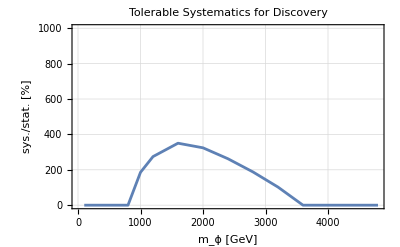

```mathematica
ListPlot[sysfraction2800,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

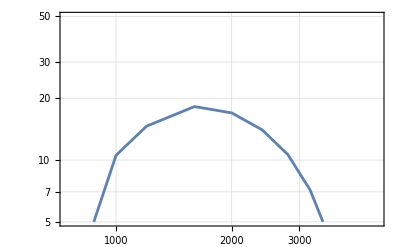

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR2800,Joined->True,PlotRange->{5,50}]//frametrick
```

SR3600

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={600,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 130];
```

```mathematica
dataSR3600=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40}},{200,{0.,40}},{300,{0.,40}},{400,{0.,40}},{500,{0.,40}},{600,{0.,40}},{800,{49.8266,40}},{1000,{92.3356,40}},{1200,{109.471,40}},{1600,{116.803,40}},{2000,{100.998,40}},{2400,{77.9031,40}},{2800,{55.8582,40}},{3200,{36.5984,40}},{3600,{20.8445,40}},{4000,{10.8762,40}},{4400,{3.78136,40}},{4800,{0.545746,40}}}

```mathematica
sysfraction3600={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR3600
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,121.766},{1000,274.333},{1200,331.421},{1600,355.57},{2000,303.323},{2400,225.142},{2800,145.607},{3200,58.2619},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

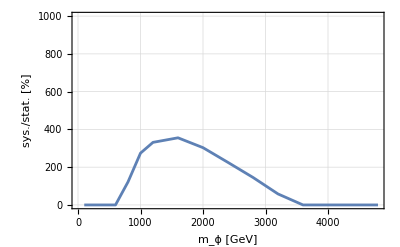

```mathematica
ListPlot[sysfraction3600,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"}]//frametrick
```

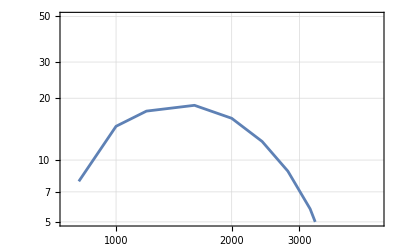

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR3600,Joined->True,PlotRange->{5,50}]//frametrick
```

### Other

```mathematica
Do[

 Print[xsec["L_mphi_"<>ToString[mphitst]<>".0"<>channindx] ]

,{channindx,listlabels[[2;;4]]}]
```

2.62474×10^-7

1.67179×10^-6

2.60301×10^-6

Check SRs

```mathematica
mjjtst=990;
(*probably 2 i add above was already in her xsec. she found σ~0.2*)
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{3500,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{1800,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{200,100000}][[{1,2},2]]&/@{1300,750,200}
```

{{0.,0.},{0.,0.},{0.,0.}}

{{0.,2040.},{0.,2040.},{0.,2040.}}

{{7.04978,20300.},{9.96491,49510.},{12.041,66040.}}

{{0.,70.7547},{0.,70.7547},{0.,70.7547}}

{{0.,2031.67},{0.,2031.67},{0.,2031.67}}

{{7.04978,20306.6},{9.96491,49386.8},{12.041,66256.7}}

### Plots

```mathematica
tablescanmjjptMT2in[mphi_][mjjmax_,ptmax_,MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){mjjscan,ptscan,cutmodule["L",mphi,{mjjscan,mjjmax},{ptscan,ptmax},MT2range,0.2,Cos[π/180 150]][[{1,2},2]]},{mjjscan,0,2000,250},{ptscan,0,2000,250}],1]
tablescanetacosthMT2in[mphi_][MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){etascan,cosscan,cutmodule["L",mphi,{100,100000},{0,100000},MT2range,etascan,cosscan][[{1,2},2]]},{etascan,0.1,0.8,0.1},{cosscan,-0.9,-0.0,0.1}],1]
```

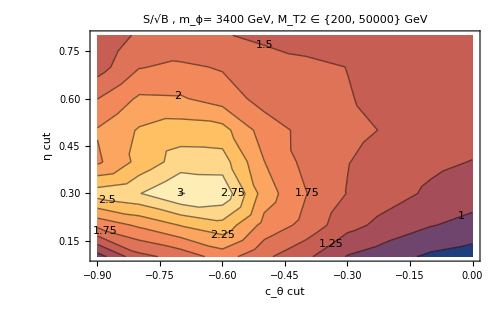
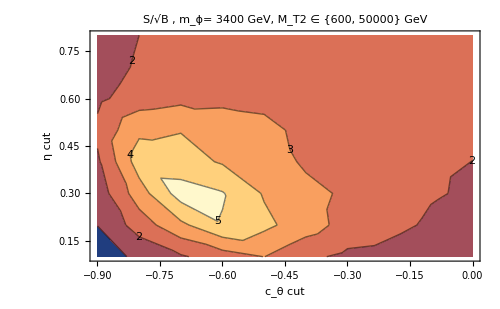
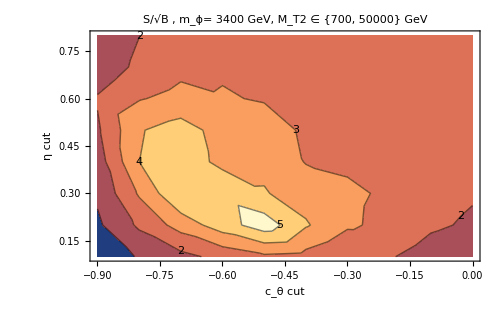
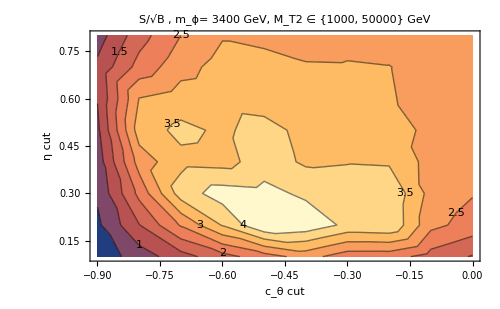

```mathematica
mphitst=3400;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{200,50000},{600,50000},{700,50000},{1000,50000}}}]
```

```mathematica
sw^2
√(1-sw^2)
```

0.23

0.877496

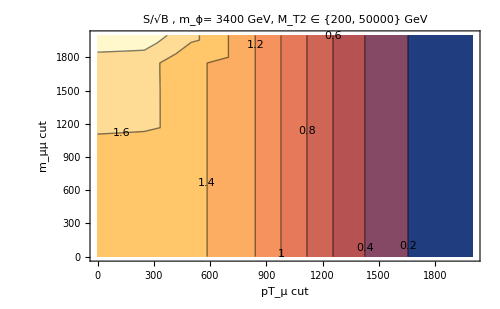
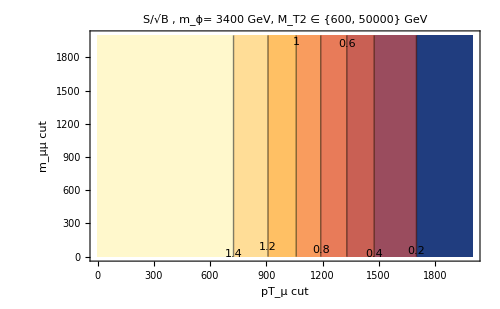
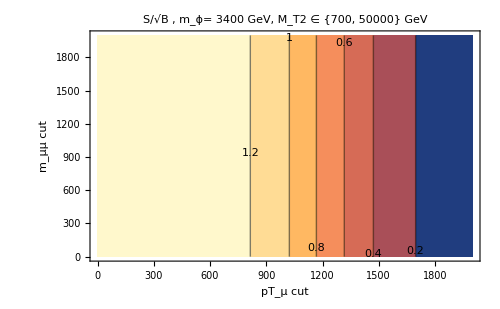
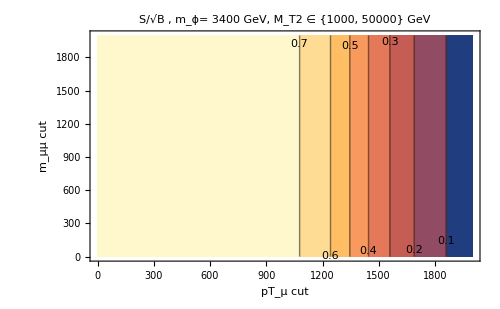

```mathematica
mphitst=3400;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanmjjptMT2in[mphitst][80000,50000,mt2R],FrameLabel->{"pT_μ cut","m_μμ cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{200,50000},{600,50000},{700,50000},{1000,50000}}}]
```

no η or cosθ cuts: really not doing that well.

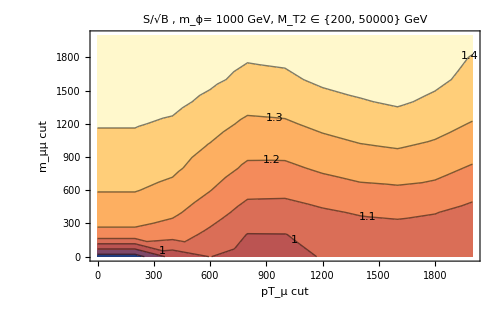
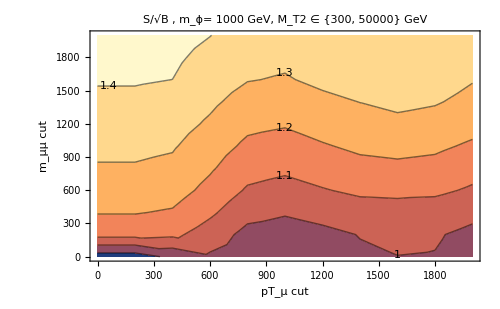
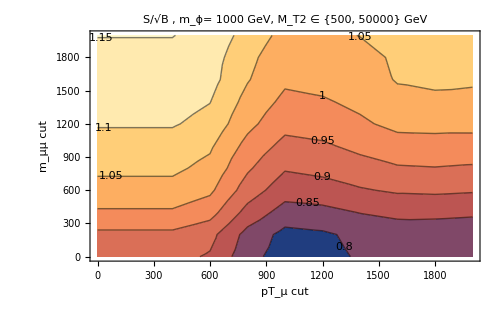
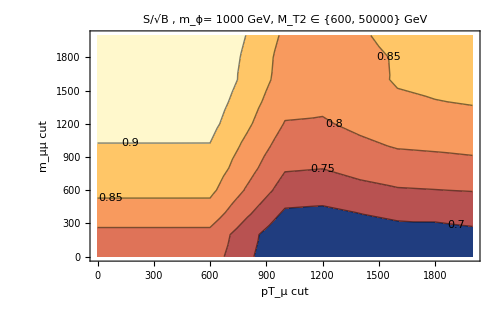

Cuts optimizing m=1TeV: mjj> 3000, pTll>500,MT2>200,|η|<0.5, cosθ < -0.8

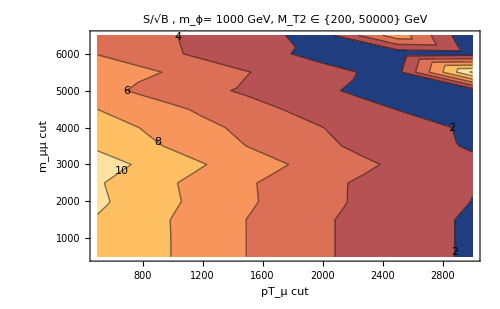
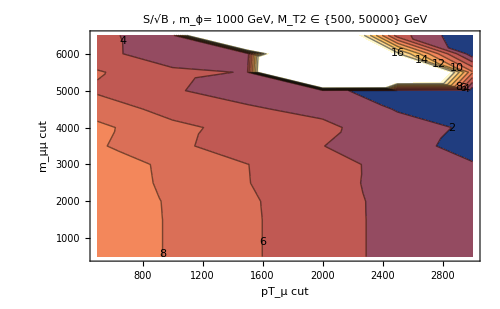

## Histograms 2D

```mathematica
tst=Table[{RandomReal[{0,1}],RandomReal[{0,1}]},{i,1,1000}];
```

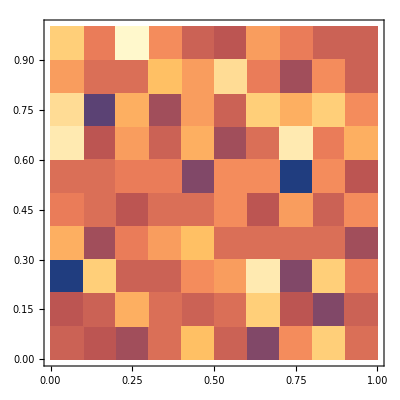

```mathematica
DensityHistogram[tst]
```

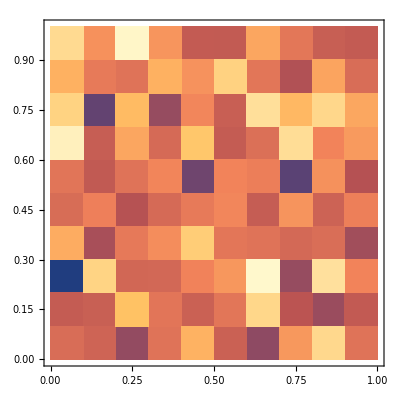

```mathematica
tstw=Table[RandomReal[{4,10}],{i,1,1000}];
DensityHistogram[WeightedData[tst,tstw]]
```

```mathematica
?weightedmixmaker
```

```mathematica
testmass=500;
tst=weightedmixmaker[allhistogram2DdataMT2mjj["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdataMT2mjj["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

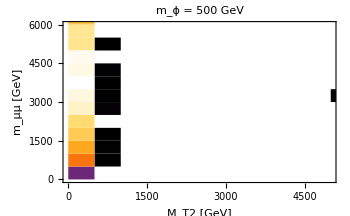
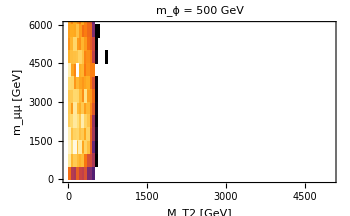
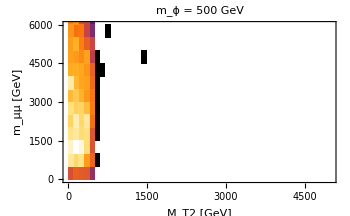

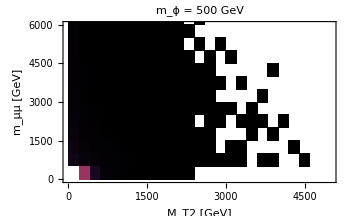

```mathematica
(DensityHistogram[#,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","m_μμ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst 
DensityHistogram[bkgtst[[1]],PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","m_μμ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

```mathematica
tst=weightedmixmaker[allhistogram2DdataMT2pT["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdataMT2pT["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

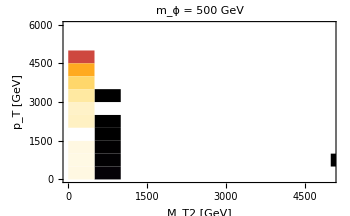
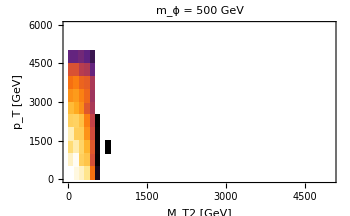
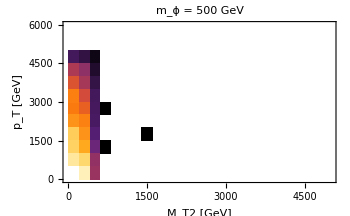

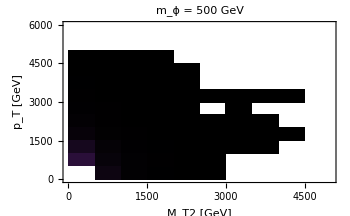

```mathematica
(DensityHistogram[#,{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst
DensityHistogram[bkgtst[[1]],{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

```mathematica
tst=weightedmixmaker[allhistogram2DdatamjjpT["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdatamjjpT["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

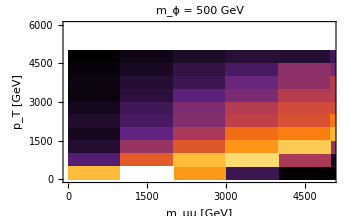
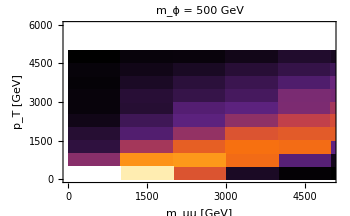
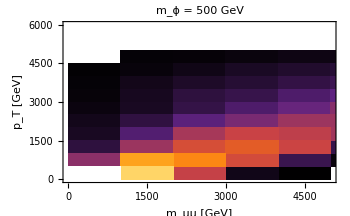

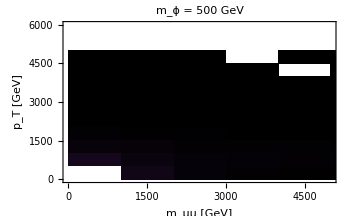

```mathematica
(DensityHistogram[#,{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"m_μμ [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst
DensityHistogram[bkgtst[[1]],{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"m_μμ [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

## Making the Tolerable Error Plots: After SRs identified

For each mass point: 
	Should first run the above module to get the total event count for the SR
	use the formula below to find the tolerable systematics as a fraction of statistics error √B. 
	Automatically returns a complex number if no discovery is possible somewhere in that SR.
	Repeat this for each mass point: the end result should be a list with masses of χ and ϕ, B and S (for sanity checks), and the tolerable x.
	Repeat this for each SR.

```mathematica
x/.Solve[S/(√((1+x^2)B))==5,x][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(-25 B+S^2))/(5 √B)

## 2D Histograms older

```mathematica
combodata[listlabels[[1]]]
```

```mathematica
combodata[listlabels[[2]]]
```

```mathematica
mt2=Table[RandomReal[{2,6}]{RandomReal[{0,1}],1},{i,1,10000}];
tstbkg=Table[{RandomReal[{2,3}],RandomReal[{1,2}]},{i,1,10000}];
```

```mathematica
mt2mjjH2D={#[[1]],#[[2]]}&/@combodata[listlabels[[2]]];
mt2mjjH2Dbkg={#[[1]],#[[2]]}&/@combodata[listlabels[[1]]];
mt2pTH2D={#[[1]],#[[3]]}&/@combodata[listlabels[[2]]];
mt2pTH2Dbkg={#[[1]],#[[3]]}&/@combodata[listlabels[[1]]];
mjjpTH2D={#[[2]],#[[3]]}&/@combodata[listlabels[[2]]];
mjjpTH2Dbkg={#[[2]],#[[3]]}&/@combodata[listlabels[[1]]];
```

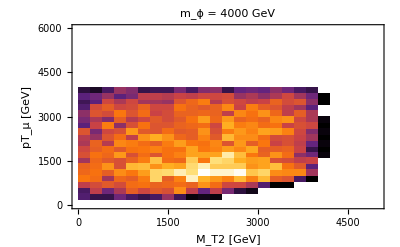

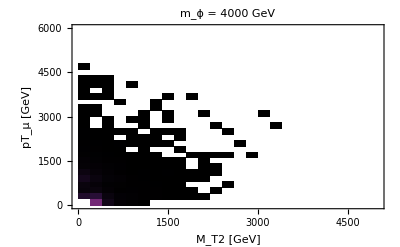

```mathematica
DensityHistogram[mt2pTH2D,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","pT_μ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = 4000 GeV"]//frametricknogrid
DensityHistogram[mt2pTH2Dbkg,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","pT_μ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = 4000 GeV"]//frametricknogrid
```

```mathematica
xsec[listlabels[[2]]]
xsec["bkg_L"]
```

8.89269×10^-6

0.101078

# LLP L Model: skip - done by Aria

## LLP Importmodeul

```mathematica
(*name: is the address and the name of the file from the notebook directory. label: is the label for that lhe file*. finalindices: {1,2,3,...} particles from the event to keep. *)
Clear[LLPimportmodule]
LLPimportmodule[name_,label_]:=Module[{},
SetDirectory[NotebookDirectory[]];
lhefile[label]=Import[name,"Table"];
allplist[label]=ReadME[lhefile[label]];

(*Print["0"];*)

outlist[label]=Select[Select[#,Abs[#[[1]]]==9000006&]&/@allplist[label],NumberQ[#[[1,1]]]&]//Quiet;
(*The second select is to drop events that for some reason failed in the LHE file and have no mediator at the position I expected.*)

(*Print["0"];*)

fourvecslist[label]=(#//fourvecs)&/@outlist[label][[1;;-2]];
(*fourvecslist[label]=Table[fourvecslist[label][[i,finalindices]],{i,1,Length[fourvecslist[label]]}];*)

etalist[label]=(#//eta)&/@outlist[label][[1;;-2]];
(*Print["0"];*)

betalist[label]=(#//beta)&/@outlist[label][[1;;-2]];
(*betalist[label]=Table[betalist[label][[i,finalindices]],{i,1,Length[betalist[label]]}];*)

(*Print["0"];*)

gammalist[label]=(#//gamma)&/@outlist[label][[1;;-2]];
(*gammalist[label]=Table[gammalist[label][[i,finalindices]],{i,1,Length[gammalist[label]]}];*)

]
```

## Sanity tests of the module

```mathematica
listinputs//Length
```

132

```mathematica
tstfile=listinputs[[32,1]]
tstlabel=listinputs[[32,2]]
```

../../../flavorDM2_lhe/Events/run_63/unweighted_events.lhe

LLP_L_mphi_700.0_switch_0_1

```mathematica
LLPimportmodule[tstfile,tstlabel]
```

```mathematica
Select[outlist[tstlabel],Length[#]==1&]//Length
Position[(Length[#]&/@outlist[tstlabel]),1]
```

366

{{18},{45},{57},{59},{77},{111},{122},{138},{161},{186},{202},{239},{277},{303},{317},{368},{400},{416},{426},{428},{494},{576},{587},{604},{638},{640},{657},{722},{727},{744},{760},{773},{780},{785},{796},{815},{830},{868},{869},{953},{1041},{1094},{1095},{1098},{1155},{1171},{1227},{1307},{1324},{1353},{1372},{1378},{1391},{1395},{1419},{1443},{1456},{1490},{1519},{1536},{1550},{1652},{1657},{1703},{1705},{1707},{1714},{1734},{1767},{1877},{1903},{1911},{1941},{2012},{2067},{2071},{2085},{2104},{2125},{2126},{2146},{2187},{2193},{2268},{2292},{2306},{2327},{2421},{2482},{2487},{2507},{2541},{2554},{2583},{2626},{2648},{2656},{2680},{2691},{2700},{2717},{2730},{2732},{2803},{2808},{2812},{2814},{2815},{2867},{2901},{2905},{2928},{2983},{3021},{3082},{3089},{3111},{3126},{3151},{3153},{3177},{3222},{3238},{3299},{3339},{3401},{3427},{3436},{3512},{3533},{3550},{3604},{3620},{3625},{3665},{3671},{3680},{3700},{3702},{3744},{3770},{3793},{3828},{3843},{3845},{3875},{3877},{3886},{3916},{3944},{3951},{3989},{4004},{4015},{4016},{4019},{4062},{4075},{4092},{4147},{4179},{4216},{4226},{4254},{4257},{4321},{4410},{4425},{4436},{4457},{4533},{4556},{4599},{4610},{4640},{4664},{4679},{4736},{4741},{4763},{4772},{4791},{4832},{4850},{4874},{4893},{4910},{4944},{4961},{5044},{5055},{5057},{5107},{5129},{5133},{5139},{5162},{5166},{5206},{5238},{5249},{5272},{5317},{5323},{5327},{5345},{5361},{5407},{5501},{5564},{5597},{5627},{5699},{5742},{5772},{5815},{5878},{5895},{5901},{5923},{5924},{5951},{5968},{5982},{6011},{6035},{6048},{6071},{6101},{6123},{6135},{6136},{6171},{6190},{6191},{6207},{6264},{6275},{6471},{6491},{6492},{6516},{6555},{6563},{6575},{6597},{6604},{6616},{6620},{6642},{6647},{6717},{6735},{6791},{6806},{6823},{6863},{6870},{6956},{6960},{7073},{7125},{7150},{7177},{7223},{7235},{7324},{7337},{7345},{7367},{7374},{7380},{7381},{7383},{7452},{7476},{7484},{7485},{7524},{7565},{7708},{7732},{7746},{7800},{7802},{7805},{7819},{7826},{7849},{7866},{7878},{7903},{7913},{7935},{7950},{7955},{8001},{8053},{8146},{8148},{8163},{8184},{8188},{8190},{8196},{8200},{8216},{8228},{8238},{8252},{8282},{8297},{8299},{8315},{8340},{8341},{8349},{8351},{8354},{8355},{8438},{8490},{8519},{8523},{8580},{8659},{8684},{8768},{8788},{8791},{8800},{8873},{8941},{8969},{9017},{9028},{9032},{9046},{9047},{9061},{9085},{9117},{9133},{9222},{9227},{9303},{9333},{9336},{9372},{9386},{9421},{9428},{9477},{9506},{9533},{9539},{9614},{9615},{9696},{9805},{9895},{9914},{9922},{9954},{9970},{9985}}

```mathematica
gammalist[tstlabel]
```

```mathematica
Sort[Select[gammalist[tstlabel],Length[#]==1&]//Flatten,#1>=#2&]
```

{7.14301,7.14293,7.14291,7.1429,7.14288,7.14287,7.14287,7.14287,7.14287,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14285,7.14284,7.14284,7.14284,7.14284,7.14284,7.14284,7.14284,7.14284,7.14284,7.14283,7.14283,7.14283,7.14283,7.14283,7.14283,7.14282,7.14282,7.14282,7.14282,7.14282,7.14281,7.14281,7.14281,7.1428,7.1428,7.1428,7.1428,7.1428,7.14279,7.14279,7.14278,7.14278,7.14278,7.14277,7.14277,7.14277,7.14277,7.14277,7.14276,7.14276,7.14275,7.14275,7.14274,7.14274,7.14274,7.14274,7.14273,7.14272,7.1427,7.14268,7.14265,7.14264,7.14264,7.14263,7.14261,7.14257,7.14257,7.14257,7.14256,7.14254,7.14251,7.14249,7.14245,7.14244,7.14243,7.14242,7.1424,7.14233,7.14231,7.1423,7.1423,7.14218,7.14217,7.14216,7.14211,7.14211,7.1421,7.1421,7.14202,7.142,7.14195,7.14156,7.14145,7.14141,7.14128,7.14125,7.14124,7.14122,7.14115,7.14107,7.14103,7.14097,7.14087,7.14078,7.14077,7.14074,7.14058,7.14052,7.14048,7.14047,7.14041,7.14034,7.14023,7.14022,7.14017,7.14007,7.14006,7.13992,7.13984,7.13979,7.13975,7.13975,7.13961,7.13944,7.13918,7.13874,7.13853,7.13837,7.13833,7.13817,7.13806,7.138,7.13775,7.1377,7.1377,7.13737,7.13737,7.13648,7.13626,7.13568,7.13563,7.1354,7.13489,7.13481,7.13471,7.13379,7.13321,7.13272,7.1326,7.13115,7.13101,7.13009,7.13008,7.12932,7.12784,7.12728,7.1271,7.12578,7.12421,7.12414,7.12196,7.12148,7.12076,7.1201,7.1177,7.11757,7.11705,7.11596,7.11587,7.11554,7.11121,7.11086,7.11054,7.10827,7.1064,7.10246,7.10041,7.09995,7.09957,7.09693,7.09545,7.09325,7.08943,7.0885,7.08841,7.08722,7.08562,7.0802,7.07751,7.07695,7.07214,7.07053,7.07037,7.06782,7.06503,7.06101,7.05789,7.05743,7.05219,7.05169,7.0508,7.04411,7.04375,7.04148,7.03651,7.03282,7.02236,7.01684,7.01141,7.00921,7.00644,7.00583,6.97623,6.97583,6.96614,6.96277,6.96058,6.95655,6.92466,6.9212,6.91975,6.90092,6.8907,6.88975,6.87014,6.86502,6.86366,6.83691,6.83661,6.83012,6.82992,6.82334,6.81779,6.81594,6.73809,6.73162,6.72579,6.72213,6.71887,6.67253,6.6398,6.60067,6.5725,6.54844,6.52766,6.48486,6.44235,6.43183,6.43061,6.41363,6.36065,6.30678,6.30628,6.26372,6.25375,6.15091,6.08922,6.08436,6.08044,6.01717,5.89371,5.80226,5.768,5.74043,5.71024,5.68337,5.68211,5.6796,5.63713,5.63026,5.58496,5.57074,5.53319,5.48876,5.44472,5.41552,5.40223,5.37318,5.36794,5.28002,5.24739,5.24636,5.17742,5.14747,5.12808,5.05786,5.05317,4.96107,4.91988,4.91632,4.88705,4.83805,4.82617,4.80992,4.79314,4.71542,4.66833,4.56207,4.3603,4.3156,4.22103,4.20652,4.17717,4.04445,4.02412,3.88413,3.88171,3.86203,3.69355,3.54142,3.46519,3.42582,3.16481,3.10262,3.09588,3.07158,3.03778,2.98677,2.96952,2.92497,2.72704,2.58857,1.82696}

```mathematica
Select[(#[[1,1]]&/@outlist[tstlabel]),!NumberQ[#]&]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧}

## Reading LHE

```mathematica
listlabels={"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"};
```

```mathematica
allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union
(*allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union*)
masslist=allmasses;
```

{100,125,150,175,200,225,250,275,300,325,350,400,450,500,550,600,650,700,750,800,900,1000,1100,1200,1300,1400,1500,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

μμ initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
guide=Import["../../../flavorDM2_lhe/cross_section_muLmuR_to_phipphim_chichimumu.txt","Table"][[2;;-1]];
(*testmassstring="2000.0";*)
```

```mathematica
(*2 for 10 - another 2 for LR helicities on all files*)
coeff["_switch_0_0"]=2 0.00606;
coeff["_switch_0_1"]=2 2 0.055;
coeff["_switch_1_1"]=2 0.5;
```

```mathematica
listinputs={};
Do[
Do[
tst=Select[guide,#[[2]]=="mphi_"<>ToString[masses]<>".0"<>labelappend&];
tstdirectory=tst[[1,1]];
tstlabel="LLP_L_"<>tst[[1,2]];
xsec[tstlabel]=coeff[labelappend]tst[[1,3]];
AppendTo[listinputs,{"../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,xsec[tstlabel]}]
,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_1"}}]

,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

{{../../../flavorDM2_lhe/Events/run_01/unweighted_events.lhe,LLP_L_mphi_100.0_switch_0_0,2.80024×10^-7},{../../../flavorDM2_lhe/Events/run_46/unweighted_events.lhe,LLP_L_mphi_100.0_switch_0_1,1.99438×10^-6},{../../../flavorDM2_lhe/Events/run_136/unweighted_events.lhe,LLP_L_mphi_100.0_switch_1_1,3.30557×10^-6},{../../../flavorDM2_lhe/Events/run_03/unweighted_events.lhe,LLP_L_mphi_150.0_switch_0_0,2.78741×10^-7},{../../../flavorDM2_lhe/Events/run_48/unweighted_events.lhe,LLP_L_mphi_150.0_switch_0_1,1.98584×10^-6},{../../../flavorDM2_lhe/Events/run_138/unweighted_events.lhe,LLP_L_mphi_150.0_switch_1_1,3.29642×10^-6},{../../../flavorDM2_lhe/Events/run_05/unweighted_events.lhe,LLP_L_mphi_200.0_switch_0_0,2.7781×10^-7},{../../../flavorDM2_lhe/Events/run_50/unweighted_events.lhe,LLP_L_mphi_200.0_switch_0_1,1.96898×10^-6},{../../../flavorDM2_lhe/Events/run_140/unweighted_events.lhe,LLP_L_mphi_200.0_switch_1_1,3.29043×10^-6},{../../../flavorDM2_lhe/Events/run_07/unweighted_events.lhe,LLP_L_mphi_250.0_switch_0_0,2.77246×10^-7},{../../../flavorDM2_lhe/Events/run_52/unweighted_events.lhe,LLP_L_mphi_250.0_switch_0_1,1.94928×10^-6},{../../../flavorDM2_lhe/Events/run_142/unweighted_events.lhe,LLP_L_mphi_250.0_switch_1_1,3.24748×10^-6},{../../../flavorDM2_lhe/Events/run_09/unweighted_events.lhe,LLP_L_mphi_300.0_switch_0_0,2.76654×10^-7},{../../../flavorDM2_lhe/Events/run_54/unweighted_events.lhe,LLP_L_mphi_300.0_switch_0_1,1.93171×10^-6},{../../../flavorDM2_lhe/Events/run_144/unweighted_events.lhe,LLP_L_mphi_300.0_switch_1_1,3.19105×10^-6},{../../../flavorDM2_lhe/Events/run_11/unweighted_events.lhe,LLP_L_mphi_350.0_switch_0_0,2.76292×10^-7},{../../../flavorDM2_lhe/Events/run_56/unweighted_events.lhe,LLP_L_mphi_350.0_switch_0_1,1.91322×10^-6},{../../../flavorDM2_lhe/Events/run_146/unweighted_events.lhe,LLP_L_mphi_350.0_switch_1_1,3.1373×10^-6},{../../../flavorDM2_lhe/Events/run_12/unweighted_events.lhe,LLP_L_mphi_400.0_switch_0_0,2.75782×10^-7},{../../../flavorDM2_lhe/Events/run_57/unweighted_events.lhe,LLP_L_mphi_400.0_switch_0_1,1.88931×10^-6},{../../../flavorDM2_lhe/Events/run_147/unweighted_events.lhe,LLP_L_mphi_400.0_switch_1_1,3.08794×10^-6},{../../../flavorDM2_lhe/Events/run_13/unweighted_events.lhe,LLP_L_mphi_450.0_switch_0_0,2.75452×10^-7},{../../../flavorDM2_lhe/Events/run_58/unweighted_events.lhe,LLP_L_mphi_450.0_switch_0_1,1.87302×10^-6},{../../../flavorDM2_lhe/Events/run_148/unweighted_events.lhe,LLP_L_mphi_450.0_switch_1_1,3.0382×10^-6},{../../../flavorDM2_lhe/Events/run_14/unweighted_events.lhe,LLP_L_mphi_500.0_switch_0_0,2.74951×10^-7},{../../../flavorDM2_lhe/Events/run_59/unweighted_events.lhe,LLP_L_mphi_500.0_switch_0_1,1.85426×10^-6},{../../../flavorDM2_lhe/Events/run_149/unweighted_events.lhe,LLP_L_mphi_500.0_switch_1_1,2.98735×10^-6},{../../../flavorDM2_lhe/Events/run_16/unweighted_events.lhe,LLP_L_mphi_600.0_switch_0_0,2.72907×10^-7},{../../../flavorDM2_lhe/Events/run_61/unweighted_events.lhe,LLP_L_mphi_600.0_switch_0_1,1.81964×10^-6},{../../../flavorDM2_lhe/Events/run_151/unweighted_events.lhe,LLP_L_mphi_600.0_switch_1_1,2.90863×10^-6},{../../../flavorDM2_lhe/Events/run_18/unweighted_events.lhe,LLP_L_mphi_700.0_switch_0_0,2.71293×10^-7},{../../../flavorDM2_lhe/Events/run_63/unweighted_events.lhe,LLP_L_mphi_700.0_switch_0_1,1.78377×10^-6},{../../../flavorDM2_lhe/Events/run_153/unweighted_events.lhe,LLP_L_mphi_700.0_switch_1_1,2.8309×10^-6},{../../../flavorDM2_lhe/Events/run_20/unweighted_events.lhe,LLP_L_mphi_800.0_switch_0_0,2.68709×10^-7},{../../../flavorDM2_lhe/Events/run_65/unweighted_events.lhe,LLP_L_mphi_800.0_switch_0_1,1.74065×10^-6},{../../../flavorDM2_lhe/Events/run_155/unweighted_events.lhe,LLP_L_mphi_800.0_switch_1_1,2.74629×10^-6},{../../../flavorDM2_lhe/Events/run_21/unweighted_events.lhe,LLP_L_mphi_900.0_switch_0_0,2.65529×10^-7},{../../../flavorDM2_lhe/Events/run_66/unweighted_events.lhe,LLP_L_mphi_900.0_switch_0_1,1.70314×10^-6},{../../../flavorDM2_lhe/Events/run_156/unweighted_events.lhe,LLP_L_mphi_900.0_switch_1_1,2.67497×10^-6},{../../../flavorDM2_lhe/Events/run_22/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_0_0,2.62474×10^-7},{../../../flavorDM2_lhe/Events/run_67/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_0_1,1.67179×10^-6},{../../../flavorDM2_lhe/Events/run_157/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_1_1,2.60301×10^-6},{../../../flavorDM2_lhe/Events/run_24/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_0_0,2.55128×10^-7},{../../../flavorDM2_lhe/Events/run_69/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_0_1,1.60052×10^-6},{../../../flavorDM2_lhe/Events/run_159/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_1_1,2.45011×10^-6},{../../../flavorDM2_lhe/Events/run_26/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_0_0,2.46511×10^-7},{../../../flavorDM2_lhe/Events/run_71/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_0_1,1.51794×10^-6},{../../../flavorDM2_lhe/Events/run_161/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_1_1,2.29651×10^-6},{../../../flavorDM2_lhe/Events/run_28/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_0_0,2.36635×10^-7},{../../../flavorDM2_lhe/Events/run_73/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_0_1,1.43809×10^-6},{../../../flavorDM2_lhe/Events/run_163/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_1_1,2.1537×10^-6},{../../../flavorDM2_lhe/Events/run_29/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_0_0,2.2553×10^-7},{../../../flavorDM2_lhe/Events/run_74/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_0_1,1.35423×10^-6},{../../../flavorDM2_lhe/Events/run_164/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_1_1,2.00578×10^-6},{../../../flavorDM2_lhe/Events/run_30/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_0_0,2.13611×10^-7},{../../../flavorDM2_lhe/Events/run_75/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_0_1,1.26515×10^-6},{../../../flavorDM2_lhe/Events/run_165/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_1_1,1.85129×10^-6},{../../../flavorDM2_lhe/Events/run_31/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_0_0,2.00359×10^-7},{../../../flavorDM2_lhe/Events/run_76/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_0_1,1.17296×10^-6},{../../../flavorDM2_lhe/Events/run_166/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_1_1,1.69402×10^-6},{../../../flavorDM2_lhe/Events/run_32/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_0_0,1.86609×10^-7},{../../../flavorDM2_lhe/Events/run_77/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_0_1,1.0797×10^-6},{../../../flavorDM2_lhe/Events/run_167/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_1_1,1.53744×10^-6},{../../../flavorDM2_lhe/Events/run_33/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_0_0,1.71654×10^-7},{../../../flavorDM2_lhe/Events/run_78/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_0_1,9.79537×10^-7},{../../../flavorDM2_lhe/Events/run_168/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_1_1,1.38383×10^-6},{../../../flavorDM2_lhe/Events/run_34/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_0_0,1.56571×10^-7},{../../../flavorDM2_lhe/Events/run_79/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_0_1,8.77543×10^-7},{../../../flavorDM2_lhe/Events/run_169/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_1_1,1.22316×10^-6},{../../../flavorDM2_lhe/Events/run_35/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_0_0,1.40613×10^-7},{../../../flavorDM2_lhe/Events/run_80/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_0_1,7.80661×10^-7},{../../../flavorDM2_lhe/Events/run_170/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_1_1,1.07265×10^-6},{../../../flavorDM2_lhe/Events/run_36/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_0_0,1.24159×10^-7},{../../../flavorDM2_lhe/Events/run_81/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_0_1,6.80574×10^-7},{../../../flavorDM2_lhe/Events/run_171/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_1_1,9.19681×10^-7},{../../../flavorDM2_lhe/Events/run_37/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_0_0,1.07779×10^-7},{../../../flavorDM2_lhe/Events/run_82/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_0_1,5.7882×10^-7},{../../../flavorDM2_lhe/Events/run_172/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_1_1,7.75301×10^-7},{../../../flavorDM2_lhe/Events/run_38/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_0_0,9.11103×10^-8},{../../../flavorDM2_lhe/Events/run_83/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_0_1,4.81567×10^-7},{../../../flavorDM2_lhe/Events/run_173/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_1_1,6.32706×10^-7},{../../../flavorDM2_lhe/Events/run_39/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_0_0,7.47711×10^-8},{../../../flavorDM2_lhe/Events/run_84/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_0_1,3.8683×10^-7},{../../../flavorDM2_lhe/Events/run_174/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_1_1,4.98826×10^-7},{../../../flavorDM2_lhe/Events/run_40/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_0_0,5.84582×10^-8},{../../../flavorDM2_lhe/Events/run_85/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_0_1,2.97381×10^-7},{../../../flavorDM2_lhe/Events/run_175/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_1_1,3.74678×10^-7},{../../../flavorDM2_lhe/Events/run_41/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_0_0,4.3178×10^-8},{../../../flavorDM2_lhe/Events/run_86/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_0_1,2.12849×10^-7},{../../../flavorDM2_lhe/Events/run_176/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_1_1,2.61874×10^-7},{../../../flavorDM2_lhe/Events/run_42/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_0_0,2.88955×10^-8},{../../../flavorDM2_lhe/Events/run_87/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_0_1,1.3803×10^-7},{../../../flavorDM2_lhe/Events/run_177/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_1_1,1.63538×10^-7},{../../../flavorDM2_lhe/Events/run_43/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_0_0,1.61907×10^-8},{../../../flavorDM2_lhe/Events/run_88/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_0_1,7.35654×10^-8},{../../../flavorDM2_lhe/Events/run_178/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_1_1,8.34844×10^-8},{../../../flavorDM2_lhe/Events/run_44/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_0_0,5.87386×10^-9},{../../../flavorDM2_lhe/Events/run_89/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_0_1,2.46169×10^-8},{../../../flavorDM2_lhe/Events/run_179/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_1_1,2.58137×10^-8}}

VBF initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_vv_to_phipphim_chichimumu.txt","Table"][[2;;-1]];
```

```mathematica
Do[
tst=Select[guide,#[[2]]=="mphi_"<>ToString[masses]<>".0"&];
tstdirectory=tst[[1,1]];
tstlabel="LLP_L_"<>tst[[1,2]]<>"_VBF";
xsec[tstlabel]=tst[[1,3]];
AppendTo[listinputs,{"../../../flavorDM2_lhe/Events_VBF/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,xsec[tstlabel]}]
,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

{{../../../flavorDM2_lhe/Events/run_01/unweighted_events.lhe,LLP_L_mphi_100.0_switch_0_0,2.80024×10^-7},{../../../flavorDM2_lhe/Events/run_46/unweighted_events.lhe,LLP_L_mphi_100.0_switch_0_1,1.99438×10^-6},{../../../flavorDM2_lhe/Events/run_136/unweighted_events.lhe,LLP_L_mphi_100.0_switch_1_1,3.30557×10^-6},{../../../flavorDM2_lhe/Events/run_03/unweighted_events.lhe,LLP_L_mphi_150.0_switch_0_0,2.78741×10^-7},{../../../flavorDM2_lhe/Events/run_48/unweighted_events.lhe,LLP_L_mphi_150.0_switch_0_1,1.98584×10^-6},{../../../flavorDM2_lhe/Events/run_138/unweighted_events.lhe,LLP_L_mphi_150.0_switch_1_1,3.29642×10^-6},{../../../flavorDM2_lhe/Events/run_05/unweighted_events.lhe,LLP_L_mphi_200.0_switch_0_0,2.7781×10^-7},{../../../flavorDM2_lhe/Events/run_50/unweighted_events.lhe,LLP_L_mphi_200.0_switch_0_1,1.96898×10^-6},{../../../flavorDM2_lhe/Events/run_140/unweighted_events.lhe,LLP_L_mphi_200.0_switch_1_1,3.29043×10^-6},{../../../flavorDM2_lhe/Events/run_07/unweighted_events.lhe,LLP_L_mphi_250.0_switch_0_0,2.77246×10^-7},{../../../flavorDM2_lhe/Events/run_52/unweighted_events.lhe,LLP_L_mphi_250.0_switch_0_1,1.94928×10^-6},{../../../flavorDM2_lhe/Events/run_142/unweighted_events.lhe,LLP_L_mphi_250.0_switch_1_1,3.24748×10^-6},{../../../flavorDM2_lhe/Events/run_09/unweighted_events.lhe,LLP_L_mphi_300.0_switch_0_0,2.76654×10^-7},{../../../flavorDM2_lhe/Events/run_54/unweighted_events.lhe,LLP_L_mphi_300.0_switch_0_1,1.93171×10^-6},{../../../flavorDM2_lhe/Events/run_144/unweighted_events.lhe,LLP_L_mphi_300.0_switch_1_1,3.19105×10^-6},{../../../flavorDM2_lhe/Events/run_11/unweighted_events.lhe,LLP_L_mphi_350.0_switch_0_0,2.76292×10^-7},{../../../flavorDM2_lhe/Events/run_56/unweighted_events.lhe,LLP_L_mphi_350.0_switch_0_1,1.91322×10^-6},{../../../flavorDM2_lhe/Events/run_146/unweighted_events.lhe,LLP_L_mphi_350.0_switch_1_1,3.1373×10^-6},{../../../flavorDM2_lhe/Events/run_12/unweighted_events.lhe,LLP_L_mphi_400.0_switch_0_0,2.75782×10^-7},{../../../flavorDM2_lhe/Events/run_57/unweighted_events.lhe,LLP_L_mphi_400.0_switch_0_1,1.88931×10^-6},{../../../flavorDM2_lhe/Events/run_147/unweighted_events.lhe,LLP_L_mphi_400.0_switch_1_1,3.08794×10^-6},{../../../flavorDM2_lhe/Events/run_13/unweighted_events.lhe,LLP_L_mphi_450.0_switch_0_0,2.75452×10^-7},{../../../flavorDM2_lhe/Events/run_58/unweighted_events.lhe,LLP_L_mphi_450.0_switch_0_1,1.87302×10^-6},{../../../flavorDM2_lhe/Events/run_148/unweighted_events.lhe,LLP_L_mphi_450.0_switch_1_1,3.0382×10^-6},{../../../flavorDM2_lhe/Events/run_14/unweighted_events.lhe,LLP_L_mphi_500.0_switch_0_0,2.74951×10^-7},{../../../flavorDM2_lhe/Events/run_59/unweighted_events.lhe,LLP_L_mphi_500.0_switch_0_1,1.85426×10^-6},{../../../flavorDM2_lhe/Events/run_149/unweighted_events.lhe,LLP_L_mphi_500.0_switch_1_1,2.98735×10^-6},{../../../flavorDM2_lhe/Events/run_16/unweighted_events.lhe,LLP_L_mphi_600.0_switch_0_0,2.72907×10^-7},{../../../flavorDM2_lhe/Events/run_61/unweighted_events.lhe,LLP_L_mphi_600.0_switch_0_1,1.81964×10^-6},{../../../flavorDM2_lhe/Events/run_151/unweighted_events.lhe,LLP_L_mphi_600.0_switch_1_1,2.90863×10^-6},{../../../flavorDM2_lhe/Events/run_18/unweighted_events.lhe,LLP_L_mphi_700.0_switch_0_0,2.71293×10^-7},{../../../flavorDM2_lhe/Events/run_63/unweighted_events.lhe,LLP_L_mphi_700.0_switch_0_1,1.78377×10^-6},{../../../flavorDM2_lhe/Events/run_153/unweighted_events.lhe,LLP_L_mphi_700.0_switch_1_1,2.8309×10^-6},{../../../flavorDM2_lhe/Events/run_20/unweighted_events.lhe,LLP_L_mphi_800.0_switch_0_0,2.68709×10^-7},{../../../flavorDM2_lhe/Events/run_65/unweighted_events.lhe,LLP_L_mphi_800.0_switch_0_1,1.74065×10^-6},{../../../flavorDM2_lhe/Events/run_155/unweighted_events.lhe,LLP_L_mphi_800.0_switch_1_1,2.74629×10^-6},{../../../flavorDM2_lhe/Events/run_21/unweighted_events.lhe,LLP_L_mphi_900.0_switch_0_0,2.65529×10^-7},{../../../flavorDM2_lhe/Events/run_66/unweighted_events.lhe,LLP_L_mphi_900.0_switch_0_1,1.70314×10^-6},{../../../flavorDM2_lhe/Events/run_156/unweighted_events.lhe,LLP_L_mphi_900.0_switch_1_1,2.67497×10^-6},{../../../flavorDM2_lhe/Events/run_22/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_0_0,2.62474×10^-7},{../../../flavorDM2_lhe/Events/run_67/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_0_1,1.67179×10^-6},{../../../flavorDM2_lhe/Events/run_157/unweighted_events.lhe,LLP_L_mphi_1000.0_switch_1_1,2.60301×10^-6},{../../../flavorDM2_lhe/Events/run_24/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_0_0,2.55128×10^-7},{../../../flavorDM2_lhe/Events/run_69/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_0_1,1.60052×10^-6},{../../../flavorDM2_lhe/Events/run_159/unweighted_events.lhe,LLP_L_mphi_1200.0_switch_1_1,2.45011×10^-6},{../../../flavorDM2_lhe/Events/run_26/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_0_0,2.46511×10^-7},{../../../flavorDM2_lhe/Events/run_71/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_0_1,1.51794×10^-6},{../../../flavorDM2_lhe/Events/run_161/unweighted_events.lhe,LLP_L_mphi_1400.0_switch_1_1,2.29651×10^-6},{../../../flavorDM2_lhe/Events/run_28/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_0_0,2.36635×10^-7},{../../../flavorDM2_lhe/Events/run_73/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_0_1,1.43809×10^-6},{../../../flavorDM2_lhe/Events/run_163/unweighted_events.lhe,LLP_L_mphi_1600.0_switch_1_1,2.1537×10^-6},{../../../flavorDM2_lhe/Events/run_29/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_0_0,2.2553×10^-7},{../../../flavorDM2_lhe/Events/run_74/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_0_1,1.35423×10^-6},{../../../flavorDM2_lhe/Events/run_164/unweighted_events.lhe,LLP_L_mphi_1800.0_switch_1_1,2.00578×10^-6},{../../../flavorDM2_lhe/Events/run_30/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_0_0,2.13611×10^-7},{../../../flavorDM2_lhe/Events/run_75/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_0_1,1.26515×10^-6},{../../../flavorDM2_lhe/Events/run_165/unweighted_events.lhe,LLP_L_mphi_2000.0_switch_1_1,1.85129×10^-6},{../../../flavorDM2_lhe/Events/run_31/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_0_0,2.00359×10^-7},{../../../flavorDM2_lhe/Events/run_76/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_0_1,1.17296×10^-6},{../../../flavorDM2_lhe/Events/run_166/unweighted_events.lhe,LLP_L_mphi_2200.0_switch_1_1,1.69402×10^-6},{../../../flavorDM2_lhe/Events/run_32/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_0_0,1.86609×10^-7},{../../../flavorDM2_lhe/Events/run_77/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_0_1,1.0797×10^-6},{../../../flavorDM2_lhe/Events/run_167/unweighted_events.lhe,LLP_L_mphi_2400.0_switch_1_1,1.53744×10^-6},{../../../flavorDM2_lhe/Events/run_33/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_0_0,1.71654×10^-7},{../../../flavorDM2_lhe/Events/run_78/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_0_1,9.79537×10^-7},{../../../flavorDM2_lhe/Events/run_168/unweighted_events.lhe,LLP_L_mphi_2600.0_switch_1_1,1.38383×10^-6},{../../../flavorDM2_lhe/Events/run_34/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_0_0,1.56571×10^-7},{../../../flavorDM2_lhe/Events/run_79/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_0_1,8.77543×10^-7},{../../../flavorDM2_lhe/Events/run_169/unweighted_events.lhe,LLP_L_mphi_2800.0_switch_1_1,1.22316×10^-6},{../../../flavorDM2_lhe/Events/run_35/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_0_0,1.40613×10^-7},{../../../flavorDM2_lhe/Events/run_80/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_0_1,7.80661×10^-7},{../../../flavorDM2_lhe/Events/run_170/unweighted_events.lhe,LLP_L_mphi_3000.0_switch_1_1,1.07265×10^-6},{../../../flavorDM2_lhe/Events/run_36/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_0_0,1.24159×10^-7},{../../../flavorDM2_lhe/Events/run_81/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_0_1,6.80574×10^-7},{../../../flavorDM2_lhe/Events/run_171/unweighted_events.lhe,LLP_L_mphi_3200.0_switch_1_1,9.19681×10^-7},{../../../flavorDM2_lhe/Events/run_37/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_0_0,1.07779×10^-7},{../../../flavorDM2_lhe/Events/run_82/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_0_1,5.7882×10^-7},{../../../flavorDM2_lhe/Events/run_172/unweighted_events.lhe,LLP_L_mphi_3400.0_switch_1_1,7.75301×10^-7},{../../../flavorDM2_lhe/Events/run_38/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_0_0,9.11103×10^-8},{../../../flavorDM2_lhe/Events/run_83/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_0_1,4.81567×10^-7},{../../../flavorDM2_lhe/Events/run_173/unweighted_events.lhe,LLP_L_mphi_3600.0_switch_1_1,6.32706×10^-7},{../../../flavorDM2_lhe/Events/run_39/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_0_0,7.47711×10^-8},{../../../flavorDM2_lhe/Events/run_84/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_0_1,3.8683×10^-7},{../../../flavorDM2_lhe/Events/run_174/unweighted_events.lhe,LLP_L_mphi_3800.0_switch_1_1,4.98826×10^-7},{../../../flavorDM2_lhe/Events/run_40/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_0_0,5.84582×10^-8},{../../../flavorDM2_lhe/Events/run_85/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_0_1,2.97381×10^-7},{../../../flavorDM2_lhe/Events/run_175/unweighted_events.lhe,LLP_L_mphi_4000.0_switch_1_1,3.74678×10^-7},{../../../flavorDM2_lhe/Events/run_41/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_0_0,4.3178×10^-8},{../../../flavorDM2_lhe/Events/run_86/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_0_1,2.12849×10^-7},{../../../flavorDM2_lhe/Events/run_176/unweighted_events.lhe,LLP_L_mphi_4200.0_switch_1_1,2.61874×10^-7},{../../../flavorDM2_lhe/Events/run_42/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_0_0,2.88955×10^-8},{../../../flavorDM2_lhe/Events/run_87/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_0_1,1.3803×10^-7},{../../../flavorDM2_lhe/Events/run_177/unweighted_events.lhe,LLP_L_mphi_4400.0_switch_1_1,1.63538×10^-7},{../../../flavorDM2_lhe/Events/run_43/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_0_0,1.61907×10^-8},{../../../flavorDM2_lhe/Events/run_88/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_0_1,7.35654×10^-8},{../../../flavorDM2_lhe/Events/run_178/unweighted_events.lhe,LLP_L_mphi_4600.0_switch_1_1,8.34844×10^-8},{../../../flavorDM2_lhe/Events/run_44/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_0_0,5.87386×10^-9},{../../../flavorDM2_lhe/Events/run_89/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_0_1,2.46169×10^-8},{../../../flavorDM2_lhe/Events/run_179/unweighted_events.lhe,LLP_L_mphi_4800.0_switch_1_1,2.58137×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_01/unweighted_events.lhe,LLP_L_mphi_100.0_VBF,0.000114281},{../../../flavorDM2_lhe/Events_VBF/run_03/unweighted_events.lhe,LLP_L_mphi_150.0_VBF,0.000104195},{../../../flavorDM2_lhe/Events_VBF/run_05/unweighted_events.lhe,LLP_L_mphi_200.0_VBF,0.0000930831},{../../../flavorDM2_lhe/Events_VBF/run_07/unweighted_events.lhe,LLP_L_mphi_250.0_VBF,0.0000824566},{../../../flavorDM2_lhe/Events_VBF/run_09/unweighted_events.lhe,LLP_L_mphi_300.0_VBF,0.0000727779},{../../../flavorDM2_lhe/Events_VBF/run_11/unweighted_events.lhe,LLP_L_mphi_350.0_VBF,0.0000652833},{../../../flavorDM2_lhe/Events_VBF/run_12/unweighted_events.lhe,LLP_L_mphi_400.0_VBF,0.000059574},{../../../flavorDM2_lhe/Events_VBF/run_13/unweighted_events.lhe,LLP_L_mphi_450.0_VBF,0.0000549484},{../../../flavorDM2_lhe/Events_VBF/run_14/unweighted_events.lhe,LLP_L_mphi_500.0_VBF,0.0000486288},{../../../flavorDM2_lhe/Events_VBF/run_16/unweighted_events.lhe,LLP_L_mphi_600.0_VBF,0.0000296005},{../../../flavorDM2_lhe/Events_VBF/run_18/unweighted_events.lhe,LLP_L_mphi_700.0_VBF,0.0000189337},{../../../flavorDM2_lhe/Events_VBF/run_20/unweighted_events.lhe,LLP_L_mphi_800.0_VBF,0.0000127436},{../../../flavorDM2_lhe/Events_VBF/run_21/unweighted_events.lhe,LLP_L_mphi_900.0_VBF,8.89253×10^-6},{../../../flavorDM2_lhe/Events_VBF/run_22/unweighted_events.lhe,LLP_L_mphi_1000.0_VBF,6.30526×10^-6},{../../../flavorDM2_lhe/Events_VBF/run_24/unweighted_events.lhe,LLP_L_mphi_1200.0_VBF,3.44665×10^-6},{../../../flavorDM2_lhe/Events_VBF/run_26/unweighted_events.lhe,LLP_L_mphi_1400.0_VBF,1.98409×10^-6},{../../../flavorDM2_lhe/Events_VBF/run_28/unweighted_events.lhe,LLP_L_mphi_1600.0_VBF,1.19227×10^-6},{../../../flavorDM2_lhe/Events_VBF/run_29/unweighted_events.lhe,LLP_L_mphi_1800.0_VBF,7.41934×10^-7},{../../../flavorDM2_lhe/Events_VBF/run_30/unweighted_events.lhe,LLP_L_mphi_2000.0_VBF,4.69741×10^-7},{../../../flavorDM2_lhe/Events_VBF/run_31/unweighted_events.lhe,LLP_L_mphi_2200.0_VBF,3.01572×10^-7},{../../../flavorDM2_lhe/Events_VBF/run_32/unweighted_events.lhe,LLP_L_mphi_2400.0_VBF,1.95969×10^-7},{../../../flavorDM2_lhe/Events_VBF/run_33/unweighted_events.lhe,LLP_L_mphi_2600.0_VBF,1.2847×10^-7},{../../../flavorDM2_lhe/Events_VBF/run_34/unweighted_events.lhe,LLP_L_mphi_2800.0_VBF,8.43477×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_35/unweighted_events.lhe,LLP_L_mphi_3000.0_VBF,5.50283×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_36/unweighted_events.lhe,LLP_L_mphi_3200.0_VBF,3.57012×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_37/unweighted_events.lhe,LLP_L_mphi_3400.0_VBF,2.27739×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_38/unweighted_events.lhe,LLP_L_mphi_3600.0_VBF,1.41606×10^-8},{../../../flavorDM2_lhe/Events_VBF/run_39/unweighted_events.lhe,LLP_L_mphi_3800.0_VBF,8.49664×10^-9},{../../../flavorDM2_lhe/Events_VBF/run_40/unweighted_events.lhe,LLP_L_mphi_4000.0_VBF,4.82183×10^-9},{../../../flavorDM2_lhe/Events_VBF/run_41/unweighted_events.lhe,LLP_L_mphi_4200.0_VBF,2.50836×10^-9},{../../../flavorDM2_lhe/Events_VBF/run_42/unweighted_events.lhe,LLP_L_mphi_4400.0_VBF,1.1231×10^-9},{../../../flavorDM2_lhe/Events_VBF/run_43/unweighted_events.lhe,LLP_L_mphi_4600.0_VBF,3.81118×10^-10},{../../../flavorDM2_lhe/Events_VBF/run_44/unweighted_events.lhe,LLP_L_mphi_4800.0_VBF,6.40347×10^-11}}

## Reading lhe files from the names defined above - and calculating all observables.

Reading LHE files and calculating everything 
Works for both VBF or μμ: just run different blocks in the section above.

```mathematica
(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
label=listinputs[[ii,2]];
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[[ii,1]];
xsec[label]=listinputs[[ii,3]];

LLPimportmodule[filename[label],label];

Print["=============== Done with label: "<>label<>"==============="];

,{ii,1,Length[listinputs(*[[1;;1]]*)]}]
```

=============== Making the lists for label: LLP_L_mphi_100.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_100.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_100.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_100.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_100.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_100.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_150.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_150.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_150.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_150.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_150.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_150.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_200.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_200.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_200.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_200.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_200.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_200.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_250.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_250.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_250.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_250.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_250.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_250.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_300.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_300.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_300.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_300.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_300.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_300.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_350.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_350.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_350.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_350.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_350.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_350.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_400.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_400.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_400.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_400.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_400.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_400.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_450.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_450.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_450.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_450.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_450.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_450.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_500.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_500.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_500.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_500.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_500.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_500.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_600.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_600.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_600.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_600.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_600.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_600.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_700.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_700.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_700.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_700.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_700.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_700.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_800.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_800.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_800.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_800.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_800.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_800.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_900.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_900.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_900.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_900.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_900.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_900.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_1000.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_1000.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_1000.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_1000.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_1000.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_1000.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_1200.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_1200.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_1200.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_1200.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_1200.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_1200.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_1400.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_1400.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_1400.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_1400.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_1400.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_1400.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_1600.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_1600.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_1600.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_1600.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_1600.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_1600.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_1800.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_1800.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_1800.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_1800.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_1800.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_1800.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_2000.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_2000.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_2000.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_2000.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_2000.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_2000.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_2200.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_2200.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_2200.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_2200.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_2200.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_2200.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_2400.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_2400.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_2400.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_2400.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_2400.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_2400.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_2600.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_2600.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_2600.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_2600.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_2600.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_2600.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_2800.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_2800.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_2800.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_2800.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_2800.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_2800.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_3000.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_3000.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_3000.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_3000.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_3000.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_3000.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_3200.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_3200.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_3200.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_3200.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_3200.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_3200.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_3400.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_3400.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_3400.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_3400.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_3400.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_3400.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_3600.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_3600.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_3600.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_3600.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_3600.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_3600.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_3800.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_3800.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_3800.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_3800.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_3800.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_3800.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_4000.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_4000.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_4000.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_4000.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_4000.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_4000.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_4200.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_4200.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_4200.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_4200.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_4200.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_4200.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_4400.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_4400.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_4400.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_4400.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_4400.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_4400.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_4600.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_4600.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_4600.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_4600.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_4600.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_4600.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_4800.0_switch_0_0===============

=============== Done with label: LLP_L_mphi_4800.0_switch_0_0===============

=============== Making the lists for label: LLP_L_mphi_4800.0_switch_0_1===============

=============== Done with label: LLP_L_mphi_4800.0_switch_0_1===============

=============== Making the lists for label: LLP_L_mphi_4800.0_switch_1_1===============

=============== Done with label: LLP_L_mphi_4800.0_switch_1_1===============

=============== Making the lists for label: LLP_L_mphi_100.0_VBF===============

=============== Done with label: LLP_L_mphi_100.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_150.0_VBF===============

=============== Done with label: LLP_L_mphi_150.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_200.0_VBF===============

=============== Done with label: LLP_L_mphi_200.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_250.0_VBF===============

=============== Done with label: LLP_L_mphi_250.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_300.0_VBF===============

=============== Done with label: LLP_L_mphi_300.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_350.0_VBF===============

=============== Done with label: LLP_L_mphi_350.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_400.0_VBF===============

=============== Done with label: LLP_L_mphi_400.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_450.0_VBF===============

=============== Done with label: LLP_L_mphi_450.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_500.0_VBF===============

=============== Done with label: LLP_L_mphi_500.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_600.0_VBF===============

=============== Done with label: LLP_L_mphi_600.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_700.0_VBF===============

=============== Done with label: LLP_L_mphi_700.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_800.0_VBF===============

=============== Done with label: LLP_L_mphi_800.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_900.0_VBF===============

=============== Done with label: LLP_L_mphi_900.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_1000.0_VBF===============

=============== Done with label: LLP_L_mphi_1000.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_1200.0_VBF===============

=============== Done with label: LLP_L_mphi_1200.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_1400.0_VBF===============

=============== Done with label: LLP_L_mphi_1400.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_1600.0_VBF===============

=============== Done with label: LLP_L_mphi_1600.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_1800.0_VBF===============

=============== Done with label: LLP_L_mphi_1800.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_2000.0_VBF===============

=============== Done with label: LLP_L_mphi_2000.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_2200.0_VBF===============

=============== Done with label: LLP_L_mphi_2200.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_2400.0_VBF===============

=============== Done with label: LLP_L_mphi_2400.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_2600.0_VBF===============

=============== Done with label: LLP_L_mphi_2600.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_2800.0_VBF===============

=============== Done with label: LLP_L_mphi_2800.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_3000.0_VBF===============

=============== Done with label: LLP_L_mphi_3000.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_3200.0_VBF===============

=============== Done with label: LLP_L_mphi_3200.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_3400.0_VBF===============

=============== Done with label: LLP_L_mphi_3400.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_3600.0_VBF===============

=============== Done with label: LLP_L_mphi_3600.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_3800.0_VBF===============

=============== Done with label: LLP_L_mphi_3800.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_4000.0_VBF===============

=============== Done with label: LLP_L_mphi_4000.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_4200.0_VBF===============

=============== Done with label: LLP_L_mphi_4200.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_4400.0_VBF===============

=============== Done with label: LLP_L_mphi_4400.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_4600.0_VBF===============

=============== Done with label: LLP_L_mphi_4600.0_VBF===============

=============== Making the lists for label: LLP_L_mphi_4800.0_VBF===============

=============== Done with label: LLP_L_mphi_4800.0_VBF===============

## Making the event entry

```mathematica
(*Clear[evententry]*)
SetDirectory[NotebookDirectory[]];
Do[
Print["============= m_ϕ = "<>ToString[mphi]<>"============"];
Do[
label="LLP_L_mphi_"<>ToString[mphi]<>".0"<>labelappend;
(*Print[label];*)
evententry["LLP_L",mphi,labelappend]=Flatten[Table[If[Length[fourvecslist[label][[ii]]]==1,{{{"fourvec",fourvecslist[label][[ii,1]]},{"beta",betalist[label][[ii,1]]},{"η",etalist[label][[ii,1]]},{"gamma",gammalist[label][[ii,1]]},{"L/τ_ϕ",cval (betalist[label][[ii,1]]gammalist[label][[ii,1]])/Cosh[etalist[label][[ii,1]]]}}},Table[{{"fourvec",fourvecslist[label][[ii,jj]]},{"beta",betalist[label][[ii,jj]]},{"η",etalist[label][[ii,jj]]},{"gamma",gammalist[label][[ii,jj]]},{"L/τ_ϕ",cval (betalist[label][[ii,jj]]gammalist[label][[ii,jj]])/Cosh[etalist[label][[ii,jj]]]}},{jj,1,Length[fourvecslist[label][[ii]]]}]],{ii,1,Length[fourvecslist[label]]}],1];

(*Print[ToString[evententry["L",mphi,labelappend][[1,-1]]]];*)

Export["../../../flavorDM2_lhe/saved_data_LLP/"<>label<>".dat",evententry["LLP_L",mphi,labelappend]];

,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}}]
,{mphi,masslist(*[[1;;1]]*)}]
```

============= m_ϕ = 100============

============= m_ϕ = 150============

============= m_ϕ = 200============

============= m_ϕ = 250============

============= m_ϕ = 300============

============= m_ϕ = 350============

============= m_ϕ = 400============

============= m_ϕ = 450============

============= m_ϕ = 500============

============= m_ϕ = 600============

============= m_ϕ = 700============

============= m_ϕ = 800============

============= m_ϕ = 900============

============= m_ϕ = 1000============

============= m_ϕ = 1200============

============= m_ϕ = 1400============

============= m_ϕ = 1600============

============= m_ϕ = 1800============

============= m_ϕ = 2000============

============= m_ϕ = 2200============

============= m_ϕ = 2400============

============= m_ϕ = 2600============

============= m_ϕ = 2800============

============= m_ϕ = 3000============

============= m_ϕ = 3200============

============= m_ϕ = 3400============

============= m_ϕ = 3600============

============= m_ϕ = 3800============

============= m_ϕ = 4000============

============= m_ϕ = 4200============

============= m_ϕ = 4400============

============= m_ϕ = 4600============

============= m_ϕ = 4800============

## Importing entryevents and reading lifetime data Aria prepared

```mathematica
allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union
(*allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union*)
masslist=allmasses;
```

{100,125,150,175,200,225,250,275,300,325,350,400,450,500,550,600,650,700,750,800,900,1000,1100,1200,1300,1400,1500,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

```mathematica
Clear[evententry]
SetDirectory[NotebookDirectory[]];
Do[
Print["============= m_ϕ = "<>ToString[mphi]<>"============"];
Do[
label="LLP_L_mphi_"<>ToString[mphi]<>".0"<>labelappend;
evententry["LLP_L",mphi,labelappend]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_LLP/"<>label<>".dat","TSV"]];

,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}}]
,{mphi,masslist}]
```

```mathematica
Sort[#[[-2,2]]&/@evententry["LLP_L",100,"_VBF"],#1>=#2&][[{1,-1}]]
```

{47.4438,1.63887}

```mathematica
SetDirectory[NotebookDirectory[]];
widthgridphim=ToExpression[Import["../../../flavorDM2_lhe/LL_model_width_and_all/LL_phim_totwidth_GeV.csv","Table"]];
BRχlgridphim=ToExpression[Import["../../../flavorDM2_lhe/LL_model_width_and_all/LL_phim_BR_lchi.csv","Table"]];
BRphi0munugridphim=ToExpression[Import["../../../flavorDM2_lhe/LL_model_width_and_all/LL_phim_BR_phi0muv.csv","Table"]];
tablemχ=ToExpression[Import["../../../flavorDM2_lhe/LL_model_width_and_all/mchis_grid.csv","CSV"]]//Flatten;
tablemϕ=ToExpression[Import["../../../flavorDM2_lhe/LL_model_width_and_all/mphis_grid.csv","CSV"]]//Flatten;
```

```mathematica
tablemϕ//Length
tablemχ//Length
BRχlgridphim//Length
BRχlgridphim[[1]]//Length
```

45

100

45

100

```mathematica
totΓgrid=Flatten[Table[{tablemχ[[indxχ]],tablemϕ[[indxϕ]],widthgridphim[[indxϕ,indxχ]]},{indxϕ,1,Length[tablemϕ]},{indxχ,1,Length[tablemχ]}],1];
BRchilgrid=Flatten[Table[{tablemχ[[indxχ]],tablemϕ[[indxϕ]],BRχlgridphim[[indxϕ,indxχ]]},{indxϕ,1,Length[tablemϕ]},{indxχ,1,Length[tablemχ]}],1];
BRphi0munugrid=Flatten[Table[{tablemχ[[indxχ]],tablemϕ[[indxϕ]],BRphi0munugridphim[[indxϕ,indxχ]]},{indxϕ,1,Length[tablemϕ]},{indxχ,1,Length[tablemχ]}],1];
```

```mathematica
functotΓ=Interpolation[totΓgrid];
funclifetimeτ[mchi_,mphi_]:=hbar/functotΓ[mchi,mphi];
funcBRχl=Interpolation[BRchilgrid];
funcBRϕ0μν=Interpolation[BRphi0munugrid];
```

```mathematica
funclifetimeτ[300,3000]
```

4.15836×10^-10

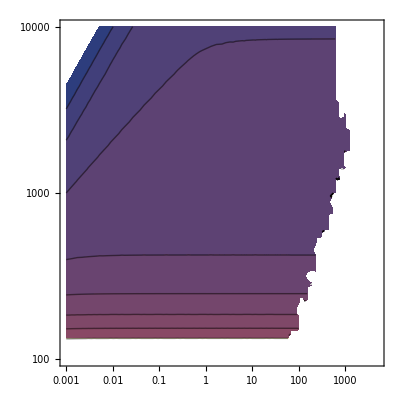

```mathematica
ContourPlot[Log10[funclifetimeτ[mchi,mphi]],{mchi,0.001,5000},{mphi,100,10000},ScalingFunctions->{"Log","Log"}]
```

The eta and L range of each detector component

```mathematica
listdetectorpart={"Vertex Detector","Inner Tracker","Outer Tracker","ECAL","HCAL","Solenoid","Muon Detector","Outside Detector"};
Do[barreleta[listdetectorpart[[i]]]={2.53,1.05,0.76,1.08,0.62,0.85,0.61,0.61}[[i]],{i,1,Length[listdetectorpart]}]
Do[barrelLrange[listdetectorpart[[i]]]=10^-2{{3,10.4},{12.7,55.4},{81.9,148.6},{150.0,170.2},{174,333},{348.3,429},{446.1,645},{645,10^10}}[[i]],{i,1,Length[listdetectorpart]}]
```

```mathematica
evententry["LLP_L",1000,"_VBF"][[-1]]
```

{{fourvec,{1946.63,509.474,-1590.41,-20.2542}},{beta,0.857966},{η,-0.0121278},{gamma,1.94663},{L/τ_ϕ,5.01007×10^8}}

## Calculating the event count in each detector region

```mathematica
Do[
Print["****************************"<>"Detector Part: "<>detectorpart<>"****************************"];
fingriddataL[detectorpart]={};
Do[
(*Print["================"<>"Label: "<>ToString[mphi]<>"================"];*)
totcounthelper=0;
Do[


(*Finds the L= L/Subscript[τ, ϕ] x Subscript[τ, ϕ] distance for events in a range of eta.*)
eventsLLPL["L",mchi,mphi,label][detectorpart]=funclifetimeτ[mchi,mphi]#[[-1,2]]&/@(Select[evententry["LLP_L",mphi,label],Abs[#[[3,2]]]<=barreleta[detectorpart]&]);
(*counts those events in the right L range and normalizes to the total number of events to determine what fraction of events pass the eta cut and in the right L range*)
efficientyLLP["L",mchi,mphi,label][detectorpart]=Count[eventsLLPL["L",mchi,mphi,label][detectorpart],u_/;barrelLrange[detectorpart][[1]]<=u<=barrelLrange[detectorpart][[2]]]/Length[evententry["LLP_L",mphi,label]];

counterLLP["L",mchi,mphi,label][detectorpart]=2 (*2 'cause ostensibly we have 2 ϕs per event*)10^7 xsec["LLP_L_mphi_"<>ToString[mphi]<>".0"<>label]efficientyLLP["L",mchi,mphi,label][detectorpart] {funcBRχl[mchi,mphi],funcBRϕ0μν[mchi,mphi]}(*MULTIPLY BY THE BR TO THE CHANNEL UNDER STUDY*);

(*add up the contribution of each channel*)
totcounthelper+=counterLLP["L",mchi,mphi,label][detectorpart];

(*The first entry in the 3rd place of counterLLP is the number for the χl, the ϕ0μν channel (electron not used)*)

,{label,{"_switch_0_0","_switch_0_1","_switch_1_1","_VBF"}}];



AppendTo[fingriddataL[detectorpart],{mchi,mphi,funclifetimeτ[mchi,mphi],totcounthelper}];

,{mchi,(*{0.01}*)tablemχ(*[[{1,10,-10,-1}]]*)},{mphi,(*{600}*)allmasses(*[[{1,10,-10,-1}]]*)}];



Export["../../../flavorDM2_lhe/saved_data_LLP/"<>"LLP_L_moneyplot_"<>detectorpart<>".dat",fingriddataL[detectorpart]];

,{detectorpart,listdetectorpart}]
```

****************************Detector Part: Vertex Detector****************************

Part::partd: Part specification LLP_L⟦3,2⟧ is longer than depth of object.

Part::partd: Part specification 125⟦3,2⟧ is longer than depth of object.

Part::partd: Part specification _switch_0_0⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

****************************Detector Part: Inner Tracker****************************

****************************Detector Part: Outer Tracker****************************

****************************Detector Part: ECAL****************************

****************************Detector Part: HCAL****************************

****************************Detector Part: Solenoid****************************

```mathematica
fingriddataL["ECAL"]
```

{{0.01,600,5.33859×10^-10,{0.,0.}}}

```mathematica
fingriddataL[#]&/@listdetectorpart
```

{{{0.01,600,5.33859×10^-10,{0.428718,64.8199}}},{{0.01,600,5.33859×10^-10,{0.420863,63.6323}}},{{0.01,600,5.33859×10^-10,{0.172414,26.0681}}},{{0.01,600,5.33859×10^-10,{0.,0.}}},{{0.01,600,5.33859×10^-10,{0.,0.}}},{{0.01,600,5.33859×10^-10,{0.,0.}}},{{0.01,600,5.33859×10^-10,{0.,0.}}},{{0.01,600,5.33859×10^-10,{0.,0.}}}}

```mathematica
efficientyLLP["L",tablemχ[[-1]],allmasses[[-1]],label]["ECAL"]
```

efficientyLLP[L,10000.,4800,LLP_L_mphi_4800.0_VBF][ECAL]

```mathematica
tablemχ[[{1,10,-10,-1}]]
allmasses[[{1,10,-10,-1}]]
```

{0.00001,0.0000657933,1519.91,10000.}

{100,600,3000,4800}

```mathematica
tstmχ=tablemχ[[1]]
tstmϕ=allmasses[[-1]]
```

0.00001

4800

```mathematica
efficientyLLP["L",tstmχ,tstmϕ,"_switch_0_0"]["ECAL"]
```

0

```mathematica
tablemχ[[1]]
```

0.00001

4800

```mathematica
counterLLP["L",tablemχ[[-10]],allmasses[[-1]],"_switch_0_0"][#]&/@listdetectorpart
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
eventsLLPL["L",400,1000,"_switch_0_0"]
```

## Reading LHE: Scaling by BRs should be made too: to only final state muons for visible and both mu and e for invisible

# PROMPT e Model

## Generating all lhe file names and reading xsections

```mathematica
(*allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union*)
allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union
masslist=allmasses;
ariamasslist=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union
```

{100,150,200,250,300,350,400,450,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

{100,125,150,175,200,225,250,275,300,325,350,400,450,500,550,600,650,700,750,800,900,1000,1100,1200,1300,1400,1500,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

```mathematica
ariamasslist//Length
```

44

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[cLfunc,cRfunc]
cstable=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em4.csv","CSV"]];
cfunc["L"]=Interpolation[#[[{1,2}]]&/@cstable]
cfunc["R"]=Interpolation[#[[{1,3}]]&/@cstable]
(*cstable8=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em8.csv","CSV"]];
cLfunc8=Interpolation[#[[{1,2}]]&/@cstable8]
cRfunc8=Interpolation[#[[{1,3}]]&/@cstable8]*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Show[
LogLinearPlot[cfunc["L"][m],{m,100,10000}],
LogLinearPlot[cfunc["R"][m],{m,100,10000},PlotStyle->Red]
]//frametrick
(*Show[
LogLinearPlot[cLfunc8[m],{m,100,10000}],
LogLinearPlot[cRfunc8[m],{m,100,10000},PlotStyle->Red]
]//frametrick*)
```

-Graphics-

μμ initial preparing for lhe imports:

```mathematica
Mod[1,44]
```

1

```mathematica
Clear[guide]
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["L"]=Import["../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_L/xsec.txt","Table"];
guide["R"]=Import["../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_R/xsec.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
Do[
helpguide={guide[LRRL][[1]]};
appendstr={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
Clear[helper];
Do[
helper[ring]=Table[ReplacePart[guide[LRRL][[Length[ariamasslist]ring +ii+1]],2->"mphi_"<>ToString[ariamasslist[[ii]]]<>".0"<>appendstr[[ring+1]]],{ii,1,Length[ariamasslist]}];
,{ring,{0,1,2,3}}];
guide[LRRL]=Join[helpguide,helper[0],helper[1],helper[2],helper[3]];
,{LRRL,{"L","R"}}]
```

```mathematica
guide["R"][[2]]
guide["L"][[77]]
```

{run_01,mphi_100.0_switch_0_0,0.0000924874,5.92438×10^-8,10000}

{run_76,mphi_2400.0_switch_0_1,0.0000528584,2.17912×10^-7,10000}

```mathematica
noPDFxsec["L"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["L"][[2;;46]]
noPDFxsec["R"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["R"][[2;;46]]
```

{{100.,0.000371314},{125.,0.000371335},{150.,0.000370663},{175.,0.000370644},{200.,0.000370734},{225.,0.000370412},{250.,0.000370201},{275.,0.000369892},{300.,0.000369516},{325.,0.000369361},{350.,0.000368774},{400.,0.00036815},{450.,0.000367643},{500.,0.00036651},{550.,0.000365514},{600.,0.000363936},{650.,0.000362492},{700.,0.000361114},{750.,0.00035947},{800.,0.000357556},{900.,0.00035397},{1000.,0.000349104},{1100.,0.000344699},{1200.,0.000339145},{1300.,0.000333474},{1400.,0.000327535},{1500.,0.00032073},{1600.,0.000313942},{1800.,0.000299455},{2000.,0.000283165},{2200.,0.000265996},{2400.,0.000247469},{2600.,0.000228112},{2800.,0.000207708},{3000.,0.000186505},{3200.,0.000164817},{3400.,0.000142595},{3600.,0.000120824},{3800.,0.0000989452},{4000.,0.0000776399},{4200.,0.0000572958},{4400.,0.0000383305},{4600.,0.000021417},{4800.,7.79236×10^-6},{100.,0.0000671951}}

{{100.,0.0000924874},{125.,0.0000925419},{150.,0.0000924099},{175.,0.0000922951},{200.,0.0000924057},{225.,0.0000922753},{250.,0.0000923117},{275.,0.000092106},{300.,0.0000921194},{325.,0.0000920193},{350.,0.0000919074},{400.,0.0000917401},{450.,0.0000916372},{500.,0.0000913443},{550.,0.000091104},{600.,0.0000907917},{650.,0.0000903852},{700.,0.0000900241},{750.,0.0000895953},{800.,0.0000891118},{900.,0.0000881877},{1000.,0.0000870283},{1100.,0.0000859146},{1200.,0.0000845543},{1300.,0.0000831303},{1400.,0.0000816018},{1500.,0.0000799761},{1600.,0.0000782299},{1800.,0.0000746861},{2000.,0.0000706176},{2200.,0.0000662866},{2400.,0.0000617072},{2600.,0.0000568556},{2800.,0.0000517641},{3000.,0.0000464681},{3200.,0.0000410705},{3400.,0.0000355684},{3600.,0.0000301254},{3800.,0.0000246596},{4000.,0.0000193501},{4200.,0.0000142729},{4400.,9.55431×10^-6},{4600.,5.33959×10^-6},{4800.,1.94251×10^-6},{100.,0.0000167609}}

```mathematica
Clear[coeff]
coeff["_switch_0_0"]["L"][m_]:=  cfunc["L"][m] cfunc["R"][m];
coeff["_switch_0_0"]["R"][m_]:=  cfunc["L"][m] cfunc["R"][m];
(*coeff["_switch_0_1"]["L"][m_]:=  cfunc["L"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];*)
coeff["_switch_0_1"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_1"]["L"][m_]:=1;
coeff["_switch_1_1"]["R"][m_]:=1;
(*coeff["_VBF"]=1;*)
```

```mathematica
guide["R"][[{26,71,116,161}]]
```

{{run_25,mphi_1300.0_switch_0_0,0.0000831303,6.58969×10^-8,10000},{run_70,mphi_1400.0_switch_0_1,0.0000169704,3.16078×10^-8,10000},{run_115,mphi_1500.0_switch_1_0,0.0000165729,4.71478×10^-8,10000},{run_160,mphi_1600.0_switch_1_1,3.28921×10^-6,8.86116×10^-9,10000}}

```mathematica
Clear[listinputs]
listinputs["L"]={};
listinputs["R"]={};
Do[
Do[
Do[
tst=Select[guide[LRRL],#[[2]]=="mphi_"<>ToString[masses]<>".0"<>labelappend&];
tstdirectory=tst[[1,1]];
tstlabel="e_"<>tst[[1,2]];
(*xsec[tstlabel]=coeff[labelappend]tst[[1,3]];*)
xsec[tstlabel]=coeff[labelappend][LRRL][masses]tst[[1,3]];
AppendTo[listinputs[LRRL],{"../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_"<>LRRL<>"/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"}}]

,{masses,allmasses}]

,{LRRL,{"L","R"}}]
listinputs["L"];
listinputs["R"];
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

```mathematica
listinputs["R"][[4]]
```

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_R/Events/run_133/unweighted_events.lhe,e_mphi_100.0_switch_1_1,{1,2},3.06614×10^-6,{True,{1,2}},{True,{1,2}}}

```mathematica
iii=0;
listinputs["R"][[57+iii]]
listinputs["R"][[61+iii]]

coeff["_switch_0_0"]["L"][1300]
coeff["_switch_0_1"]["L"][1300]
coeff["_switch_1_0"]["L"][1300]

listinputs["L"][[57+iii]]
listinputs["L"][[61+iii]]
```

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_R/Events/run_24/unweighted_events.lhe,e_mphi_1200.0_switch_0_0,{1,2},8.07925×10^-6,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_R/Events/run_26/unweighted_events.lhe,e_mphi_1400.0_switch_0_0,{1,2},7.62226×10^-6,{True,{1,2}},{True,{1,2}}}

0.0944381

0.302948

0.302948

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_L/Events/run_24/unweighted_events.lhe,e_mphi_1200.0_switch_0_0,{1,2},0.0000324056,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_L/Events/run_26/unweighted_events.lhe,e_mphi_1400.0_switch_0_0,{1,2},0.0000305944,{True,{1,2}},{True,{1,2}}}

```mathematica
(*dynamic 10^-4*)
Clear[xsecall4dyn,massxsecall4dyn]
Do[
xsecall4dyn[LRRL]=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs[LRRL],4];
massxsecall4dyn[LRRL]=Partition[Riffle[allmasses,xsecall4dyn[LRRL]],2]
,{LRRL,{"L","R"}}]
(*10^-4*)
(*xsecall4=#[[1]]+#[[2]]+#[[3]]&/@Partition[#[[4]]&/@listinputs,3]
massxsecall4=Partition[Riffle[allmasses,xsecall4],2]*)
(*10^-8*)
(*xsecall8=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs,4]
massxsecall8=Partition[Riffle[allmasses,xsecall8],2]*)
```

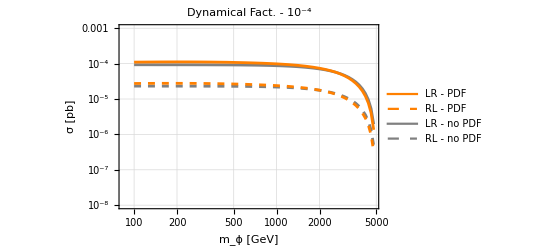

```mathematica
Legended[Show[
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["L"][[1;;-2]],Joined->True,PlotStyle->Gray,PlotRange->{10^-3,10^-8},FrameLabel->{"m_ϕ [GeV]","σ [pb]"},PlotLabel->"Dynamical Fact. - 10^-4"],
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["R"][[1;;-2]],Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[massxsecall4dyn["L"],Joined->True,PlotStyle->Orange],
ListLogLogPlot[massxsecall4dyn["R"],Joined->True,PlotStyle->{Orange,Dashed}]

],Placed[LineLegend[{Orange,{Dashed,Orange},Gray,{Dashed,Gray}},{"LR - PDF","RL - PDF","LR - no PDF","RL - no PDF"}],{0.2,0.25}]]//frametrick
```

VBF initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["VBF"]=Import["../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/xsec.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
helpguide={guide["VBF"][[1]]};
appendstr={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
Clear[helper];

helper[0]=Table[ReplacePart[guide["VBF"][[ii+1]],2->"mphi_"<>ToString[ariamasslist[[ii]]]<>".0"],{ii,1,Length[ariamasslist]}];

guide["VBF"]=Join[helpguide,helper[0]];
```

```mathematica
guide["VBF"][[28]]
```

{run_27,mphi_1500.0,4.47315×10^-6,9.89231×10^-9,10000}

```mathematica
guide["VBF"]
```

{{#,run_name,tag,cross,error,Nb_event,cross_after_matching,nb_event_after,matching},{run_01,mphi_100.0,0.00027643,5.56375×10^-7,10000},{run_02,mphi_125.0,0.000263445,0.0000107751,10000},{run_03,mphi_150.0,0.000250576,4.94178×10^-7,10000},{run_04,mphi_175.0,0.00023666,4.8374×10^-7,10000},{run_05,mphi_200.0,0.000224393,4.78775×10^-7,10000},{run_06,mphi_225.0,0.000210899,5.05255×10^-7,10000},{run_07,mphi_250.0,0.000199595,4.10519×10^-7,10000},{run_08,mphi_275.0,0.000187643,5.48825×10^-7,10000},{run_09,mphi_300.0,0.000177754,5.03161×10^-7,10000},{run_10,mphi_325.0,0.00016802,3.90738×10^-7,10000},{run_11,mphi_350.0,0.00016005,3.63551×10^-7,10000},{run_12,mphi_400.0,0.000148096,3.60466×10^-7,10000},{run_13,mphi_450.0,0.000137585,4.15774×10^-7,10000},{run_14,mphi_500.0,0.000122554,3.47356×10^-7,10000},{run_15,mphi_550.0,0.0000953407,2.28796×10^-7,10000},{run_16,mphi_600.0,0.0000755081,1.84324×10^-7,10000},{run_17,mphi_650.0,0.0000607403,1.49181×10^-7,10000},{run_18,mphi_700.0,0.0000494414,1.43867×10^-7,10000},{run_19,mphi_750.0,0.0000406059,1.12941×10^-7,10000},{run_20,mphi_800.0,0.0000338515,1.10366×10^-7,10000},{run_21,mphi_900.0,0.0000238015,5.61712×10^-8,10000},{run_22,mphi_1000.0,0.0000172729,0.0000164941,10000},{run_23,mphi_1100.0,0.0000127826,2.9764×10^-8,10000},{run_24,mphi_1200.0,9.66977×10^-6,2.88198×10^-7,10000},{run_25,mphi_1300.0,7.39351×10^-6,1.81198×10^-8,10000},{run_26,mphi_1400.0,5.72469×10^-6,1.29345×10^-8,10000},{run_27,mphi_1500.0,4.47315×10^-6,9.89231×10^-9,10000},{run_28,mphi_1600.0,3.53976×10^-6,8.17935×10^-9,10000},{run_29,mphi_1800.0,2.24523×10^-6,4.09682×10^-9,10000},{run_30,mphi_2000.0,1.46161×10^-6,2.85628×10^-9,10000},{run_31,mphi_2200.0,9.64594×10^-7,2.1729×10^-6,10000},{run_32,mphi_2400.0,6.4385×10^-7,1.04179×10^-9,10000},{run_33,mphi_2600.0,4.31845×10^-7,1.23304×10^-9,10000},{run_34,mphi_2800.0,2.90497×10^-7,4.37919×10^-10,10000},{run_35,mphi_3000.0,1.93939×10^-7,3.0623×10^-10,10000},{run_36,mphi_3200.0,1.28965×10^-7,2.01039×10^-10,10000},{run_37,mphi_3400.0,8.39599×10^-8,1.06214×10^-10,10000},{run_38,mphi_3600.0,5.33387×10^-8,2.16123×10^-10,10000},{run_39,mphi_3800.0,3.26502×10^-8,4.381×10^-11,10000},{run_40,mphi_4000.0,1.88594×10^-8,2.38571×10^-11,10000},{run_41,mphi_4200.0,9.94823×10^-9,1.10381×10^-11,10000},{run_42,mphi_4400.0,4.51536×10^-9,4.10842×10^-12,10000},{run_43,mphi_4600.0,1.5425×10^-9,2.15045×10^-12,10000},{run_44,mphi_4800.0,2.59379×10^-10,4.16408×10^-13,10000}}

```mathematica
listinputs["VBF"]={};
Do[
tst=Select[guide["VBF"],#[[2]]=="mphi_"<>ToString[masses]<>".0"&];
tstdirectory=tst[[1,1]];
tstlabel="e_"<>tst[[1,2]]<>"_VBF";
xsec[tstlabel]=tst[[1,3]];
AppendTo[listinputs["VBF"],{"../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs["VBF"]
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

{{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_01/unweighted_events.lhe,e_mphi_100.0_VBF,{1,2},0.00027643,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_03/unweighted_events.lhe,e_mphi_150.0_VBF,{1,2},0.000250576,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_05/unweighted_events.lhe,e_mphi_200.0_VBF,{1,2},0.000224393,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_07/unweighted_events.lhe,e_mphi_250.0_VBF,{1,2},0.000199595,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_09/unweighted_events.lhe,e_mphi_300.0_VBF,{1,2},0.000177754,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_11/unweighted_events.lhe,e_mphi_350.0_VBF,{1,2},0.00016005,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_12/unweighted_events.lhe,e_mphi_400.0_VBF,{1,2},0.000148096,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_13/unweighted_events.lhe,e_mphi_450.0_VBF,{1,2},0.000137585,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_14/unweighted_events.lhe,e_mphi_500.0_VBF,{1,2},0.000122554,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_16/unweighted_events.lhe,e_mphi_600.0_VBF,{1,2},0.0000755081,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_18/unweighted_events.lhe,e_mphi_700.0_VBF,{1,2},0.0000494414,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_20/unweighted_events.lhe,e_mphi_800.0_VBF,{1,2},0.0000338515,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_21/unweighted_events.lhe,e_mphi_900.0_VBF,{1,2},0.0000238015,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_22/unweighted_events.lhe,e_mphi_1000.0_VBF,{1,2},0.0000172729,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_24/unweighted_events.lhe,e_mphi_1200.0_VBF,{1,2},9.66977×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_26/unweighted_events.lhe,e_mphi_1400.0_VBF,{1,2},5.72469×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_28/unweighted_events.lhe,e_mphi_1600.0_VBF,{1,2},3.53976×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_29/unweighted_events.lhe,e_mphi_1800.0_VBF,{1,2},2.24523×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_30/unweighted_events.lhe,e_mphi_2000.0_VBF,{1,2},1.46161×10^-6,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_31/unweighted_events.lhe,e_mphi_2200.0_VBF,{1,2},9.64594×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_32/unweighted_events.lhe,e_mphi_2400.0_VBF,{1,2},6.4385×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_33/unweighted_events.lhe,e_mphi_2600.0_VBF,{1,2},4.31845×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_34/unweighted_events.lhe,e_mphi_2800.0_VBF,{1,2},2.90497×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_35/unweighted_events.lhe,e_mphi_3000.0_VBF,{1,2},1.93939×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_36/unweighted_events.lhe,e_mphi_3200.0_VBF,{1,2},1.28965×10^-7,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_37/unweighted_events.lhe,e_mphi_3400.0_VBF,{1,2},8.39599×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_38/unweighted_events.lhe,e_mphi_3600.0_VBF,{1,2},5.33387×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_39/unweighted_events.lhe,e_mphi_3800.0_VBF,{1,2},3.26502×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_40/unweighted_events.lhe,e_mphi_4000.0_VBF,{1,2},1.88594×10^-8,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_41/unweighted_events.lhe,e_mphi_4200.0_VBF,{1,2},9.94823×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_42/unweighted_events.lhe,e_mphi_4400.0_VBF,{1,2},4.51536×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_43/unweighted_events.lhe,e_mphi_4600.0_VBF,{1,2},1.5425×10^-9,{True,{1,2}},{True,{1,2}}},{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_44/unweighted_events.lhe,e_mphi_4800.0_VBF,{1,2},2.59379×10^-10,{True,{1,2}},{True,{1,2}}}}

## Reading lhe files from the names defined above - and calculating all observables. Takes a while. SKIP NOW: already saved data

```mathematica
listinputs["R"][[1;;1]]
```

{{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_R/Events/run_01/unweighted_events.lhe,e_mphi_100.0_switch_0_0,{1,2},0.0000122211,{True,{1,2}},{True,{1,2}}}}

Reading LHE files and calculating everything - MT2 included. 
Works for both VBF or μμ: just run different blocks in the section above.
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
listinputs["L"][[3]]
listinputs["VBF"][[3]]
```

{../../../flavorDM2_lhe/ellR_dynamic/mumu_to_llchichi_L/Events/run_89/unweighted_events.lhe,e_mphi_100.0_switch_1_0,{1,2},0.000024519,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/ellR_dynamic/VV_to_llchichi/Events/run_05/unweighted_events.lhe,e_mphi_200.0_VBF,{1,2},0.000224393,{True,{1,2}},{True,{1,2}}}

```mathematica
(*(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[LRRL][[ii,1]];
{finindices[label],xsec[label],mjjdata[label],MT2data[label]}=listinputs[LRRL][[ii,{3,4,5,6}]];

importmodule[filename[label],label,finindices[label]];

If[mjjdata[label][[1]],Print["Calculating mjj"];mjjlist[label]=mjjlistcalc[label,mjjdata[label][[2]]]];
If[MT2data[label][[1]],Print["Calculating MT2"];MT2list[label]=MT2listcalculator[label,MT2data[label][[2]]]];
Print["=============== Done with label: "<>label<>"==============="];


evententry[label]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

Export["../../../flavorDM2_lhe/saved_data_e/"<>label<>".dat",evententry[label]];

Print["=============== Event Entry Exported: "<>label<>"==============="];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]*)
```

Bkg lhe import:
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
(*
(**)
SetDirectory[NotebookDirectory[]];
(*importmodule["../../../flavorDM2_lhe/mumu_to_llvv/Events/run_02/unweighted_events.lhe","bkg_L_ll",{1,2}];*)
importmodule["../../../flavorDM2_lhe/mumu_to_llvv/Events/Events/run_01/unweighted_events.lhe","bkg_L_ll",{1,2}];
mjjlist["bkg_L_ll"]=mjjlistcalc["bkg_L_ll",{1,2}];
MT2list["bkg_L_ll"]=MT2listcalculator["bkg_L_ll",{1,2}];*)
```

```mathematica
(*evententry["L","bkg_L_ll"]=Table[{{"η",etalist["bkg_L_ll"][[ii]]},{"pT",pTlist["bkg_L_ll"][[ii]]},{"pTvec",pTveclist["bkg_L_ll"][[ii]]},{"fourvec",fourvecslist["bkg_L_ll"][[ii]]},{"ET",ETlist["bkg_L_ll"][[ii]]},{"beta",betalist["bkg_L_ll"][[ii]]},{"gamma",gammalist["bkg_L_ll"][[ii]]},{"MT2",MT2list["bkg_L_ll"][[ii]]},{"mjj",mjjlist["bkg_L_ll"][[ii]]}},{ii,1,Length[etalist["bkg_L_ll"]]}];

Export["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_ll"<>".dat",evententry["L","bkg_L_ll"]];*)
```

### MT2 comparison to aria

```mathematica
pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;
```

```mathematica
(*pouyamt2=MT2list[label];*)
pouyamt2new=MT2list[label];
```

```mathematica
Histogram[pouyamt2new/ariamt2,{0.1},PlotRange->{{0.5,2.5},{1,10^4}},FrameLabel->{"MT2_pouya/MT2_aria"}]//frametrick
```

-Graphics-

-Graphics-

```mathematica
Histogram[pouyamt2,{25},FrameLabel->{"MT2_pouya"}]//frametrick
Histogram[pouyamt2new,{25},FrameLabel->{"MT2_pouya"}]//frametrick
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[evententry["L",500,"_switch_0_0"],#[[-2,2]]>=500&]//Length
```

398

```mathematica
(*pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;*)
```

```mathematica
pouyamt2[[1;;22]]
ariamt2[[1;;22]]
```

{232.011,207.216,167.936,96.7128,201.31,163.765,444.962,128.659,87.4183,489.129,4.51487,143.431,97.9494,393.805,83.9932,136.572,21.8336,368.398,95.4135,121.853,53.2748,112.125}

{231.972,201.592,101.669,96.334,196.927,155.84,430.136,93.5088,87.328,286.936,2.98635,143.431,97.919,393.804,78.2696,136.435,20.8355,367.193,93.4874,94.2818,45.1187,88.7516}

```mathematica
Histogram[pouyamt2/ariamt2]
```

-Graphics-

## ***Now it’s done above with the importmodule code. SKIP*** Unifying all the data for an event in the “evententry” variable - Exports data to the saved_data folder The xsection is not saved and will be read from above

```mathematica
(*(*Clear[evententry]*)
SetDirectory[NotebookDirectory[]];
Do[
Print["============= m_ϕ = "<>ToString[mphi]<>"============"];
Do[
label="L_mphi_"<>ToString[mphi]<>".0"<>labelappend;
(*Print[label];*)
evententry["L",mphi,labelappend]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

(*Print[ToString[evententry["L",mphi,labelappend][[1,-1]]]];*)

Export["../../../flavorDM2_lhe/saved_data/"<>label<>".dat",evententry["L",mphi,labelappend]];

,{labelappend,{(*"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1",*)"_VBF"}}]
,{mphi,masslist}]*)
```

```mathematica
(*
evententry["L","bkg_L"]=Table[{{"η",etalist["bkg_L"][[ii]]},{"pT",pTlist["bkg_L"][[ii]]},{"pTvec",pTveclist["bkg_L"][[ii]]},{"fourvec",fourvecslist["bkg_L"][[ii]]},{"ET",ETlist["bkg_L"][[ii]]},{"beta",betalist["bkg_L"][[ii]]},{"gamma",gammalist["bkg_L"][[ii]]},{"MT2",MT2list["bkg_L"][[ii]]},{"mjj",mjjlist["bkg_L"][[ii]]}},{ii,1,Length[etalist["bkg_L"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L"<>".dat",evententry["L","bkg_L"]];*)
```

```mathematica
(*
evententry["L","bkg_L_old"]=Table[{{"η",etalist["bkg_L_old"][[ii]]},{"pT",pTlist["bkg_L_old"][[ii]]},{"pTvec",pTveclist["bkg_L_old"][[ii]]},{"fourvec",fourvecslist["bkg_L_old"][[ii]]},{"ET",ETlist["bkg_L_old"][[ii]]},{"beta",betalist["bkg_L_old"][[ii]]},{"gamma",gammalist["bkg_L_old"][[ii]]},{"MT2",MT2list["bkg_L_old"][[ii]]},{"mjj",mjjlist["bkg_L_old"][[ii]]}},{ii,1,Length[etalist["bkg_L_old"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_old"<>".dat",evententry["L","bkg_L_old"]];*)
```

```mathematica
(*
evententry["L","bkg_L_cut200"]=Table[{{"η",etalist["bkg_L_cut200"][[ii]]},{"pT",pTlist["bkg_L_cut200"][[ii]]},{"pTvec",pTveclist["bkg_L_cut200"][[ii]]},{"fourvec",fourvecslist["bkg_L_cut200"][[ii]]},{"ET",ETlist["bkg_L_cut200"][[ii]]},{"beta",betalist["bkg_L_cut200"][[ii]]},{"gamma",gammalist["bkg_L_cut200"][[ii]]},{"MT2",MT2list["bkg_L_cut200"][[ii]]},{"mjj",mjjlist["bkg_L_cut200"][[ii]]}},{ii,1,Length[etalist["bkg_L_cut200"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_cut200"<>".dat",evententry["L","bkg_L_cut200"]];*)
```

```mathematica
(*Clear[evententry]*)
```

```mathematica
(*evententry["L","bkg_L_ll"]=Table[{{"η",etalist["bkg_L_ll"][[ii]]},{"pT",pTlist["bkg_L_ll"][[ii]]},{"pTvec",pTveclist["bkg_L_ll"][[ii]]},{"fourvec",fourvecslist["bkg_L_ll"][[ii]]},{"ET",ETlist["bkg_L_ll"][[ii]]},{"beta",betalist["bkg_L_ll"][[ii]]},{"gamma",gammalist["bkg_L_ll"][[ii]]},{"MT2",MT2list["bkg_L_ll"][[ii]]},{"mjj",mjjlist["bkg_L_ll"][[ii]]}},{ii,1,Length[etalist["bkg_L_ll"]]}];

Export["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_ll"<>".dat",evententry["L","bkg_L_ll"]];*)
```

## Importing the “evententry” data of each event ee,eμ,μe,μμ already included

```mathematica
SetDirectory[NotebookDirectory[]];
Do[
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
xsec[label]=listinputs[LRRL][[ii,4]];
,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]
```

```mathematica
Do[
Do[
(*label="L_mphi_"<>ToString[mphi]<>".0"<>labelappend<>"_"<>LRRL;*)
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL(*If[LRRL=="VBF",listinputs[LRRL][[ii,2]],listinputs[LRRL][[ii,2]]<>"_"<>LRRL]*);
evententry[label]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_e/"<>label<>".dat","TSV"]];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}];
Print["Label Done: "<>label];
,{LRRL,{"L","R","VBF"}}]
```

Label Done: e_mphi_4800.0_switch_1_1_L

Label Done: e_mphi_4800.0_switch_1_1_R

Label Done: e_mphi_4800.0_VBF_VBF

```mathematica
SetDirectory[NotebookDirectory[]];
(*evententry["L","bkg_L"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L"<>".dat","TSV"]];
evententry["L","bkg_L_old"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_old"<>".dat","TSV"]];*)
(*evententry["L","bkg_L_cut200"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_cut200"<>".dat","TSV"]];*)
(*evententry["e","bkg_e_ll"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_ll_old"<>".dat","TSV"]];*)
evententry["e","bkg_e_ll"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_ll"<>".dat","TSV"]];
```

```mathematica
(*xsec["bkg_L_old"]=0.1;
xsec["bkg_L"]=0.1;*)
(*xsec["bkg_L_cut200"]=0.010886;*)
xsec["bkg_e_ll"]=0.0168;
```

```mathematica
evententry["e","bkg_e_ll"][[1]]
evententry["e_mphi_500.0_VBF_VBF"][[1]]
```

{{η,{0.979583,-1.90888}},{pT,{1389.66,1402.95}},{pTvec,{{0,-1388.64,53.3065,0},{0,1383.9,-230.419,0}}},{fourvec,{{2111.46,-1388.64,53.3065,1589.68},{4835.8,1383.9,-230.419,-4627.81}}},{ET,{1389.66,1402.95}},{beta,{1.,1.}},{gamma,{358951.,0.-228816. ⅈ}},{MT2,176.757},{mjj,6245.21}}

{{η,{0.906541,-0.545113}},{pT,{81.9989,311.771}},{pTvec,{{0,-74.0099,-35.3039,0},{0,-302.334,-76.1289,0}}},{fourvec,{{118.065,-74.0099,-35.3039,84.9437},{359.251,-302.334,-76.1289,-178.493}}},{ET,{81.9989,311.771}},{beta,{1.,1.}},{gamma,{201337.,710015.}},{MT2,318.219},{mjj,255.003}}

{{η,{0.979583,-1.90888}},{pT,{1389.66,1402.95}},{pTvec,{{0,-1388.64,53.3065,0},{0,1383.9,-230.419,0}}},{fourvec,{{2111.46,-1388.64,53.3065,1589.68},{4835.8,1383.9,-230.419,-4627.81}}},{ET,{1389.66,1402.95}},{beta,{1.,1.}},{gamma,{358951.,0.-228816. ⅈ}},{MT2,176.757},{mjj,6245.21}}

{{η,{0.906541,-0.545113}},{pT,{81.9989,311.771}},{pTvec,{{0,-74.0099,-35.3039,0},{0,-302.334,-76.1289,0}}},{fourvec,{{118.065,-74.0099,-35.3039,84.9437},{359.251,-302.334,-76.1289,-178.493}}},{ET,{81.9989,311.771}},{beta,{1.,1.}},{gamma,{201337.,710015.}},{MT2,318.219},{mjj,255.003}}

## For a test mass, extracting an observables from all events to make hiastograms

{{η,{0.30146,-0.360538}},{pT,{3087.44,4322.67}},{pTvec,{{0,3083.94,146.887,0},{0,-4322.13,68.7921,0}}},{fourvec,{{3228.79,3083.94,146.887,944.899},{4606.68,-4322.13,68.7921,-1592.47}}},{ET,{3087.44,4322.67}},{beta,{1.,1.}},{gamma,{0.-356396. ⅈ,0.-1.28368×10^6 ⅈ}},{MT2,234.243},{mjj,7706.86}}

```mathematica
modellabel="e";
bkglabel="bkg_e_ll";
```

```mathematica
Clear[listlabels]
listlabels["L"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["R"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["VBF"]={"_VBF"};
```

```mathematica
(*Clear[dataxsecall]*)
Clear[histogramdata]
Do[

Do[
dataxsecall[modellabel,mphi,LRRL]={};
allhistogramdata["MT2"][modellabel,mphi,LRRL]={};
allhistogramdata["mjj"][modellabel,mphi,LRRL]={};
allhistogramdata["pT"][modellabel,mphi,LRRL]={};
allhistogramdata["pTll"][modellabel,mphi,LRRL]={};
allhistogramdata["eta"][modellabel,mphi,LRRL]={};
allhistogramdata["cosθ"][modellabel,mphi,LRRL]={};

Do[
fulllabel=modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label,modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[dataxsecall[modellabel,mphi,LRRL],xsec[fulllabel]];
histogramdata["MT2"][modellabel,mphi,label,LRRL]=#[[-2,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["MT2"][modellabel,mphi,LRRL],histogramdata["MT2"][modellabel,mphi,label,LRRL]];
histogramdata["mjj"][modellabel,mphi,label,LRRL]=#[[-1,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["mjj"][modellabel,mphi,LRRL],histogramdata["mjj"][modellabel,mphi,label,LRRL]];
histogramdata["pT"][modellabel,mphi,label,LRRL]=#[[2,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pT"][modellabel,mphi,LRRL],histogramdata["pT"][modellabel,mphi,label,LRRL]];
histogramdata["pTll"][modellabel,mphi,label,LRRL]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pTll"][modellabel,mphi,LRRL],histogramdata["pTll"][modellabel,mphi,label,LRRL]];
histogramdata["eta"][modellabel,mphi,label,LRRL]=#[[1,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["eta"][modellabel,mphi,LRRL],histogramdata["eta"][modellabel,mphi,label,LRRL]];
histogramdata["cosθ"][modellabel,mphi,label,LRRL]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[fulllabel];
AppendTo[allhistogramdata["cosθ"][modellabel,mphi,LRRL],histogramdata["cosθ"][modellabel,mphi,label,LRRL]];

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];

dataxsecall[modellabel,mphi]={Riffle[dataxsecall[modellabel,mphi,"L"],dataxsecall[modellabel,mphi,"R"]]};
AppendTo[dataxsecall[modellabel,mphi],dataxsecall[modellabel,mphi,"VBF"]];



order={9,7,8,3,4,5,6,1,2}; (*ORDER FOR PRESENTATION IN THE HISTOGRAM*)

dataxsecall[modellabel,mphi]=Flatten[dataxsecall[modellabel,mphi],1][[order]];
Do[
allhistogramdata[obs][modellabel,mphi]={Riffle[allhistogramdata[obs][modellabel,mphi,"L"],allhistogramdata[obs][modellabel,mphi,"R"]]};
AppendTo[allhistogramdata[obs][modellabel,mphi],allhistogramdata[obs][modellabel,mphi,"VBF"]];
allhistogramdata[obs][modellabel,mphi]=Flatten[allhistogramdata[obs][modellabel,mphi],1][[order]];
,{obs,{"MT2","mjj","pT","pTll","eta","cosθ"}}]

,{mphi,masslist}]



(*BKG Data*)
Do[
histogramdata["MT2"][modellabel,bkglabel]=#[[-2,2]]&/@evententry[modellabel,bkglabel];
histogramdata["mjj"][modellabel,bkglabel]=#[[-1,2]]&/@evententry[modellabel,bkglabel];
histogramdata["pT"][modellabel,bkglabel]=#[[2,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["pTll"][modellabel,bkglabel]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[modellabel,bkglabel];
histogramdata["eta"][modellabel,bkglabel]=#[[1,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["cosθ"][modellabel,bkglabel]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[modellabel,bkglabel];


,{bkglabel,{"bkg_e_ll"(*"bkg_L","bkg_L_old","bkg_L_cut200"*)}}
]
```

## Histograms 1D: USE PDF FUNCTION BUT IT INTRODUCES SOME RANDOM NORMALIZATION THAT SHOULD BE FIXED BY HAND TO AGREE WITH THE PROPER DISCRETE CALC. I STILL KEPT IN THE PLOT PART.

```mathematica
RGBColor
```

```mathematica
Darker[Green]
```

RGBColor[0, Rational[2, 3], 0]

```mathematica
List@@@ColorData[#]&/@{Darker[Green],Purple,Orange}
```

ColorData::notent: color is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: {0,2/3,0} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: color is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

{ColorData[{0,2/3,0}],ColorData[{0.5,0,0.5}],ColorData[{1,0.5,0}]}

ColorData::notent: color is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData[RGBColor[0, Rational[2, 3], 0]]

```mathematica
mphitst=2800;
bkglabel="bkg_e_ll";
modellabel="e";
```

```mathematica
tst=weightedmixmaker[allhistogramdata["eta"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["eta"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-2.4;maxx=2.4;stepx=0.2;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,PDF[helper,#]}&/@binsdata;
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

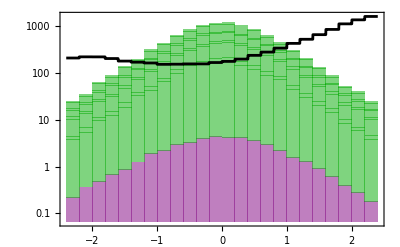

```mathematica
plt=Show[
Histogram[tst,{minx,maxx,stepx},ChartLayout->"Stacked",ChartStyle->{Purple,(*Orange*)Darker[Green],(*Orange*)Darker[Green],(*Blue*)Darker[Green],(*Blue*)Darker[Green],(*Purple*)Darker[Green],(*Purple*)Darker[Green],Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{MaTeX["\\eta_{\\mu^+}",FontSize->18],MaTeX["\\mathrm{Events}/"<>ToString[stepx],FontSize->18]},PlotLabel->MaTeX["m_\\phi = "<>ToString[mphitst]<>" \\mathrm{GeV}",FontSize->20],ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None(*,PlotRange->{{minx,maxx},{0.23,10^3}}*)]//frametricknogrid,


(*Histogram[bkgtst,{0.2},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

(*ListLinePlot[bkgtstss,InterpolationOrder->0,PlotStyle->Black,ScalingFunctions->"Log"],*)
Plot[2 10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},Full}]
]
```

```mathematica
Export[modellabel<>"_histogrameta_"<>ToString[mphitst]<>".pdf",plt]
```

e_histogrameta_2800.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["cosθ"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["cosθ"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-1;maxx=1;stepx=0.1;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.1 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdataeta["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataeta["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataeta["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

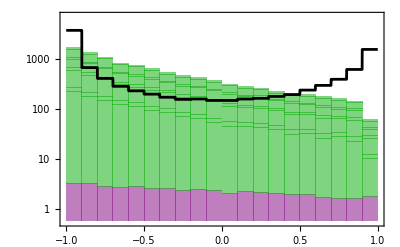

```mathematica
plt=Show[
Histogram[tst,{0.1},ChartLayout->"Stacked",ChartStyle->{Purple,Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{MaTeX["\\cos \\theta",FontSize->18],MaTeX["\\mathrm{Events}/"<>ToString[stepx],FontSize->18]},PlotLabel->MaTeX["m_\\phi = "<>ToString[mphitst]<>" \\mathrm{GeV}",FontSize->20],ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{(*43*)0.55,7000},PlotRangePadding->{Automatic,None}]//frametricknogrid,


(*Histogram[bkgtst,{0.1},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

```mathematica
Export[modellabel<>"_histogramcos_"<>ToString[mphitst]<>".pdf",plt]
```

e_histogramcos_2800.pdf

FOR BELOW, FOR 0.2 AND 2.8 TEV THE RANGE AND THE STEPSIZE AND THE NORMALIZATION FACTOR ADDED TO MAKE THE PDF FUNCTION WORK RIGHT ARE DIFFERENT. CHANGE FOR EACH

```mathematica
tst=weightedmixmaker[allhistogramdata["MT2"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["MT2"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=0;maxx=(*250*)(*800*)3000;stepx=(*10*)(*20*)50;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdataMT2["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataMT2["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataMT2["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

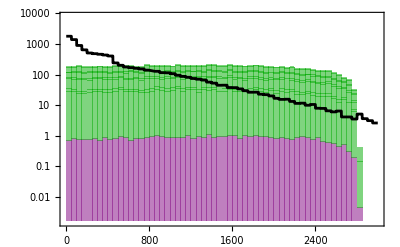

```mathematica
plt=Show[
Histogram[tst,{0,maxx,stepx},ChartLayout->"Stacked",ChartStyle->{Purple,Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{MaTeX["M_{T2}~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\mathrm{Events}/("<>ToString[stepx]<>"~\\mathrm{GeV})",FontSize->18]},PlotLabel->MaTeX["m_\\phi = "<>ToString[mphitst]<>" \\mathrm{GeV}",FontSize->20],ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{(*110 10^-4*)(*0.8 10^-2*)1.5 10^-3,0.8 10^4}(*,PlotRangePadding->{Automatic,None}*)]//frametricknogrid,

(*Histogram[bkgtst,{0,maxx,stepx},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,*)

Plot[ (*10^5*)(*0.2 10^6*)0.5 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]

]
```

```mathematica
Export[modellabel<>"_histogramMT2_"<>ToString[mphitst]<>".pdf",plt]
```

e_histogramMT2_2800.pdf

## New Cut Module and Reach Plots

```mathematica
gγ=-sw;gZL=1/(√(1-sw^2))(-1/2+sw^2);gZR=1/(√(1-sw^2))(sw^2);
```

```mathematica
(gγ^2+gZL^2)^2
(gγ^2+gZR^2)^2
(gγ^2+gZL gZR)^2
```

0.105414

0.0892225

0.0223056

```mathematica
alllabelslist
```

{L_mphi_4800.0_switch_0_0_L,L_mphi_4800.0_switch_0_1_L,L_mphi_4800.0_switch_1_0_L,L_mphi_4800.0_switch_1_1_L,L_mphi_4800.0_switch_0_0_R,L_mphi_4800.0_switch_0_1_R,L_mphi_4800.0_switch_1_0_R,L_mphi_4800.0_switch_1_1_R,L_mphi_4800.0_VBF}

```mathematica
evententry[fulllabel][[1]]
```

{{η,{-1.3335,-1.5179}},{pT,{626.356,284.377}},{pTvec,{{0,-215.88,-587.978,0},{0,123.396,256.21,0}}},{fourvec,{{1270.83,-215.88,-587.978,-1105.75},{679.915,123.396,256.21,-617.587}}},{ET,{626.356,284.377}},{beta,{1.,1.}},{gamma,{0.-102802. ⅈ,0.-546591. ⅈ}},{MT2,40.9056},{mjj,846.691}}

```mathematica
Cos[π/180#]&/@{60,90,120,130,140,150,160}//N
```

{0.5,0.,-0.5,-0.642788,-0.766044,-0.866025,-0.939693}

```mathematica
Clear[cutmodule]
cutmodule[modelLuQ_,mphi_,cutmjj_,cutpTll_,cutMT2_,etacut_,costhcut_,cuttotE_,cutMET_][flagPDF_,minbkg_]:=Module[{},

alllabelslist={};
Do[Do[
fulllabel=modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label,modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[alllabelslist,fulllabel];

signalevents[fulllabel]=Select[evententry[fulllabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[signalevents[modelLuQ,mphi,channindx]]]];*)

aftercutweight[fulllabel]=Length[signalevents[fulllabel]]/Length[evententry[fulllabel]];

(*since 2 μ in the final state*)
evencount[fulllabel]=aftercutweight[fulllabel] xsec[fulllabel] 10^7 If[flagPDF==True,1,1/(coeff["_switch_0_0"]["L"][mphi])](*to get the noPDF case*);
(*Luminosity at a 10 TeV MuC in pb^-1*)

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];


bkgevents[modelLuQ]=Select[evententry[modelLuQ,bkglabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[bkgevents[modelLuQ]]]];*)

aftercutweight[bkglabel]=Length[bkgevents[modelLuQ]]/Length[evententry[modelLuQ,bkglabel]];

(*since 2 μ in the final state*)
evencount[bkglabel]=Max[minbkg,aftercutweight[bkglabel] xsec[bkglabel] 10^7];
(*Luminosity at a 10 TeV MuC in pb^-1*)


{{"Signal Count",Tr[Table[evencount[channindx],{channindx,If[flagPDF==True,alllabelslist,alllabelslist[[{1,5}]]]}]]},{"Bkg Count",evencount[bkglabel]}}

]
```

```mathematica
mphitst=4000;
minbkgemodel=xsec["bkg_e_ll"] 10^7 10 10^-5;
cutmodule[modellabel,mphitst,{500,200000},{0,400000},{2000,100000},0.6,Cos[π/180 20],{1000,100000},{0,50000}][True,minbkgemodel][[{1,2},2]]
(%[[1]])/(√(%[[2]]))
```

{88.369,1162.56}

2.59175

{38.0034,36.96}

6.25111

{38.0034,36.96}

6.25111

Optimized for m=4.2 TeV: mjj > 300, pTll > 0, MT2> 2400, |eta|<0.4, θ >30, El > 1200

{40.8431,344.4}

2.20083

**Optimized for m=2.8 TeV: mjj > 300, pTll > 0, MT2> 800, |eta|<0.2, θ >130, El > 1800

{54.0871,36.96}

8.89667

**Optimized for m=0.2 TeV: mjj > 300, pTll > 0, MT2> 10, |eta|<0.5, θ >160, El > 500

{632.119,1078.56}

19.2476

```mathematica
Series[(1/(s-M2))^2,{s,0,10}]
```

1/M2^2+(2 s)/M2^3+(3 s^2)/M2^4+(4 s^3)/M2^5+(5 s^4)/M2^6+(6 s^5)/M2^7+(7 s^6)/M2^8+(8 s^7)/M2^9+(9 s^8)/M2^10+(10 s^9)/M2^11+(11 s^10)/M2^12+O[s]^11

```mathematica
1.655/8//N
```

0.206875

```mathematica
hbar
```

6.58212×10^-25

```mathematica
(0.01^3/((10^19)^2)hbar^-1)^-1
```

6.58212×10^19

### PDF vs noPDF

OLD SRs

```mathematica
nopdfeffectSR1old=Table[{mm,cutmodule[modellabel,mm,{1500,200000},{1300,400000},{3500,100000},2.4,1,{0,100000},{0,50000}][False,20][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
nopdfeffectSR2old=Table[{mm,cutmodule[modellabel,mm,{2600,200000},{750,400000},{200,100000},2.4,1,{0,100000},{0,50000}][False,20][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

```mathematica
pdfeffectSR1old=Table[{mm,cutmodule[modellabel,mm,{1500,200000},{1300,400000},{3500,100000},2.4,1,{0,100000},{0,50000}][True,20][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
pdfeffectSR2old=Table[{mm,cutmodule[modellabel,mm,{2600,200000},{750,400000},{200,100000},2.4,1,{0,100000},{0,50000}][True,20][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

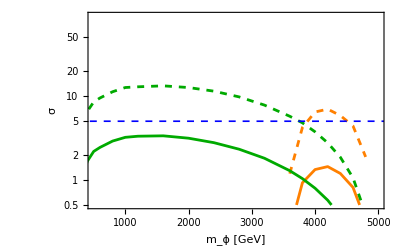

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@nopdfeffectSR1old,Joined->True,PlotRange->{{500,5000},{0.5,90}},PlotStyle->{{Orange,Dashed}},FrameLabel->{"m_ϕ [GeV]","σ"},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\sigma",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Significance}~ - ~\\mu~\\mathrm{PDF~Effect} ~ (e~\\mathrm{model})",FontSize->18]]//frametricknogrid,
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1old,Joined->True,PlotRange->{0.5,20},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametricknogrid,

ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@nopdfeffectSR2old,Joined->True,PlotRange->{0.5,20},PlotStyle->{{Darker[Green],Dashed}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametricknogrid,
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2old,Joined->True,PlotRange->{0.5,20},PlotStyle->{{Darker[Green]}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametricknogrid,

LogPlot[5,{x,0,10^4},PlotStyle->{Dashed,Thickness[0.003],Blue}],

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange,{Dashed,Darker[Green]},{Dashed,Orange}},{MaTeX["\\mathrm{SR}_1~-~\\mathrm{with~PDF}",FontSize->12],MaTeX["\\mathrm{SR}_2~-~\\mathrm{with~PDF}",FontSize->12],MaTeX["\\mathrm{SR}_1~-~\\mathrm{no~PDF}",FontSize->12],MaTeX["\\mathrm{SR}_2~-~\\mathrm{no~PDF}",FontSize->12]},LegendLayout->{"Column",2}],{0.5,0.85}]]
```

```mathematica
Export["sigdrop_old.pdf",plt]
```

sigdrop_old.pdf

New SRs

```mathematica
(*nopdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{10,100000},0.5,Cos[π/180 160],{500,100000},{0,50000}][False,minbkgemodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
nopdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{800,100000},0.2,Cos[π/180 130],{1800,100000},{0,50000}][False,minbkgemodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];*)
```

```mathematica
pdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{150,100000},0.3,Cos[π/180 160],{600,100000},{0,50000}][True,minbkgemodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
pdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{300,200000},{0,400000},{800,100000},0.2,Cos[π/180 130],{1800,100000},{0,50000}][True,minbkgemodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

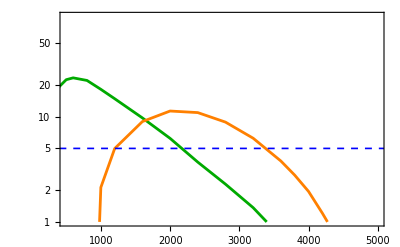

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1,Joined->True,PlotRange->{{500,5000},{1,90}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\sigma",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Significance} ~ (e~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,

LogPlot[5,{x,0,10^4},PlotStyle->{Dashed,Thickness[0.003],Blue}],

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^\\ell",FontSize->16],MaTeX["\\mathrm{SR}_2^\\ell",FontSize->16]}],{0.8,0.8}]]
```

```mathematica
Export["e_sig_reach.pdf",plt]
```

e_sig_reach.pdf

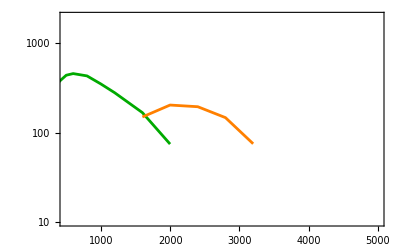

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR1,Joined->True,PlotRange->{{500,5000},{10,2000}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\mathrm{sys.}/\\mathrm{stat.}~[\\%]",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Tolerable~Systematics}~ (e~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR2,Joined->True,PlotStyle->{{Orange}}]//frametricknogrid,

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^\\ell",FontSize->16],MaTeX["\\mathrm{SR}_2^\\ell",FontSize->16]}],{0.8,0.8}]]
```

```mathematica
Export["tolerated_e.pdf",plt]
```

tolerated_e.pdf

### SRs reach

SR200

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={100,100000};
etacutSR=0.3;
coscutSR=Cos[π/180 160];
```

```mathematica
dataSR200=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{1.53745,60.24}},{200,{201.423,60.24}},{300,{285.573,60.24}},{400,{311.584,60.24}},{500,{314.538,60.24}},{600,{298.593,60.24}},{800,{256.573,60.24}},{1000,{213.613,60.24}},{1200,{171.939,60.24}},{1600,{109.053,60.24}},{2000,{67.2295,60.24}},{2400,{42.2668,60.24}},{2800,{25.1495,60.24}},{3200,{15.3297,60.24}},{3600,{8.23689,60.24}},{4000,{3.53732,60.24}},{4400,{1.28243,60.24}},{4800,{0.17394,60.24}}}

```mathematica
sysfraction200={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR200
```

{{100,0.},{200,509.312},{300,729.051},{400,796.652},{500,804.322},{600,762.9},{800,653.542},{1000,541.287},{1200,431.626},{1600,262.618},{2000,141.464},{2400,43.1557},{2800,0.},{3200,0.},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction200,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR200,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR2800

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={700,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 120];
```

```mathematica
dataSR2800=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40.16}},{200,{0.,40.16}},{300,{0.,40.16}},{400,{0.,40.16}},{500,{0.,40.16}},{600,{0.,40.16}},{800,{19.1563,40.16}},{1000,{66.8356,40.16}},{1200,{92.5872,40.16}},{1600,{115.406,40.16}},{2000,{107.497,40.16}},{2400,{88.9282,40.16}},{2800,{67.3912,40.16}},{3200,{45.3082,40.16}},{3600,{26.2088,40.16}},{4000,{14.3701,40.16}},{4400,{5.2646,40.16}},{4800,{0.744566,40.16}}}

```mathematica
sysfraction2800={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR2800
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,0.},{1000,185.72},{1200,274.559},{1600,350.222},{2000,324.185},{2400,262.235},{2800,187.71},{3200,102.208},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction2800,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR2800,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR3600

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={600,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 130];
```

```mathematica
dataSR3600=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40}},{200,{0.,40}},{300,{0.,40}},{400,{0.,40}},{500,{0.,40}},{600,{0.,40}},{800,{49.8266,40}},{1000,{92.3356,40}},{1200,{109.471,40}},{1600,{116.803,40}},{2000,{100.998,40}},{2400,{77.9031,40}},{2800,{55.8582,40}},{3200,{36.5984,40}},{3600,{20.8445,40}},{4000,{10.8762,40}},{4400,{3.78136,40}},{4800,{0.545746,40}}}

```mathematica
sysfraction3600={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR3600
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,121.766},{1000,274.333},{1200,331.421},{1600,355.57},{2000,303.323},{2400,225.142},{2800,145.607},{3200,58.2619},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction3600,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"}]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR3600,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

### Other

```mathematica
Do[

 Print[xsec["L_mphi_"<>ToString[mphitst]<>".0"<>channindx] ]

,{channindx,listlabels[[2;;4]]}]
```

2.62474×10^-7

1.67179×10^-6

2.60301×10^-6

Check SRs

```mathematica
mjjtst=990;
(*probably 2 i add above was already in her xsec. she found σ~0.2*)
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{3500,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{1800,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{200,100000}][[{1,2},2]]&/@{1300,750,200}
```

{{0.,0.},{0.,0.},{0.,0.}}

{{0.,2040.},{0.,2040.},{0.,2040.}}

{{7.04978,20300.},{9.96491,49510.},{12.041,66040.}}

{{0.,70.7547},{0.,70.7547},{0.,70.7547}}

{{0.,2031.67},{0.,2031.67},{0.,2031.67}}

{{7.04978,20306.6},{9.96491,49386.8},{12.041,66256.7}}

### Plots

```mathematica
tablescanmjjptMT2in[mphi_][mjjmax_,ptmax_,MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){mjjscan,ptscan,cutmodule["L",mphi,{mjjscan,mjjmax},{ptscan,ptmax},MT2range,0.2,Cos[π/180 150]][[{1,2},2]]},{mjjscan,0,2000,250},{ptscan,0,2000,250}],1]
tablescanetacosthMT2in[mphi_][MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){etascan,cosscan,cutmodule["L",mphi,{100,100000},{0,100000},MT2range,etascan,cosscan][[{1,2},2]]},{etascan,0.1,0.8,0.1},{cosscan,-0.9,-0.0,0.1}],1]
```

```mathematica
mphitst=3400;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{200,50000},{600,50000},{700,50000},{1000,50000}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sw^2
√(1-sw^2)
```

0.23

0.877496

```mathematica
mphitst=3400;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanmjjptMT2in[mphitst][80000,50000,mt2R],FrameLabel->{"pT_μ cut","m_μμ cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{200,50000},{600,50000},{700,50000},{1000,50000}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

no η or cosθ cuts: really not doing that well.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Cuts optimizing m=1TeV: mjj> 3000, pTll>500,MT2>200,|η|<0.5, cosθ < -0.8

{-Graphics-,-Graphics-}

## Histograms 2D

```mathematica
tst=Table[{RandomReal[{0,1}],RandomReal[{0,1}]},{i,1,1000}];
```

```mathematica
DensityHistogram[tst]
```

-Graphics-

```mathematica
tstw=Table[RandomReal[{4,10}],{i,1,1000}];
DensityHistogram[WeightedData[tst,tstw]]
```

-Graphics-

```mathematica
?weightedmixmaker
```

```mathematica
testmass=500;
tst=weightedmixmaker[allhistogram2DdataMT2mjj["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdataMT2mjj["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

```mathematica
(DensityHistogram[#,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","m_μμ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst 
DensityHistogram[bkgtst[[1]],PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","m_μμ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
tst=weightedmixmaker[allhistogram2DdataMT2pT["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdataMT2pT["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

```mathematica
(DensityHistogram[#,{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst
DensityHistogram[bkgtst[[1]],{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
tst=weightedmixmaker[allhistogram2DdatamjjpT["L",testmass],Table[xsec["L_mphi_"<>ToString[testmass]<>".0"<>label],{label,listlabels[[2;;-1]]}]]
bkgtst=weightedmixmaker[{histogram2DdatamjjpT["L","bkg_L"]},{xsec["bkg_L"]}]
```

{WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

```mathematica
(DensityHistogram[#,{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"m_μμ [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid)&/@tst
DensityHistogram[bkgtst[[1]],{10,10},PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"m_μμ [GeV]","p_T [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = "<>ToString[testmass]<>" GeV",ImageSize->350]//frametricknogrid
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

## Making the Tolerable Error Plots: After SRs identified

For each mass point: 
	Should first run the above module to get the total event count for the SR
	use the formula below to find the tolerable systematics as a fraction of statistics error √B. 
	Automatically returns a complex number if no discovery is possible somewhere in that SR.
	Repeat this for each mass point: the end result should be a list with masses of χ and ϕ, B and S (for sanity checks), and the tolerable x.
	Repeat this for each SR.

```mathematica
x/.Solve[S/(√((1+x^2)B))==5,x][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(-25 B+S^2))/(5 √B)

## 2D Histograms older

```mathematica
combodata[listlabels[[1]]]
```

```mathematica
combodata[listlabels[[2]]]
```

```mathematica
mt2=Table[RandomReal[{2,6}]{RandomReal[{0,1}],1},{i,1,10000}];
tstbkg=Table[{RandomReal[{2,3}],RandomReal[{1,2}]},{i,1,10000}];
```

```mathematica
mt2mjjH2D={#[[1]],#[[2]]}&/@combodata[listlabels[[2]]];
mt2mjjH2Dbkg={#[[1]],#[[2]]}&/@combodata[listlabels[[1]]];
mt2pTH2D={#[[1]],#[[3]]}&/@combodata[listlabels[[2]]];
mt2pTH2Dbkg={#[[1]],#[[3]]}&/@combodata[listlabels[[1]]];
mjjpTH2D={#[[2]],#[[3]]}&/@combodata[listlabels[[2]]];
mjjpTH2Dbkg={#[[2]],#[[3]]}&/@combodata[listlabels[[1]]];
```

```mathematica
DensityHistogram[mt2pTH2D,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","pT_μ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = 4000 GeV"]//frametricknogrid
DensityHistogram[mt2pTH2Dbkg,PlotRange->{{0,5000},{0,6000}},ColorFunction->"SunsetColors",FrameLabel->{"M_T2 [GeV]","pT_μ [GeV]"},AspectRatio->1/GoldenRatio,PlotLabel->"m_ϕ = 4000 GeV"]//frametricknogrid
```

-Graphics-

-Graphics-

```mathematica
xsec[listlabels[[2]]]
xsec["bkg_L"]
```

8.89269×10^-6

0.101078

# PROMPT u Model: THE XSECTIONS IN LHE FILES WERE OFF BY A FACTOR OF 9. SO MULTIPLY THEM BY THAT.

## Generating all lhe file names and reading xsections

```mathematica
(*allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union*)
allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union
masslist=allmasses;
ariamasslist=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union
```

{100,150,200,250,300,350,400,450,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

{100,125,150,175,200,225,250,275,300,325,350,400,450,500,550,600,650,700,750,800,900,1000,1100,1200,1300,1400,1500,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[cLfunc,cRfunc]
cstable=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em4.csv","CSV"]];
cfunc["L"]=Interpolation[#[[{1,2}]]&/@cstable]
cfunc["R"]=Interpolation[#[[{1,3}]]&/@cstable]
(*cstable8=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em8.csv","CSV"]];
cLfunc8=Interpolation[#[[{1,2}]]&/@cstable8]
cRfunc8=Interpolation[#[[{1,3}]]&/@cstable8]*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Show[
LogLinearPlot[cfunc["L"][m],{m,100,10000}],
LogLinearPlot[cfunc["R"][m],{m,100,10000},PlotStyle->Red]
]//frametrick
(*Show[
LogLinearPlot[cLfunc8[m],{m,100,10000}],
LogLinearPlot[cRfunc8[m],{m,100,10000},PlotStyle->Red]
]//frametrick*)
```

-Graphics-

μμ initial preparing for lhe imports:

```mathematica
Clear[guide]
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["L"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_uR_muLmuR_to_phiphibar_chichiuubar_resc1e-4_fact_dyn.txt","Table"];
guide["R"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_uR_muRmuL_to_phiphibar_chichiuubar_resc1e-4_fact_dyn.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
guide["R"][[2]]
guide["L"][[77]]
```

{run_01,mphi_100.0_switch_0_0,7.68676×10^-6,5.13746×10^-9,10000}

{run_76,mphi_2200.0_switch_0_1,2.1637×10^-6,8.9826×10^-9,10000}

```mathematica
2.7 10^-4/9//N
```

0.00003

```mathematica
noPDFxsec["L"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["L"][[2;;46]]
noPDFxsec["R"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["R"][[2;;46]]
```

{{100.,0.0000308326},{125.,0.000030785},{150.,0.0000307438},{175.,0.0000307596},{200.,0.0000288747},{225.,0.000026181},{250.,0.0000238219},{275.,0.0000219509},{300.,0.0000205278},{325.,0.0000193919},{350.,0.0000185209},{400.,0.0000172548},{450.,0.0000164039},{500.,0.0000158076},{550.,0.0000153519},{600.,0.0000149978},{650.,0.0000147298},{700.,0.0000144939},{750.,0.0000142845},{800.,0.0000141127},{900.,0.0000137913},{1000.,0.000013495},{1100.,0.0000132425},{1200.,0.0000129785},{1300.,0.0000127232},{1400.,0.0000124539},{1500.,0.0000121852},{1600.,0.0000119163},{1800.,0.0000113448},{2000.,0.0000107147},{2200.,0.0000100609},{2400.,9.35382×10^-6},{2600.,8.6126×10^-6},{2800.,7.84738×10^-6},{3000.,7.05536×10^-6},{3200.,6.23996×10^-6},{3400.,5.41473×10^-6},{3600.,4.58502×10^-6},{3800.,3.7534×10^-6},{4000.,2.94731×10^-6},{4200.,2.17484×10^-6},{4400.,1.45737×10^-6},{4600.,8.16524×10^-7},{4800.,2.96708×10^-7},{5000.,1.05648×10^-14}}

{{100.,7.68676×10^-6},{125.,7.67551×10^-6},{150.,7.66966×10^-6},{175.,7.66435×10^-6},{200.,7.19484×10^-6},{225.,6.5258×10^-6},{250.,5.93632×10^-6},{275.,5.47136×10^-6},{300.,5.11635×10^-6},{325.,4.8326×10^-6},{350.,4.61531×10^-6},{400.,4.30143×10^-6},{450.,4.09183×10^-6},{500.,3.94144×10^-6},{550.,3.82914×10^-6},{600.,3.74186×10^-6},{650.,3.67127×10^-6},{700.,3.61136×10^-6},{750.,3.56192×10^-6},{800.,3.51604×10^-6},{900.,3.43755×10^-6},{1000.,3.36182×10^-6},{1100.,3.29929×10^-6},{1200.,3.23389×10^-6},{1300.,3.17431×10^-6},{1400.,3.10534×10^-6},{1500.,3.03693×10^-6},{1600.,2.9676×10^-6},{1800.,2.82596×10^-6},{2000.,2.6721×10^-6},{2200.,2.50834×10^-6},{2400.,2.33233×10^-6},{2600.,2.14679×10^-6},{2800.,1.95607×10^-6},{3000.,1.75977×10^-6},{3200.,1.55378×10^-6},{3400.,1.34901×10^-6},{3600.,1.14391×10^-6},{3800.,9.35357×10^-7},{4000.,7.34438×10^-7},{4200.,5.4221×10^-7},{4400.,3.63037×10^-7},{4600.,2.03562×10^-7},{4800.,7.39935×10^-8},{5000.,2.65139×10^-15}}

```mathematica
Clear[coeff]
coeff["_switch_0_0"]["L"][m_]:=  cfunc["L"][m] cfunc["R"][m];
coeff["_switch_0_0"]["R"][m_]:=  cfunc["L"][m] cfunc["R"][m];
(*coeff["_switch_0_1"]["L"][m_]:=  cfunc["L"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];*)
coeff["_switch_0_1"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_1"]["L"][m_]:=1;
coeff["_switch_1_1"]["R"][m_]:=1;
(*coeff["_VBF"]=1;*)
```

```mathematica
Print["u/L: muR"];
xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_R"]/xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_R"]&/@{500,1000,2000,3000,4000}
Print["u/L: muL"];
xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_L"]/xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_L"]&/@{500,1000,2000,3000,4000}
Print["u-model"];
{xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_L"],xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_R"]}&/@{500,1000,2000,3000,4000}
Print["L-model"];
{xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_L"],xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_R"]}&/@{500,1000,2000,3000,4000}
```

u/L: muR

{22335.9 xsec[u_mphi_500.0_switch_0_0_R],25783.5 xsec[u_mphi_1000.0_switch_0_0_R],35129.2 xsec[u_mphi_2000.0_switch_0_0_R],56820.2 xsec[u_mphi_3000.0_switch_0_0_R],143119. xsec[u_mphi_4000.0_switch_0_0_R]}

u/L: muL

{101922. xsec[u_mphi_500.0_switch_0_0_L],117659. xsec[u_mphi_1000.0_switch_0_0_L],160220. xsec[u_mphi_2000.0_switch_0_0_L],259237. xsec[u_mphi_3000.0_switch_0_0_L],653060. xsec[u_mphi_4000.0_switch_0_0_L]}

u-model

{{xsec[u_mphi_500.0_switch_0_0_L],xsec[u_mphi_500.0_switch_0_0_R]},{xsec[u_mphi_1000.0_switch_0_0_L],xsec[u_mphi_1000.0_switch_0_0_R]},{xsec[u_mphi_2000.0_switch_0_0_L],xsec[u_mphi_2000.0_switch_0_0_R]},{xsec[u_mphi_3000.0_switch_0_0_L],xsec[u_mphi_3000.0_switch_0_0_R]},{xsec[u_mphi_4000.0_switch_0_0_L],xsec[u_mphi_4000.0_switch_0_0_R]}}

L-model

{{9.81146×10^-6,0.0000447711},{8.49915×10^-6,0.0000387845},{6.2414×10^-6,0.0000284663},{3.85747×10^-6,0.0000175994},{1.53125×10^-6,6.9872×10^-6}}

```mathematica
Print["uL/LR: muL"];
xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_L"]/xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_R"]&/@{500,1000,2000,3000,4000}
Print["uR/LL: muL"];
xsec["u_mphi_"<>ToString[#]<>".0_switch_0_0_R"]/xsec["L_mphi_"<>ToString[#]<>".0_switch_0_0_L"]&/@{500,1000,2000,3000,4000}
```

uL/LR: muL

{22335.9 xsec[u_mphi_500.0_switch_0_0_L],25783.5 xsec[u_mphi_1000.0_switch_0_0_L],35129.2 xsec[u_mphi_2000.0_switch_0_0_L],56820.2 xsec[u_mphi_3000.0_switch_0_0_L],143119. xsec[u_mphi_4000.0_switch_0_0_L]}

uR/LL: muL

{101922. xsec[u_mphi_500.0_switch_0_0_R],117659. xsec[u_mphi_1000.0_switch_0_0_R],160220. xsec[u_mphi_2000.0_switch_0_0_R],259237. xsec[u_mphi_3000.0_switch_0_0_R],653060. xsec[u_mphi_4000.0_switch_0_0_R]}

```mathematica
Clear[listinputs]
listinputs["L"]={};
listinputs["R"]={};
Do[
Do[
Do[
tst=Select[guide[LRRL],#[[2]]=="mphi_"<>ToString[masses]<>".0"<>labelappend&];
tstdirectory=tst[[1,1]];
tstlabel="u_"<>tst[[1,2]];
(*xsec[tstlabel]=coeff[labelappend]tst[[1,3]];*)
xsec[tstlabel]=coeff[labelappend][LRRL][masses]tst[[1,3]];
AppendTo[listinputs[LRRL],{"../../../flavorDM2_lhe/Events_u_"<>LRRL<>"/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"}}]

,{masses,allmasses}]

,{LRRL,{"L","R"}}]
listinputs["L"][[73]]
listinputs["R"][[73]]
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

{../../../flavorDM2_lhe/Events_u_L/run_30/unweighted_events.lhe,u_mphi_2000.0_switch_0_0,{1,2},9.48592×10^-7,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/Events_u_R/run_30/unweighted_events.lhe,u_mphi_2000.0_switch_0_0,{1,2},2.36566×10^-7,{True,{1,2}},{True,{1,2}}}

```mathematica
listinputs["R"][[4]]
```

{../../../flavorDM2_lhe/Events_u_R/run_136/unweighted_events.lhe,u_mphi_100.0_switch_1_1,{1,2},4.14021×10^-7,{True,{1,2}},{True,{1,2}}}

```mathematica
(*dynamic 10^-4*)
Clear[xsecall4dyn,massxsecall4dyn]
Do[
xsecall4dyn[LRRL]=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs[LRRL],4];
massxsecall4dyn[LRRL]=Partition[Riffle[allmasses,xsecall4dyn[LRRL]],2]
,{LRRL,{"L","R"}}]
(*10^-4*)
(*xsecall4=#[[1]]+#[[2]]+#[[3]]&/@Partition[#[[4]]&/@listinputs,3]
massxsecall4=Partition[Riffle[allmasses,xsecall4],2]*)
(*10^-8*)
(*xsecall8=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs,4]
massxsecall8=Partition[Riffle[allmasses,xsecall8],2]*)
```

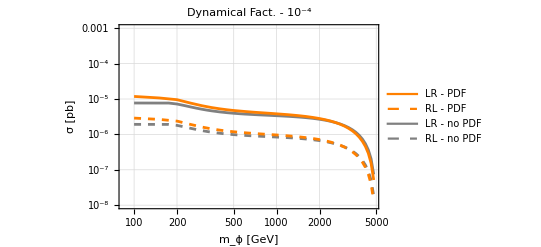

```mathematica
Legended[Show[
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["L"][[1;;-2]],Joined->True,PlotStyle->Gray,PlotRange->{10^-3,10^-8},FrameLabel->{"m_ϕ [GeV]","σ [pb]"},PlotLabel->"Dynamical Fact. - 10^-4"],
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["R"][[1;;-2]],Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[massxsecall4dyn["L"],Joined->True,PlotStyle->Orange],
ListLogLogPlot[massxsecall4dyn["R"],Joined->True,PlotStyle->{Orange,Dashed}]

],Placed[LineLegend[{Orange,{Dashed,Orange},Gray,{Dashed,Gray}},{"LR - PDF","RL - PDF","LR - no PDF","RL - no PDF"}],{0.2,0.25}]]//frametrick
```

VBF initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["VBF"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_uR_vv_to_phiphibar_chichiuubar.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
listinputs["VBF"]={};
Do[
tst=Select[guide["VBF"],#[[2]]=="mphi_"<>ToString[masses]<>".0"&];
tstdirectory=tst[[1,1]];
tstlabel="u_"<>tst[[1,2]]<>"_VBF";
xsec[tstlabel]=tst[[1,3]];
AppendTo[listinputs["VBF"],{"../../../flavorDM2_lhe/Events_u_VBF/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs["VBF"];
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

## Reading lhe files from the names defined above - and calculating all observables. Takes a while. SKIP NOW: already saved data

```mathematica
listinputs["R"][[1;;1]]
```

{{../../../flavorDM2_lhe/Events_u_R/run_01/unweighted_events.lhe,u_mphi_100.0_switch_0_0,{1,2},1.01571×10^-6,{True,{1,2}},{True,{1,2}}}}

Reading LHE files and calculating everything - MT2 included. 
Works for both VBF or μμ: just run different blocks in the section above.
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
listinputs["L"][[3]]
listinputs["VBF"][[3]]
```

{../../../flavorDM2_lhe/Events_u_L/run_91/unweighted_events.lhe,u_mphi_100.0_switch_1_0,{1,2},2.99981×10^-6,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/Events_u_VBF/run_05/unweighted_events.lhe,u_mphi_200.0_VBF,{1,2},0.0000370301,{True,{1,2}},{True,{1,2}}}

```mathematica
(*(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[LRRL][[ii,1]];
{finindices[label],xsec[label],mjjdata[label],MT2data[label]}=listinputs[LRRL][[ii,{3,4,5,6}]];

importmodule[filename[label],label,finindices[label]];

If[mjjdata[label][[1]],Print["Calculating mjj"];mjjlist[label]=mjjlistcalc[label,mjjdata[label][[2]]]];
If[MT2data[label][[1]],Print["Calculating MT2"];MT2list[label]=MT2listcalculator[label,MT2data[label][[2]]]];
Print["=============== Done with label: "<>label<>"==============="];


evententry[label]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

Export["../../../flavorDM2_lhe/saved_data_u/"<>label<>".dat",evententry[label]];

Print["=============== Event Entry Exported: "<>label<>"==============="];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]*)
```

Bkg lhe import:
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
(*(**)
SetDirectory[NotebookDirectory[]];
bkglabel="bkg_u_ll";
(*importmodule["../../../flavorDM2/lhe_files/uR_model_bkg/uR_bkg_jjvv_mjj100.lhe",bkglabel,{1,2}];*)
importmodule["../../../flavorDM2/lhe_files/uR_model_bkg/uR_bkg_jjvv_extracuts.lhe",bkglabel,{1,2}];
mjjlist[bkglabel]=mjjlistcalc[bkglabel,{1,2}];
MT2list[bkglabel]=MT2listcalculator[bkglabel,{1,2}];*)
```

```mathematica
(*evententry["u",bkglabel]=Table[{{"η",etalist[bkglabel][[ii]]},{"pT",pTlist[bkglabel][[ii]]},{"pTvec",pTveclist[bkglabel][[ii]]},{"fourvec",fourvecslist[bkglabel][[ii]]},{"ET",ETlist[bkglabel][[ii]]},{"beta",betalist[bkglabel][[ii]]},{"gamma",gammalist[bkglabel][[ii]]},{"MT2",MT2list[bkglabel][[ii]]},{"mjj",mjjlist[bkglabel][[ii]]}},{ii,1,Length[etalist[bkglabel]]}];

Export["../../../flavorDM2_lhe/saved_data_u/"<>bkglabel<>".dat",evententry["u",bkglabel]];*)
```

```mathematica
(*evententry["u",bkglabel][[1]]*)
```

### MT2 comparison to aria

```mathematica
pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;
```

```mathematica
(*pouyamt2=MT2list[label];*)
pouyamt2new=MT2list[label];
```

```mathematica
Histogram[pouyamt2new/ariamt2,{0.1},PlotRange->{{0.5,2.5},{1,10^4}},FrameLabel->{"MT2_pouya/MT2_aria"}]//frametrick
```

-Graphics-

-Graphics-

```mathematica
Histogram[pouyamt2,{25},FrameLabel->{"MT2_pouya"}]//frametrick
Histogram[pouyamt2new,{25},FrameLabel->{"MT2_pouya"}]//frametrick
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[evententry["L",500,"_switch_0_0"],#[[-2,2]]>=500&]//Length
```

398

```mathematica
(*pouyamt2=#[[-2,2]]&/@evententry["L",500,"_switch_0_0"];
ariamt2=Import["MT2_test_aria.csv","Table"]//Flatten;*)
```

```mathematica
pouyamt2[[1;;22]]
ariamt2[[1;;22]]
```

{232.011,207.216,167.936,96.7128,201.31,163.765,444.962,128.659,87.4183,489.129,4.51487,143.431,97.9494,393.805,83.9932,136.572,21.8336,368.398,95.4135,121.853,53.2748,112.125}

{231.972,201.592,101.669,96.334,196.927,155.84,430.136,93.5088,87.328,286.936,2.98635,143.431,97.919,393.804,78.2696,136.435,20.8355,367.193,93.4874,94.2818,45.1187,88.7516}

```mathematica
Histogram[pouyamt2/ariamt2]
```

-Graphics-

## Importing the “evententry” data of each event XSECTIONS MULTIPLIED BY 4 FOR 4 LEPTON CHANNELS: uu,cc,uc,cu FACTOR 9 ALSO MULTIPLIED HERE SINCE LHE FILES HAD THE WRONG WIDTH AND MISSED 9 IN THE FINAL VALUE.

```mathematica
label
```

u_mphi_4800.0_VBF_VBF

```mathematica
SetDirectory[NotebookDirectory[]];
Do[
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
xsec[label]=If[LRRL!="VBF",9,1] (*Width correction in lhe files*)4(*ll HS 4 FINAL STATE CHANNELS (u,c) BUT XSECTIONS FROM LHE FILES HAS ONLY uu*)listinputs[LRRL][[ii,4]];
,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]
```

```mathematica
Do[
Do[
(*label="L_mphi_"<>ToString[mphi]<>".0"<>labelappend<>"_"<>LRRL;*)
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL(*If[LRRL=="VBF",listinputs[LRRL][[ii,2]],listinputs[LRRL][[ii,2]]<>"_"<>LRRL]*);
evententry[label]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_u/"<>label<>".dat","TSV"]];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}];
Print["Label Done: "<>label];
,{LRRL,{"L","R","VBF"}}]
```

Label Done: u_mphi_4800.0_switch_1_1_L

Label Done: u_mphi_4800.0_switch_1_1_R

Label Done: u_mphi_4800.0_VBF_VBF

```mathematica
evententry["u_mphi_100.0_switch_0_0_L"][[1]]
evententry["u_mphi_100.0_VBF_VBF"][[1]]
```

{{η,{0.344731,-0.350574}},{pT,{2461.67,2615.71}},{pTvec,{{0,-881.651,-2298.37,0},{0,927.553,2445.73,0}}},{fourvec,{{2609.39,-881.651,-2298.37,865.521},{2778.1,927.553,2445.73,-935.899}}},{ET,{2461.67,2615.71}},{beta,{1.,1.}},{gamma,{0.-198702. ⅈ,0.-161892. ⅈ}},{MT2,9.63702},{mjj,5384.83}}

{{η,{3.03618,0.539666}},{pT,{78.3277,200.926}},{pTvec,{{0,-4.20711,78.2146,0},{0,98.6437,-175.045,0}}},{fourvec,{{817.487,-4.20711,78.2146,813.725},{230.902,98.6437,-175.045,113.774}}},{ET,{78.3277,200.926}},{beta,{1.,1.}},{gamma,{0.-319598. ⅈ,0.-224248. ⅈ}},{MT2,57.1333},{mjj,469.649}}

{{η,{0.344731,-0.350574}},{pT,{2461.67,2615.71}},{pTvec,{{0,-881.651,-2298.37,0},{0,927.553,2445.73,0}}},{fourvec,{{2609.39,-881.651,-2298.37,865.521},{2778.1,927.553,2445.73,-935.899}}},{ET,{2461.67,2615.71}},{beta,{1.,1.}},{gamma,{0.-198702. ⅈ,0.-161892. ⅈ}},{MT2,9.63702},{mjj,5384.83}}

{{η,{3.03618,0.539666}},{pT,{78.3277,200.926}},{pTvec,{{0,-4.20711,78.2146,0},{0,98.6437,-175.045,0}}},{fourvec,{{817.487,-4.20711,78.2146,813.725},{230.902,98.6437,-175.045,113.774}}},{ET,{78.3277,200.926}},{beta,{1.,1.}},{gamma,{0.-319598. ⅈ,0.-224248. ⅈ}},{MT2,57.1333},{mjj,469.649}}

```mathematica
SetDirectory[NotebookDirectory[]];
evententry["u","bkg_u_ll"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_u/"<>"bkg_u_ll"<>".dat","TSV"]];
```

```mathematica
xsec["bkg_u_ll"]=0.0041;
```

```mathematica
evententry["u","bkg_u_ll"][[1]]
```

{{η,{1.87166,0.517759}},{pT,{402.06,501.229}},{pTvec,{{0,-276.92,-291.491,0},{0,354.39,354.455,0}}},{fourvec,{{1337.45,-276.92,-291.491,1275.58},{569.946,354.39,354.455,271.267}}},{ET,{402.087,501.251}},{beta,{0.999994,0.999966}},{gamma,{284.564,121.265}},{MT2,13.2443},{mjj,1111.51}}

## For a test mass, extracting an observables from all events to make hiastograms

{{η,{0.30146,-0.360538}},{pT,{3087.44,4322.67}},{pTvec,{{0,3083.94,146.887,0},{0,-4322.13,68.7921,0}}},{fourvec,{{3228.79,3083.94,146.887,944.899},{4606.68,-4322.13,68.7921,-1592.47}}},{ET,{3087.44,4322.67}},{beta,{1.,1.}},{gamma,{0.-356396. ⅈ,0.-1.28368×10^6 ⅈ}},{MT2,234.243},{mjj,7706.86}}

```mathematica
modellabel="u";
bkglabel="bkg_u_ll";
```

```mathematica
Clear[listlabels]
listlabels["L"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["R"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["VBF"]={"_VBF"};
```

```mathematica
(*Clear[dataxsecall]*)
Clear[histogramdata]
Do[

Do[
dataxsecall[modellabel,mphi,LRRL]={};
allhistogramdata["MT2"][modellabel,mphi,LRRL]={};
allhistogramdata["mjj"][modellabel,mphi,LRRL]={};
allhistogramdata["pT"][modellabel,mphi,LRRL]={};
allhistogramdata["pTll"][modellabel,mphi,LRRL]={};
allhistogramdata["eta"][modellabel,mphi,LRRL]={};
allhistogramdata["cosθ"][modellabel,mphi,LRRL]={};

Do[
fulllabel=modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label,modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[dataxsecall[modellabel,mphi,LRRL],xsec[fulllabel]];
histogramdata["MT2"][modellabel,mphi,label,LRRL]=#[[-2,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["MT2"][modellabel,mphi,LRRL],histogramdata["MT2"][modellabel,mphi,label,LRRL]];
histogramdata["mjj"][modellabel,mphi,label,LRRL]=#[[-1,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["mjj"][modellabel,mphi,LRRL],histogramdata["mjj"][modellabel,mphi,label,LRRL]];
histogramdata["pT"][modellabel,mphi,label,LRRL]=#[[2,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pT"][modellabel,mphi,LRRL],histogramdata["pT"][modellabel,mphi,label,LRRL]];
histogramdata["pTll"][modellabel,mphi,label,LRRL]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pTll"][modellabel,mphi,LRRL],histogramdata["pTll"][modellabel,mphi,label,LRRL]];
histogramdata["eta"][modellabel,mphi,label,LRRL]=#[[1,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["eta"][modellabel,mphi,LRRL],histogramdata["eta"][modellabel,mphi,label,LRRL]];
histogramdata["cosθ"][modellabel,mphi,label,LRRL]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[fulllabel];
AppendTo[allhistogramdata["cosθ"][modellabel,mphi,LRRL],histogramdata["cosθ"][modellabel,mphi,label,LRRL]];

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];

dataxsecall[modellabel,mphi]={Riffle[dataxsecall[modellabel,mphi,"L"],dataxsecall[modellabel,mphi,"R"]]};
AppendTo[dataxsecall[modellabel,mphi],dataxsecall[modellabel,mphi,"VBF"]];



order={9,7,8,3,4,5,6,1,2}; (*ORDER FOR PRESENTATION IN THE HISTOGRAM*)

dataxsecall[modellabel,mphi]=Flatten[dataxsecall[modellabel,mphi],1][[order]];
Do[
allhistogramdata[obs][modellabel,mphi]={Riffle[allhistogramdata[obs][modellabel,mphi,"L"],allhistogramdata[obs][modellabel,mphi,"R"]]};
AppendTo[allhistogramdata[obs][modellabel,mphi],allhistogramdata[obs][modellabel,mphi,"VBF"]];
allhistogramdata[obs][modellabel,mphi]=Flatten[allhistogramdata[obs][modellabel,mphi],1][[order]];
,{obs,{"MT2","mjj","pT","pTll","eta","cosθ"}}]

,{mphi,masslist}]



(*BKG Data*)
Do[
histogramdata["MT2"][modellabel,bkglabel]=#[[-2,2]]&/@evententry[modellabel,bkglabel];
histogramdata["mjj"][modellabel,bkglabel]=#[[-1,2]]&/@evententry[modellabel,bkglabel];
histogramdata["pT"][modellabel,bkglabel]=#[[2,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["pTll"][modellabel,bkglabel]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[modellabel,bkglabel];
histogramdata["eta"][modellabel,bkglabel]=#[[1,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["cosθ"][modellabel,bkglabel]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[modellabel,bkglabel];


,{bkglabel,{"bkg_u_ll"}}
]
```

## Histograms 1D: USE PDF FUNCTION BUT IT INTRODUCES SOME RANDOM NORMALIZATION THAT SHOULD BE FIXED BY HAND TO AGREE WITH THE PROPER DISCRETE CALC. I STILL KEPT IN THE PLOT PART.

```mathematica
mphitst=2800;
bkglabel="bkg_u_ll";
modellabel="u";
```

```mathematica
tst=weightedmixmaker[allhistogramdata["eta"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["eta"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-2.4;maxx=2.4;stepx=0.2;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,PDF[helper,#]}&/@binsdata;
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

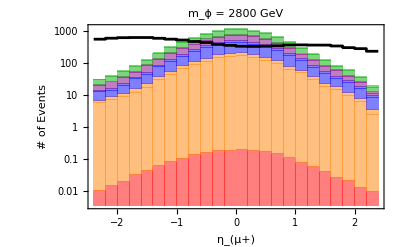

```mathematica
plt=Show[
Histogram[tst,{minx,maxx,0.2},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},Full}]//frametricknogrid,


(*Histogram[bkgtst,{0.2},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

(*ListLinePlot[bkgtstss,InterpolationOrder->0,PlotStyle->Black,ScalingFunctions->"Log"],*)
Plot[2 10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},Full}]
]
```

```mathematica
Export["u_histogrameta_"<>ToString[mphitst]<>".pdf",plt]
```

u_histogrameta_2800.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["cosθ"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["cosθ"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-1;maxx=1;stepx=0.1;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.1 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdataeta["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataeta["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataeta["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

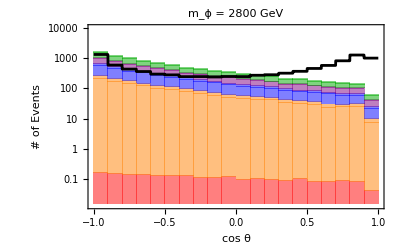

```mathematica
plt=Show[
Histogram[tst,{0.1},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},{1.33 10^-2,10^4}}]//frametricknogrid,


(*Histogram[bkgtst,{0.1},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

```mathematica
Export["u_histogramcos_"<>ToString[mphitst]<>".pdf",plt]
```

u_histogramcos_2800.pdf

FOR BELOW, FOR 0.2 AND 2.8 TEV THE RANGE AND THE STEPSIZE AND THE NORMALIZATION FACTOR ADDED TO MAKE THE PDF FUNCTION WORK RIGHT ARE DIFFERENT. CHANGE FOR EACH

```mathematica
tst=weightedmixmaker[allhistogramdata["MT2"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["MT2"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=0;maxx=(*250*)(*1100*)3000;stepx=(*50*)100;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdataMT2["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataMT2["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataMT2["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

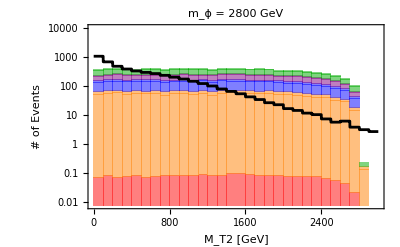

```mathematica
plt=Show[
Histogram[tst,{(*10*)(*50*)100},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{0,(*250*)(*1100*)3000},{(*2.5 10^-3*) 8 10^-3,10^4}}]//frametricknogrid,

(*Histogram[bkgtst,{(*10*)50(*100*)},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,*)

Plot[ (*10^5*)0.5 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]

]
```

```mathematica
Export["u_histogramMT2_"<>ToString[mphitst]<>".pdf",plt]
```

u_histogramMT2_2800.pdf

## New Cut Module and Reach Plots

```mathematica
(*Sort[#[[-1,2]]&/@evententry[fulllabel],#1<=#2&]*)
```

```mathematica
Clear[cutmodule]
cutmodule[modelLuQ_,mphi_,cutmjj_,cutpTll_,cutMT2_,etacut_,costhcut_,cuttotE_,cutMET_][flagPDF_,minbkg_]:=Module[{},

alllabelslist={};
Do[Do[
fulllabel=modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label,modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[alllabelslist,fulllabel];

signalevents[fulllabel]=Select[evententry[fulllabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[signalevents[modelLuQ,mphi,channindx]]]];*)

aftercutweight[fulllabel]=Length[signalevents[fulllabel]]/Length[evententry[fulllabel]];

(*since 2 μ in the final state*)
evencount[fulllabel]=aftercutweight[fulllabel] xsec[fulllabel] 10^7 If[flagPDF==True,1,1/(coeff["_switch_0_0"]["L"][mphi])](*to get the noPDF case*);
(*Luminosity at a 10 TeV MuC in pb^-1*)

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];


bkgevents[modelLuQ]=Select[evententry[modelLuQ,bkglabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[bkgevents[modelLuQ]]]];*)

aftercutweight[bkglabel]=Length[bkgevents[modelLuQ]]/Length[evententry[modelLuQ,bkglabel]];

(*since 2 μ in the final state*)
evencount[bkglabel]=Max[minbkg,aftercutweight[bkglabel] xsec[bkglabel] 10^7];
(*Luminosity at a 10 TeV MuC in pb^-1*)


{{"Signal Count",Tr[Table[evencount[channindx],{channindx,If[flagPDF==True,alllabelslist,alllabelslist[[{1,5}]]]}]]},{"Bkg Count",evencount[bkglabel]}}

]
```

```mathematica
mphitst=4200;
minbkgumodel=xsec[bkglabel] 10^7 10 10^-5;
cutmodule[modellabel,mphitst,{1500,200000},{0,20000},{1600,20000},0.7,(*-0.75*)Cos[π/180 45],{1600,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]
(%[[1]])/(√(%[[2]]))
(*cutmodule[modellabel,mphitst,{400,200000},{800,400000},{300,2000},1.2,-0.75(*Cos[π/180 140]*),{0,40000},{0,40000}][False,minbkgumodel][[{1,2},2]]
(%[[1]])/(√(%[[2]]))*)
```

{71.2592,178.76}

5.32973

{71.2592,178.76}

5.32973

Optimized for m=4200 TeV: mjj > 1500, pTll > 0, MT2> 1600, |eta|<0.7, θ >45, Etot > 1600

{71.2592,178.76}

5.32973

Optimized for m=1600 TeV: mjj > 3600, pTll > 0, MT2> 400, |eta|<0.5, θ >140, Etot > 900

{357.497,175.07}

27.0188

### Plots

```mathematica
Cos[π/180 140]//N
```

-0.766044

```mathematica
tablescanmjjptMT2in[mphi_][mjjmax_,ptmax_,MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){mjjscan,ptscan,cutmodule["u",mphi,{mjjscan,mjjmax},{ptscan,ptmax},MT2range,0.2,Cos[π/180 150]][True,minbkgumodel][[{1,2},2]]},{mjjscan,0,2000,250},{ptscan,0,2000,250}],1]
tablescanetacosthMT2in[mphi_][MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){etascan,cosscan,cutmodule["u",mphi,{300,100000},{0,100000},MT2range,etascan,cosscan,{750,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]},{etascan,0.2,1.5,0.1},{cosscan,-0.95,-0.3,0.05}],1]
```

```mathematica
mphitst=2800;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{400,50000},(*{500,50000},*){600,50000},(*{700,50000},*){800,50000}(*{200,50000},{600,50000},{700,50000},{1000,50000}*)}}]
```

### PDF vs noPDF

New SRs

```mathematica
pdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{3600,200000},{0,400000},{400,100000},0.5,Cos[π/180 140],{900,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
pdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{1500,200000},{0,400000},{1600,100000},0.7,Cos[π/180 45],{1600,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1,Joined->True,PlotRange->{{200,5000},{1,90}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\sigma",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Significance} ~ (u~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,

LogPlot[5,{x,0,10^4},PlotStyle->{Dashed,Thickness[0.003],Blue}],

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^q",FontSize->16],MaTeX["\\mathrm{SR}_2^q",FontSize->16]}],{0.8,0.8}]]
```

-Graphics-

```mathematica
Export["u_sig_reach.pdf",plt]
```

u_sig_reach.pdf

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR1,Joined->True,PlotRange->{{200,5000},{10,2000}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\mathrm{sys.}/\\mathrm{stat.}~[\\%]",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Tolerable~Systematics} ~ (u~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR2,Joined->True,PlotStyle->{{Orange}}]//frametricknogrid,

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^q",FontSize->16],MaTeX["\\mathrm{SR}_2^q",FontSize->16]}],{0.8,0.8}]]
```

-Graphics-

```mathematica
Export["tolerated_u.pdf",plt]
```

tolerated_u.pdf

```mathematica
yrs=Range[2000,2024,4];
Rlist={50.46,62.04,59.95,60.93,62.98,74.22,71.29+3.91 1/0.54};
Rlist=Partition[Riffle[yrs,Rlist],2];
Dlist={51.00,59.03,69.50,65.92,65.85,81.28,66.36+5.60 1/0.54};
Dlist=Partition[Riffle[yrs,Dlist],2];
ListPlot[{Rlist,Dlist},PlotStyle->{Red,Blue},Joined->True]//frametrick
```

-Graphics-

### SRs reach

SR200

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={100,100000};
etacutSR=0.3;
coscutSR=Cos[π/180 160];
```

```mathematica
dataSR200=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{1.53745,60.24}},{200,{201.423,60.24}},{300,{285.573,60.24}},{400,{311.584,60.24}},{500,{314.538,60.24}},{600,{298.593,60.24}},{800,{256.573,60.24}},{1000,{213.613,60.24}},{1200,{171.939,60.24}},{1600,{109.053,60.24}},{2000,{67.2295,60.24}},{2400,{42.2668,60.24}},{2800,{25.1495,60.24}},{3200,{15.3297,60.24}},{3600,{8.23689,60.24}},{4000,{3.53732,60.24}},{4400,{1.28243,60.24}},{4800,{0.17394,60.24}}}

```mathematica
sysfraction200={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR200
```

{{100,0.},{200,509.312},{300,729.051},{400,796.652},{500,804.322},{600,762.9},{800,653.542},{1000,541.287},{1200,431.626},{1600,262.618},{2000,141.464},{2400,43.1557},{2800,0.},{3200,0.},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction200,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR200,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR2800

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={700,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 120];
```

```mathematica
dataSR2800=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40.16}},{200,{0.,40.16}},{300,{0.,40.16}},{400,{0.,40.16}},{500,{0.,40.16}},{600,{0.,40.16}},{800,{19.1563,40.16}},{1000,{66.8356,40.16}},{1200,{92.5872,40.16}},{1600,{115.406,40.16}},{2000,{107.497,40.16}},{2400,{88.9282,40.16}},{2800,{67.3912,40.16}},{3200,{45.3082,40.16}},{3600,{26.2088,40.16}},{4000,{14.3701,40.16}},{4400,{5.2646,40.16}},{4800,{0.744566,40.16}}}

```mathematica
sysfraction2800={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR2800
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,0.},{1000,185.72},{1200,274.559},{1600,350.222},{2000,324.185},{2400,262.235},{2800,187.71},{3200,102.208},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction2800,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR2800,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR3600

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={600,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 130];
```

```mathematica
dataSR3600=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40}},{200,{0.,40}},{300,{0.,40}},{400,{0.,40}},{500,{0.,40}},{600,{0.,40}},{800,{49.8266,40}},{1000,{92.3356,40}},{1200,{109.471,40}},{1600,{116.803,40}},{2000,{100.998,40}},{2400,{77.9031,40}},{2800,{55.8582,40}},{3200,{36.5984,40}},{3600,{20.8445,40}},{4000,{10.8762,40}},{4400,{3.78136,40}},{4800,{0.545746,40}}}

```mathematica
sysfraction3600={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR3600
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,121.766},{1000,274.333},{1200,331.421},{1600,355.57},{2000,303.323},{2400,225.142},{2800,145.607},{3200,58.2619},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction3600,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"}]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR3600,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

### Other

```mathematica
Do[

 Print[xsec["L_mphi_"<>ToString[mphitst]<>".0"<>channindx] ]

,{channindx,listlabels[[2;;4]]}]
```

2.62474×10^-7

1.67179×10^-6

2.60301×10^-6

Check SRs

```mathematica
mjjtst=990;
(*probably 2 i add above was already in her xsec. she found σ~0.2*)
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{3500,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{1800,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{200,100000}][[{1,2},2]]&/@{1300,750,200}
```

{{0.,0.},{0.,0.},{0.,0.}}

{{0.,2040.},{0.,2040.},{0.,2040.}}

{{7.04978,20300.},{9.96491,49510.},{12.041,66040.}}

{{0.,70.7547},{0.,70.7547},{0.,70.7547}}

{{0.,2031.67},{0.,2031.67},{0.,2031.67}}

{{7.04978,20306.6},{9.96491,49386.8},{12.041,66256.7}}

# PROMPT Q Model

## Generating all lhe file names and reading xsections

```mathematica
(*allmasses=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union*)
allmasses=Flatten[{Range[100,500,50],Range[500,1000,100],Range[1000,4800,200]}]//Union
masslist=allmasses;
ariamasslist=Flatten[{Range[100,350,25],Range[350,800,50],Range[800,1600,100],Range[1600,4800,200]}]//Union
```

{100,150,200,250,300,350,400,450,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

{100,125,150,175,200,225,250,275,300,325,350,400,450,500,550,600,650,700,750,800,900,1000,1100,1200,1300,1400,1500,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800}

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[cLfunc,cRfunc]
cstable=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em4.csv","CSV"]];
cfunc["L"]=Interpolation[#[[{1,2}]]&/@cstable]
cfunc["R"]=Interpolation[#[[{1,3}]]&/@cstable]
(*cstable8=ToExpression[Import["../../../flavorDM2_lhe/c_vs_Q_grid_resc1em8.csv","CSV"]];
cLfunc8=Interpolation[#[[{1,2}]]&/@cstable8]
cRfunc8=Interpolation[#[[{1,3}]]&/@cstable8]*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Show[
LogLinearPlot[cfunc["L"][m],{m,100,10000}],
LogLinearPlot[cfunc["R"][m],{m,100,10000},PlotStyle->Red]
]//frametrick
(*Show[
LogLinearPlot[cLfunc8[m],{m,100,10000}],
LogLinearPlot[cRfunc8[m],{m,100,10000},PlotStyle->Red]
]//frametrick*)
```

-Graphics-

μμ initial preparing for lhe imports:

```mathematica
Clear[guide]
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["L"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_QL_muLmuR_to_phiphibar_chichijj_resc1e-4_fact_dyn.txt","Table"];
guide["R"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_QL_muRmuL_to_phiphibar_chichijj_resc1e-4_fact_dyn.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
guide["R"][[2]]
guide["L"][[77]]
```

{run_01,mphi_100.0_switch_0_0,0.00251227,2.07809×10^-6,10000}

{run_76,mphi_2200.0_switch_0_1,9.1677×10^-6,3.95676×10^-8,10000}

```mathematica
noPDFxsec["L"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["L"][[2;;46]]
noPDFxsec["R"]={ToExpression[StringSplit[#[[2]],"_"][[2]]],#[[3]]}&/@guide["R"][[2;;46]]
```

{{100.,0.0000956538},{125.,0.00009564},{150.,0.000095573},{175.,0.0000954896},{200.,0.0000913534},{225.,0.0000854267},{250.,0.0000803751},{275.,0.0000761294},{300.,0.0000731189},{325.,0.0000705342},{350.,0.0000686394},{400.,0.0000658096},{450.,0.0000640109},{500.,0.0000625403},{550.,0.0000614481},{600.,0.0000606367},{650.,0.0000599695},{700.,0.0000593157},{750.,0.0000588522},{800.,0.0000582408},{900.,0.0000573772},{1000.,0.000056337},{1100.,0.0000553843},{1200.,0.0000544772},{1300.,0.0000535539},{1400.,0.0000524901},{1500.,0.0000514219},{1600.,0.0000503252},{1800.,0.0000479652},{2000.,0.0000453924},{2200.,0.0000426313},{2400.,0.0000396877},{2600.,0.0000365222},{2800.,0.0000333507},{3000.,0.000029969},{3200.,0.0000265161},{3400.,0.0000229795},{3600.,0.0000194719},{3800.,0.0000159549},{4000.,0.0000125178},{4200.,9.2478×10^-6},{4400.,6.1956×10^-6},{4600.,3.47377×10^-6},{4800.,1.2623×10^-6},{5000.,4.75414×10^-14}}

{{100.,0.00251227},{125.,0.00251319},{150.,0.00250979},{175.,0.00250762},{200.,0.00238679},{225.,0.00221627},{250.,0.00206608},{275.,0.00194458},{300.,0.00185691},{325.,0.00178135},{350.,0.0017256},{400.,0.00164504},{450.,0.0015903},{500.,0.00155038},{550.,0.00152048},{600.,0.00149526},{650.,0.00147911},{700.,0.00145974},{750.,0.00144683},{800.,0.00143141},{900.,0.00140665},{1000.,0.00137999},{1100.,0.00135689},{1200.,0.00133356},{1300.,0.00131041},{1400.,0.00128489},{1500.,0.00125773},{1600.,0.00123034},{1800.,0.00117175},{2000.,0.00110894},{2200.,0.00104064},{2400.,0.000969025},{2600.,0.000892252},{2800.,0.000813505},{3000.,0.000731195},{3200.,0.000647139},{3400.,0.000560695},{3600.,0.000475729},{3800.,0.000389211},{4000.,0.000305658},{4200.,0.000225696},{4400.,0.000151301},{4600.,0.000084776},{4800.,0.000030814},{5000.,1.16237×10^-12}}

```mathematica
Clear[coeff]
coeff["_switch_0_0"]["L"][m_]:=  cfunc["L"][m] cfunc["R"][m];
coeff["_switch_0_0"]["R"][m_]:=  cfunc["L"][m] cfunc["R"][m];
(*coeff["_switch_0_1"]["L"][m_]:=  cfunc["L"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];*)
coeff["_switch_0_1"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_0_1"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_0"]["L"][m_]:=  cfunc["R"][m];
coeff["_switch_1_0"]["R"][m_]:=  cfunc["L"][m];
coeff["_switch_1_1"]["L"][m_]:=1;
coeff["_switch_1_1"]["R"][m_]:=1;
(*coeff["_VBF"]=1;*)
```

```mathematica
guide["R"][[{26,71,116,161}]]
```

{{run_25,mphi_1300.0_switch_0_0,0.00131041,1.21426×10^-6,10000},{run_70,mphi_1300.0_switch_0_1,0.000289177,4.80698×10^-7,10000},{run_115,mphi_1300.0_switch_1_0,0.000289127,4.49776×10^-7,10000},{run_160,mphi_1300.0_switch_1_1,0.0000625675,1.65398×10^-7,10000}}

```mathematica
Clear[listinputs]
listinputs["L"]={};
listinputs["R"]={};
Do[
Do[
Do[
tst=Select[guide[LRRL],#[[2]]=="mphi_"<>ToString[masses]<>".0"<>labelappend&];
tstdirectory=tst[[1,1]];
tstlabel="Q_"<>tst[[1,2]];
(*xsec[tstlabel]=coeff[labelappend]tst[[1,3]];*)
xsec[tstlabel]=coeff[labelappend][LRRL][masses]tst[[1,3]];
AppendTo[listinputs[LRRL],{"../../../flavorDM2_lhe/Events_Q_"<>LRRL<>"/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{labelappend,{"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"}}]

,{masses,allmasses}]

,{LRRL,{"L","R"}}]
listinputs["L"];
listinputs["R"];
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

```mathematica
listinputs["R"][[4]]
```

{../../../flavorDM2_lhe/Events_Q_R/run_136/unweighted_events.lhe,Q_mphi_100.0_switch_1_1,{1,2},0.000143891,{True,{1,2}},{True,{1,2}}}

```mathematica
(*dynamic 10^-4*)
Clear[xsecall4dyn,massxsecall4dyn]
Do[
xsecall4dyn[LRRL]=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs[LRRL],4];
massxsecall4dyn[LRRL]=Partition[Riffle[allmasses,xsecall4dyn[LRRL]],2]
,{LRRL,{"L","R"}}]
(*10^-4*)
(*xsecall4=#[[1]]+#[[2]]+#[[3]]&/@Partition[#[[4]]&/@listinputs,3]
massxsecall4=Partition[Riffle[allmasses,xsecall4],2]*)
(*10^-8*)
(*xsecall8=#[[1]]+#[[2]]+#[[3]]+#[[4]]&/@Partition[#[[4]]&/@listinputs,4]
massxsecall8=Partition[Riffle[allmasses,xsecall8],2]*)
```

```mathematica
Legended[Show[
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["L"][[1;;-2]],Joined->True,PlotStyle->Gray,PlotRange->{10^-3,10^-8},FrameLabel->{"m_ϕ [GeV]","σ [pb]"},PlotLabel->"Dynamical Fact. - 10^-4"],
ListLogLogPlot[{#[[1]],1/4(*spin avg*)#[[2]]}&/@noPDFxsec["R"][[1;;-2]],Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[massxsecall4dyn["L"],Joined->True,PlotStyle->Orange],
ListLogLogPlot[massxsecall4dyn["R"],Joined->True,PlotStyle->{Orange,Dashed}]

],Placed[LineLegend[{Orange,{Dashed,Orange},Gray,{Dashed,Gray}},{"LR - PDF","RL - PDF","LR - no PDF","RL - no PDF"}],{0.2,0.25}]]//frametrick
```

-Graphics-

VBF initial preparing for lhe imports:

```mathematica
SetDirectory[NotebookDirectory[]];
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-8.txt","Table"]*)
(*guide=Import["../../../flavorDM2_lhe/cross_section_fermportal_LL_muLmuR_to_phipphim_chichimumu_resc1e-4.txt","Table"]*)
guide["VBF"]=Import["../../../flavorDM2_lhe/cross_section_fermportal_QL_vv_to_phiphibar_chichijj.txt","Table"];
(*testmassstring="2000.0";*)
```

```mathematica
listinputs["VBF"]={};
Do[
tst=Select[guide["VBF"],#[[2]]=="mphi_"<>ToString[masses]<>".0"&];
tstdirectory=tst[[1,1]];
tstlabel="Q_"<>tst[[1,2]]<>"_VBF";
xsec[tstlabel]=tst[[1,3]];
AppendTo[listinputs["VBF"],{"../../../flavorDM2_lhe/Events_Q_VBF/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2},xsec[tstlabel],{True,{1,2}},{True,{1,2}}}]
,{masses,(*{500,1000,2000,3000,4000}*)allmasses}]
listinputs["VBF"];
(*importmodule["../../../flavorDM2_lhe/Events/"<>tstdirectory<>"/unweighted_events.lhe",tstlabel,{1,2}]*)
```

## Reading lhe files from the names defined above - and calculating all observables. Takes a while. SKIP NOW: already saved data

Reading LHE files and calculating everything - MT2 included. 
Works for both VBF or μμ: just run different blocks in the section above.
===========WILL TAKE A LONG TIME TO GENERATE================

```mathematica
(*(*import all files, calculate kinematics for each event of each file, including MT2 - if applicable.*)
SetDirectory[NotebookDirectory[]];
Do[
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Print["&&&&&&&&&&&&&&&&&&&&&&"<>LRRL<>"&&&&&&&&&&&&&&&&&&&&"];
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
Print["=============== Making the lists for label: "<>label<>"===============\n"];
filename[label]=listinputs[LRRL][[ii,1]];
{finindices[label],xsec[label],mjjdata[label],MT2data[label]}=listinputs[LRRL][[ii,{3,4,5,6}]];

importmodule[filename[label],label,finindices[label]];

If[mjjdata[label][[1]],Print["Calculating mjj"];mjjlist[label]=mjjlistcalc[label,mjjdata[label][[2]]]];
If[MT2data[label][[1]],Print["Calculating MT2"];MT2list[label]=MT2listcalculator[label,MT2data[label][[2]]]];
Print["=============== Done with label: "<>label<>"==============="];


evententry[label]=Table[{{"η",etalist[label][[ii]]},{"pT",pTlist[label][[ii]]},{"pTvec",pTveclist[label][[ii]]},{"fourvec",fourvecslist[label][[ii]]},{"ET",ETlist[label][[ii]]},{"beta",betalist[label][[ii]]},{"gamma",gammalist[label][[ii]]},{"MT2",MT2list[label][[ii]]},{"mjj",mjjlist[label][[ii]]}},{ii,1,Length[etalist[label]]}];

Export["../../../flavorDM2_lhe/saved_data_Q/"<>label<>".dat",evententry[label]];

Print["=============== Event Entry Exported: "<>label<>"==============="];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]*)
```

Bkg lhe import: use the u model
===========WILL TAKE A LONG TIME TO GENERATE================

## Importing the “evententry” data of each event Already final states are j j, so no factor of 4 or something needed for the xsection

```mathematica
listinputs["VBF"][[1]]
listinputs["L"][[1]]
```

{../../../flavorDM2_lhe/Events_Q_VBF/run_01/unweighted_events.lhe,Q_mphi_100.0_VBF,{1,2},0.0086577,{True,{1,2}},{True,{1,2}}}

{../../../flavorDM2_lhe/Events_Q_L/run_01/unweighted_events.lhe,Q_mphi_100.0_switch_0_0,{1,2},0.0000126395,{True,{1,2}},{True,{1,2}}}

```mathematica
masslist[[-6]]
```

3800

```mathematica
listinputs["VBF"][[1]]
```

{../../../flavorDM2_lhe/Events_Q_VBF/run_01/unweighted_events.lhe,Q_mphi_100.0_VBF,{1,2},0.0086577,{True,{1,2}},{True,{1,2}}}

```mathematica
SetDirectory[NotebookDirectory[]];
Do[
Do[
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL;
xsec[label]=listinputs[LRRL][[ii,4]];
,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}]
,{LRRL,{"L","R","VBF"}}]
```

```mathematica
Do[
Do[
(*label=If[LRRL=="VBF",listinputs[LRRL][[ii,2]],listinputs[LRRL][[ii,2]]<>"_"<>LRRL];*)
label=listinputs[LRRL][[ii,2]]<>"_"<>LRRL(*If[LRRL=="VBF",listinputs[LRRL][[ii,2]],listinputs[LRRL][[ii,2]]<>"_"<>LRRL]*);
evententry[label]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_Q/"<>label<>".dat","TSV"]];

,{ii,1,Length[listinputs[LRRL](*[[1;;1]]*)]}];
Print["Label Done: "<>label];
,{LRRL,{"L","R","VBF"}}]
```

Label Done: Q_mphi_4800.0_switch_1_1_L

Label Done: Q_mphi_4800.0_switch_1_1_R

Label Done: Q_mphi_4800.0_VBF_VBF

```mathematica
evententry["Q_mphi_100.0_switch_0_0_L"][[1]]
evententry["Q_mphi_100.0_VBF_VBF"][[1]]
```

{{η,{0.564072,-0.565189}},{pT,{3585.09,437.714}},{pTvec,{{0,-1464.15,3272.48,0},{0,155.004,-409.35,0}}},{fourvec,{{4170.72,-1464.15,3272.48,2131.2},{509.506,155.004,-409.35,-260.774}}},{ET,{3585.09,437.714}},{beta,{1.,1.}},{gamma,{0.-448097. ⅈ,182885.}},{MT2,73.5547},{mjj,2914.55}}

{{η,{0.697663,-0.308547}},{pT,{160.306,25.5492}},{pTvec,{{0,52.1117,151.6,0},{0,24.0248,-8.69312,0}}},{fourvec,{{200.928,52.1117,151.6,121.136},{26.775,24.0248,-8.69312,-8.0088}}},{ET,{160.306,25.5492}},{beta,{1.,1.}},{gamma,{0.-194954. ⅈ,811998.}},{MT2,89.7757},{mjj,113.277}}

{{η,{0.564072,-0.565189}},{pT,{3585.09,437.714}},{pTvec,{{0,-1464.15,3272.48,0},{0,155.004,-409.35,0}}},{fourvec,{{4170.72,-1464.15,3272.48,2131.2},{509.506,155.004,-409.35,-260.774}}},{ET,{3585.09,437.714}},{beta,{1.,1.}},{gamma,{0.-448097. ⅈ,182885.}},{MT2,73.5547},{mjj,2914.55}}

{{η,{0.697663,-0.308547}},{pT,{160.306,25.5492}},{pTvec,{{0,52.1117,151.6,0},{0,24.0248,-8.69312,0}}},{fourvec,{{200.928,52.1117,151.6,121.136},{26.775,24.0248,-8.69312,-8.0088}}},{ET,{160.306,25.5492}},{beta,{1.,1.}},{gamma,{0.-194954. ⅈ,811998.}},{MT2,89.7757},{mjj,113.277}}

Q model bkg lhe file is the same as the u model lhe file.

```mathematica
SetDirectory[NotebookDirectory[]];
(*evententry["L","bkg_L"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L"<>".dat","TSV"]];
evententry["L","bkg_L_old"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data/"<>"bkg_L_old"<>".dat","TSV"]];*)
(*evententry["L","bkg_L_cut200"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_L/"<>"bkg_L_cut200"<>".dat","TSV"]];*)
evententry["Q","bkg_Q_ll"]=ToExpression[Import["../../../flavorDM2_lhe/saved_data_u/"<>"bkg_u_ll"<>".dat","TSV"]];
```

```mathematica
(*xsec["bkg_L_old"]=0.1;
xsec["bkg_L"]=0.1;*)
(*xsec["bkg_L_cut200"]=0.010886;*)
xsec["bkg_Q_ll"]=0.0041;
```

```mathematica
evententry["Q","bkg_Q_ll"][[1]]
```

{{η,{1.87166,0.517759}},{pT,{402.06,501.229}},{pTvec,{{0,-276.92,-291.491,0},{0,354.39,354.455,0}}},{fourvec,{{1337.45,-276.92,-291.491,1275.58},{569.946,354.39,354.455,271.267}}},{ET,{402.087,501.251}},{beta,{0.999994,0.999966}},{gamma,{284.564,121.265}},{MT2,13.2443},{mjj,1111.51}}

{{η,{1.87166,0.517759}},{pT,{402.06,501.229}},{pTvec,{{0,-276.92,-291.491,0},{0,354.39,354.455,0}}},{fourvec,{{1337.45,-276.92,-291.491,1275.58},{569.946,354.39,354.455,271.267}}},{ET,{402.087,501.251}},{beta,{0.999994,0.999966}},{gamma,{284.564,121.265}},{MT2,13.2443},{mjj,1111.51}}

## For a test mass, extracting an observables from all events to make hiastograms

```mathematica
modellabel="Q";
bkglabel="bkg_Q_ll";
```

```mathematica
Clear[listlabels]
listlabels["L"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["R"]={"_switch_0_0","_switch_0_1","_switch_1_0","_switch_1_1"};
listlabels["VBF"]={"_VBF"};
```

```mathematica
(*Clear[dataxsecall]*)
Clear[histogramdata]
Do[

Do[
dataxsecall[modellabel,mphi,LRRL]={};
allhistogramdata["MT2"][modellabel,mphi,LRRL]={};
allhistogramdata["mjj"][modellabel,mphi,LRRL]={};
allhistogramdata["pT"][modellabel,mphi,LRRL]={};
allhistogramdata["pTll"][modellabel,mphi,LRRL]={};
allhistogramdata["eta"][modellabel,mphi,LRRL]={};
allhistogramdata["cosθ"][modellabel,mphi,LRRL]={};

Do[
fulllabel=modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label,modellabel<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[dataxsecall[modellabel,mphi,LRRL],xsec[fulllabel]];
histogramdata["MT2"][modellabel,mphi,label,LRRL]=#[[-2,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["MT2"][modellabel,mphi,LRRL],histogramdata["MT2"][modellabel,mphi,label,LRRL]];
histogramdata["mjj"][modellabel,mphi,label,LRRL]=#[[-1,2]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["mjj"][modellabel,mphi,LRRL],histogramdata["mjj"][modellabel,mphi,label,LRRL]];
histogramdata["pT"][modellabel,mphi,label,LRRL]=#[[2,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pT"][modellabel,mphi,LRRL],histogramdata["pT"][modellabel,mphi,label,LRRL]];
histogramdata["pTll"][modellabel,mphi,label,LRRL]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["pTll"][modellabel,mphi,LRRL],histogramdata["pTll"][modellabel,mphi,label,LRRL]];
histogramdata["eta"][modellabel,mphi,label,LRRL]=#[[1,2,1]]&/@evententry[fulllabel];
AppendTo[allhistogramdata["eta"][modellabel,mphi,LRRL],histogramdata["eta"][modellabel,mphi,label,LRRL]];
histogramdata["cosθ"][modellabel,mphi,label,LRRL]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[fulllabel];
AppendTo[allhistogramdata["cosθ"][modellabel,mphi,LRRL],histogramdata["cosθ"][modellabel,mphi,label,LRRL]];

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];

dataxsecall[modellabel,mphi]={Riffle[dataxsecall[modellabel,mphi,"L"],dataxsecall[modellabel,mphi,"R"]]};
AppendTo[dataxsecall[modellabel,mphi],dataxsecall[modellabel,mphi,"VBF"]];



order={9,7,8,3,4,5,6,1,2}; (*ORDER FOR PRESENTATION IN THE HISTOGRAM*)

dataxsecall[modellabel,mphi]=Flatten[dataxsecall[modellabel,mphi],1][[order]];
Do[
allhistogramdata[obs][modellabel,mphi]={Riffle[allhistogramdata[obs][modellabel,mphi,"L"],allhistogramdata[obs][modellabel,mphi,"R"]]};
AppendTo[allhistogramdata[obs][modellabel,mphi],allhistogramdata[obs][modellabel,mphi,"VBF"]];
allhistogramdata[obs][modellabel,mphi]=Flatten[allhistogramdata[obs][modellabel,mphi],1][[order]];
,{obs,{"MT2","mjj","pT","pTll","eta","cosθ"}}]

,{mphi,masslist}]



(*BKG Data*)
Do[
histogramdata["MT2"][modellabel,bkglabel]=#[[-2,2]]&/@evententry[modellabel,bkglabel];
histogramdata["mjj"][modellabel,bkglabel]=#[[-1,2]]&/@evententry[modellabel,bkglabel];
histogramdata["pT"][modellabel,bkglabel]=#[[2,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["pTll"][modellabel,bkglabel]=Norm[#[[3,2,1]]+#[[3,2,2]]]&/@evententry[modellabel,bkglabel];
histogramdata["eta"][modellabel,bkglabel]=#[[1,2,1]]&/@evententry[modellabel,bkglabel];
histogramdata["cosθ"][modellabel,bkglabel]=((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])&/@evententry[modellabel,bkglabel];


,{bkglabel,{"bkg_Q_ll"}}
]
```

Part::partd: Part specification u⟦-2,2⟧ is longer than depth of object.

Part::partd: Part specification bkg_Q_ll⟦-2,2⟧ is longer than depth of object.

Part::partd: Part specification u⟦-1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Histograms 1D: USE PDF FUNCTION BUT IT INTRODUCES SOME RANDOM NORMALIZATION THAT SHOULD BE FIXED BY HAND TO AGREE WITH THE PROPER DISCRETE CALC. I STILL KEPT IN THE PLOT PART.

```mathematica
mphitst=2800;
bkglabel="bkg_Q_ll";
modellabel="Q";
```

```mathematica
tst=weightedmixmaker[allhistogramdata["eta"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["eta"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-2.4;maxx=2.4;stepx=0.2;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,PDF[helper,#]}&/@binsdata;
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

```mathematica
plt=Show[
Histogram[tst,{minx,maxx,0.2},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},Full}]//frametricknogrid,


(*Histogram[bkgtst,{0.2},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"η_(μ+)","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

(*ListLinePlot[bkgtstss,InterpolationOrder->0,PlotStyle->Black,ScalingFunctions->"Log"],*)
Plot[2 10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{minx,maxx},Full}]
]
```

-Graphics-

```mathematica
Export["Q_histogrameta_"<>ToString[mphitst]<>".pdf",plt]
```

Q_histogrameta_2800.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["cosθ"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["cosθ"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=-1;maxx=1;stepx=0.1;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.1 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdataeta["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataeta["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataeta["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

```mathematica
plt=Show[
Histogram[tst,{0.1},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None]//frametricknogrid,


(*Histogram[bkgtst,{0.1},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[10^3 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

-Graphics-

```mathematica
Export["Q_histogramcos_"<>ToString[mphitst]<>".pdf",plt]
```

Q_histogramcos_2800.pdf

FOR BELOW, FOR 0.2 AND 2.8 TEV THE RANGE AND THE STEPSIZE AND THE NORMALIZATION FACTOR ADDED TO MAKE THE PDF FUNCTION WORK RIGHT ARE DIFFERENT. CHANGE FOR EACH

```mathematica
tst=weightedmixmaker[allhistogramdata["MT2"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["MT2"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=0;maxx=(*250*)(*1100*)3000;stepx=(*10*)(*50*)100;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
(*bkgtst=weightedmixmaker[{histogramdataMT2["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataMT2["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataMT2["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<100000>>]}

DataDistribution[…]

```mathematica
plt=Show[
Histogram[tst,{(*10*)(*50*)100},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None,PlotRange->{{0,(*250*)1100(*3000*)},{(*2.5 10^-3*) 4.5 10^-3,10^4}}]//frametricknogrid,

(*Histogram[bkgtst,{(*10*)(*50*)100},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"M_T2 [GeV]","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log"]//frametrick,*)

Plot[ (*10^5*)(*0.5*) 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]

]
```

-Graphics-

```mathematica
Export["Q_histogramMT2_"<>ToString[mphitst]<>".pdf",plt]
```

Q_histogramMT2_2800.pdf

```mathematica
tst=weightedmixmaker[allhistogramdata["mjj"][modellabel,mphitst],dataxsecall[modellabel,mphitst]]
bkgtst=weightedmixmaker[{histogramdata["mjj"][modellabel,bkglabel]},{xsec[bkglabel]}]
minx=0;maxx=10000;stepx=200;
helper=HistogramDistribution[bkgtst[[1]],{minx,maxx,stepx}]
binsdata=Range[minx,maxx,stepx];
bkgtstss={#,0.1 10^4 PDF[helper,#]}&/@binsdata;
(*bkgtst=weightedmixmaker[{histogramdataeta["L","bkg_L"]},{xsec["bkg_L"]}]
bkgoldtst=weightedmixmaker[{histogramdataeta["L","bkg_L_old"]},{xsec["bkg_L_old"]}]
bkgcuttst=weightedmixmaker[{histogramdataeta["L","bkg_L_cut200"]},{xsec["bkg_L_cut200"]}]*)
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

{WeightedData[<<93516>>]}

DataDistribution[…]

```mathematica
plt=Show[
Histogram[tst,{200},ChartLayout->"Stacked",ChartStyle->{Red,Orange,Orange,Blue,Blue,Purple,Purple,Darker[Green],Darker[Green]},ChartBaseStyle->EdgeForm[None],FrameLabel->{"m_jj","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRangePadding->None]//frametricknogrid,


(*Histogram[bkgtst,{200},ChartLayout->"Stacked",ChartStyle->Opacity[0.0,Gray],FrameLabel->{"cos θ","# of Events"},PlotLabel->"m_ϕ = "<>ToString[mphitst]<>" GeV",ImageSize->400,AspectRatio->1/GoldenRatio,ScalingFunctions->"Log",PlotRange->{Full,All}]//frametrick,*)

Plot[2 10^6 PDF[helper,x],{x,minx,maxx},Exclusions->None,PlotStyle->Black,ScalingFunctions->"Log",PlotRangePadding->None]
]
```

-Graphics-

## New Cut Module and Reach Plots

```mathematica
alllabelslist
```

{L_mphi_4800.0_switch_0_0_L,L_mphi_4800.0_switch_0_1_L,L_mphi_4800.0_switch_1_0_L,L_mphi_4800.0_switch_1_1_L,L_mphi_4800.0_switch_0_0_R,L_mphi_4800.0_switch_0_1_R,L_mphi_4800.0_switch_1_0_R,L_mphi_4800.0_switch_1_1_R,L_mphi_4800.0_VBF}

```mathematica
Clear[cutmodule]
cutmodule[modelLuQ_,mphi_,cutmjj_,cutpTll_,cutMT2_,etacut_,costhcut_,cuttotE_,cutMET_][flagPDF_,minbkg_]:=Module[{},

alllabelslist={};
Do[Do[
fulllabel=modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL(*If[LRRL=="VBF",modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label,modelLuQ<>"_mphi_"<>ToString[mphi]<>".0"<>label<>"_"<>LRRL]*);
AppendTo[alllabelslist,fulllabel];

signalevents[fulllabel]=Select[evententry[fulllabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[signalevents[modelLuQ,mphi,channindx]]]];*)

aftercutweight[fulllabel]=Length[signalevents[fulllabel]]/Length[evententry[fulllabel]];

(*since 2 μ in the final state*)
evencount[fulllabel]=aftercutweight[fulllabel] xsec[fulllabel] 10^7 If[flagPDF==True,1,1/(coeff["_switch_0_0"]["L"][mphi])](*to get the noPDF case*);
(*Luminosity at a 10 TeV MuC in pb^-1*)

,{label,listlabels[LRRL]}];
,{LRRL,{"L","R","VBF"}}];


bkgevents[modelLuQ]=Select[evententry[modelLuQ,bkglabel],cutmjj[[1]]<=#[[-1,2]]<=cutmjj[[2]]&&cutpTll[[1]]<=Norm[#[[3,2,1]]+#[[3,2,2]]]<=cutpTll[[2]]&&cutMT2[[1]]<=#[[-2,2]]<=cutMT2[[2]]&&((-etacut<=#[[1,2,1]]<=etacut)||(-etacut<=#[[1,2,2]]<=etacut))&&((#[[4,2,1]]{0,1,1,1}).(#[[4,2,2]]{0,1,1,1}))/(Norm[#[[4,2,1]]{0,1,1,1}]Norm[#[[4,2,2]]{0,1,1,1}])<=costhcut&&cuttotE[[1]]<=#[[4,2,1,1]]<=cuttotE[[2]]&&cuttotE[[1]]<=#[[4,2,2,1]]<=cuttotE[[2]]&&cutMET[[1]]<=Norm[(#[[4,2,1]]+#[[4,2,2]]){0,1,1,1}]<=cutMET[[2]]&];

(*Print["bkg passing cuts: "<>ToString[Length[bkgevents[modelLuQ]]]];*)

aftercutweight[bkglabel]=Length[bkgevents[modelLuQ]]/Length[evententry[modelLuQ,bkglabel]];

(*since 2 μ in the final state*)
evencount[bkglabel]=Max[minbkg,aftercutweight[bkglabel] xsec[bkglabel] 10^7];
(*Luminosity at a 10 TeV MuC in pb^-1*)


{{"Signal Count",Tr[Table[evencount[channindx],{channindx,If[flagPDF==True,alllabelslist,alllabelslist[[{1,5}]]]}]]},{"Bkg Count",evencount[bkglabel]}}

]
```

```mathematica
mphitst=4600;
minbkgumodel=xsec[bkglabel] 10^7 10 10^-5;
cutmodule[modellabel,mphitst,{1500,200000},{0,20000},{1600,20000},0.7,(*-0.75*)Cos[π/180 45],{1600,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]
(%[[1]])/(√(%[[2]]))
```

{81.5256,178.76}

6.0976

{81.5256,178.76}

6.0976

{81.5256,178.76}

6.0976

Optimized for m=4200 TeV: mjj > 1500, pTll > 0, MT2> 1600, |eta|<0.7, θ >45, Etot > 1600

{71.2592,178.76}

5.32973

Optimized for m=1600 TeV: mjj > 3600, pTll > 0, MT2> 400, |eta|<0.5, θ >140, Etot > 900

{856.694,137.35}

73.099

### Plots

```mathematica
Cos[π/180 140]//N
```

-0.766044

```mathematica
tablescanmjjptMT2in[mphi_][mjjmax_,ptmax_,MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){mjjscan,ptscan,cutmodule["Q",mphi,{mjjscan,mjjmax},{ptscan,ptmax},MT2range,0.2,Cos[π/180 150]][True,minbkgumodel][[{1,2},2]]},{mjjscan,0,2000,250},{ptscan,0,2000,250}],1]
tablescanetacosthMT2in[mphi_][MT2range_]:=Flatten[Table[(*Print[ToString[mjjscan]];*){etascan,cosscan,cutmodule["Q",mphi,{100,100000},{0,100000},MT2range,etascan,cosscan][True,minbkgumodel][[{1,2},2]]},{etascan,0.2,1.5,0.1},{cosscan,-0.95,-0.4,0.05}],1]
```

```mathematica
mphitst=1600;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{400,50000},{500,50000},{600,50000},{700,50000},{800,50000}(*{200,50000},{600,50000},{700,50000},{1000,50000}*)}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mphitst=1000;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{400,50000},{500,50000},{600,50000},{700,50000},{900,50000}(*{200,50000},{600,50000},{700,50000},{1000,50000}*)}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mphitst=1200;
Table[ListContourPlot[{#[[2]],#[[1]],#[[3,1]]/√(#[[3,2]])}&/@tablescanetacosthMT2in[mphitst][mt2R],FrameLabel->{"c_θ cut","η cut"},PlotLabel->"S/√B , m_ϕ= "<>ToString[mphitst]<>" GeV, M_T2 ∈ "<>ToString[mt2R]<>" GeV",AspectRatio->1/GoldenRatio,ImageSize->500,ContourLabels->All]//frametricknogrid,{mt2R,{{400,50000},{500,50000},{600,50000},{700,50000},{1000,50000}(*{200,50000},{600,50000},{700,50000},{1000,50000}*)}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### PDF vs noPDF

```mathematica
pdfeffectSR1=Table[{mm,cutmodule[modellabel,mm,{3600,200000},{0,400000},{400,100000},0.5,Cos[π/180 140],{900,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
pdfeffectSR2=Table[{mm,cutmodule[modellabel,mm,{1500,200000},{0,400000},{1600,100000},0.7,Cos[π/180 45],{1600,50000},{0,40000}][True,minbkgumodel][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,3800,4000,4200,4400,4600,4800}}];
```

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1,Joined->True,PlotRange->{{200,5000},{1,90}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\sigma",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Significance} ~ (Q~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,

LogPlot[5,{x,0,10^4},PlotStyle->{Dashed,Thickness[0.003],Blue}],

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^q",FontSize->16],MaTeX["\\mathrm{SR}_2^q",FontSize->16]}],{0.8,0.8}]]
```

-Graphics-

```mathematica
Export["Q_sig_reach.pdf",plt]
```

Q_sig_reach.pdf

```mathematica
plt=Legended[Show[
ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR1,Joined->True,PlotRange->{{200,5000},{10,2000}},PlotStyle->{{Darker[Green]}},FrameLabel->{MaTeX["m_\\phi~[\\mathrm{GeV}]",FontSize->18],MaTeX["\\mathrm{sys.}/\\mathrm{stat.}~[\\%]",FontSize->18]},PlotLabel->MaTeX["\\mathrm{Tolerable~Systematics} ~ (Q~\\mathrm{model})",FontSize->18]]//frametricknogrid,

ListLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR2,Joined->True,PlotStyle->{{Orange}}]//frametricknogrid,

ImageSize->400
],Placed[LineLegend[{Darker[Green],Orange},{MaTeX["\\mathrm{SR}_1^q",FontSize->16],MaTeX["\\mathrm{SR}_2^q",FontSize->16]}],{0.8,0.8}]]
```

-Graphics-

```mathematica
Export["tolerated_Q.pdf",plt]
```

tolerated_Q.pdf

```mathematica
plt=Show[
(*ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@nopdfeffectSR1,Joined->True,PlotRange->{1,200},PlotStyle->{{Purple,Dashed}},FrameLabel->{"m_ϕ [GeV]","σ"},PlotLabel->"Achievable Significances - η&cosθ cuts"]//frametrick,*)
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR1,Joined->True,PlotRange->{{1000,5000},{1,100}},PlotStyle->{{Purple}},FrameLabel->{"m_ϕ [GeV]","σ"},PlotLabel->"Achievable Significances"]//frametrick,

(*ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@nopdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange,Dashed}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,*)
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@pdfeffectSR2,Joined->True,PlotRange->{1,200},PlotStyle->{{Orange}},FrameLabel->{"m_ϕ [GeV]","σ"}]//frametrick,

ImageSize->400
]
```

-Graphics-

```mathematica
Export["Q_sig_reach.pdf",plt]
```

Q_sig_reach.pdf

```mathematica
plt=Show[
(*ListLogLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@nopdfeffectSR1,Joined->True,PlotRange->{{1000,4400},{20,4000}},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery",PlotStyle->{{Purple,Dashed}}]//frametrick,*)
ListLogLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR1,Joined->True,PlotStyle->{{Purple}},PlotRange->{{1000,4800},{20,4000}},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick,

(*ListLogLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@nopdfeffectSR2,Joined->True,PlotStyle->{{Orange,Dashed}},PlotRange->{{1000,4400},{20,4000}},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick,*)
ListLogLogPlot[{#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@pdfeffectSR2,Joined->True,PlotStyle->{{Orange}},PlotRange->{{1000,4800},{20,4000}},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick,

ImageSize->400
]
```

-Graphics-

```mathematica
Export["tolerated_Q.pdf",plt]
```

tolerated_Q.pdf

### SRs reach

SR200

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={100,100000};
etacutSR=0.3;
coscutSR=Cos[π/180 160];
```

```mathematica
dataSR200=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{1.53745,60.24}},{200,{201.423,60.24}},{300,{285.573,60.24}},{400,{311.584,60.24}},{500,{314.538,60.24}},{600,{298.593,60.24}},{800,{256.573,60.24}},{1000,{213.613,60.24}},{1200,{171.939,60.24}},{1600,{109.053,60.24}},{2000,{67.2295,60.24}},{2400,{42.2668,60.24}},{2800,{25.1495,60.24}},{3200,{15.3297,60.24}},{3600,{8.23689,60.24}},{4000,{3.53732,60.24}},{4400,{1.28243,60.24}},{4800,{0.17394,60.24}}}

```mathematica
sysfraction200={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR200
```

{{100,0.},{200,509.312},{300,729.051},{400,796.652},{500,804.322},{600,762.9},{800,653.542},{1000,541.287},{1200,431.626},{1600,262.618},{2000,141.464},{2400,43.1557},{2800,0.},{3200,0.},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction200,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR200,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR2800

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={700,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 120];
```

```mathematica
dataSR2800=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40.16}},{200,{0.,40.16}},{300,{0.,40.16}},{400,{0.,40.16}},{500,{0.,40.16}},{600,{0.,40.16}},{800,{19.1563,40.16}},{1000,{66.8356,40.16}},{1200,{92.5872,40.16}},{1600,{115.406,40.16}},{2000,{107.497,40.16}},{2400,{88.9282,40.16}},{2800,{67.3912,40.16}},{3200,{45.3082,40.16}},{3600,{26.2088,40.16}},{4000,{14.3701,40.16}},{4400,{5.2646,40.16}},{4800,{0.744566,40.16}}}

```mathematica
sysfraction2800={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR2800
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,0.},{1000,185.72},{1200,274.559},{1600,350.222},{2000,324.185},{2400,262.235},{2800,187.71},{3200,102.208},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction2800,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"},PlotLabel->"Tolerable Systematics for Discovery"]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR2800,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

SR3600

```mathematica
mjjrange={100,200000};
pTllrange={0,200000};
MT2range={600,100000};
etacutSR=0.2;
coscutSR=Cos[π/180 130];
```

```mathematica
dataSR3600=Table[Print[ToString[mm]];{mm,cutmodule["L",mm,mjjrange,pTllrange,MT2range,etacutSR,coscutSR][[{1,2},2]]},{mm,{100,200,300,400,500,600,800,1000,1200,1600,2000,2400,2800,3200,3600,4000,4400,4800}}]
```

100

200

300

400

500

600

800

1000

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

{{100,{0.,40}},{200,{0.,40}},{300,{0.,40}},{400,{0.,40}},{500,{0.,40}},{600,{0.,40}},{800,{49.8266,40}},{1000,{92.3356,40}},{1200,{109.471,40}},{1600,{116.803,40}},{2000,{100.998,40}},{2400,{77.9031,40}},{2800,{55.8582,40}},{3200,{36.5984,40}},{3600,{20.8445,40}},{4000,{10.8762,40}},{4400,{3.78136,40}},{4800,{0.545746,40}}}

```mathematica
sysfraction3600={#[[1]],100Re[√((#[[2,1]])^2/(25#[[2,2]])-1)]}&/@dataSR3600
```

{{100,0.},{200,0.},{300,0.},{400,0.},{500,0.},{600,0.},{800,121.766},{1000,274.333},{1200,331.421},{1600,355.57},{2000,303.323},{2400,225.142},{2800,145.607},{3200,58.2619},{3600,0.},{4000,0.},{4400,0.},{4800,0.}}

```mathematica
ListPlot[sysfraction3600,Joined->True,PlotRange->{0,1000},FrameLabel->{"m_ϕ [GeV]","sys./stat. [%]"}]//frametrick
```

-Graphics-

```mathematica
ListLogLogPlot[{#[[1]],(#[[2,1]])/(√(#[[2,2]]))}&/@dataSR3600,Joined->True,PlotRange->{5,50}]//frametrick
```

-Graphics-

### Other

```mathematica
Do[

 Print[xsec["L_mphi_"<>ToString[mphitst]<>".0"<>channindx] ]

,{channindx,listlabels[[2;;4]]}]
```

2.62474×10^-7

1.67179×10^-6

2.60301×10^-6

Check SRs

```mathematica
mjjtst=990;
(*probably 2 i add above was already in her xsec. she found σ~0.2*)
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{3500,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{1800,100000}][[{1,2},2]]&/@{1300,750,200}
cutmodule["L",1000,listlabels[[2;;-1]],{mjjtst,100000},{#,100000},{200,100000}][[{1,2},2]]&/@{1300,750,200}
```

{{0.,0.},{0.,0.},{0.,0.}}

{{0.,2040.},{0.,2040.},{0.,2040.}}

{{7.04978,20300.},{9.96491,49510.},{12.041,66040.}}

{{0.,70.7547},{0.,70.7547},{0.,70.7547}}

{{0.,2031.67},{0.,2031.67},{0.,2031.67}}

{{7.04978,20306.6},{9.96491,49386.8},{12.041,66256.7}}